Options

LevelScheme scientific figure preparation system
M. A. Caprio, Department of Physics, University of Notre Dame
Comput. Phys. Commun. 171, 107 (2005)
Version 3.51+ (March 25, 2011)
View color paletteVisit home page  -Graphics-

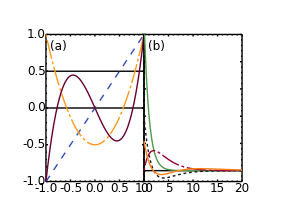

```mathematica
export=True;
exportPath="/Users/nevence/Documents/utk/jun/qmpropJVFH/";
dataDIR="/Users/nevence/Documents/utk/data/";
suffix="pdf";
firstTimeOnly=True;
Get["LevelScheme`"]
colorList={
RGBColor[0.0,0.0,0.0],(*1 Black*)
RGBColor[0.2,0.3,0.7],(*3 Blue*)
RGBColor[0.99,0.6,0.1],(*2 Orange*)
RGBColor[0.4,0.0,0.2],(*4 Purple*)
RGBColor[0.3,0.6,0.3],(*5 Green*)
RGBColor[0.1,0.1,0.1],(*6 Light Blue*)
RGBColor[0.6,0.0,0.2],(*7 Olive*)
RGBColor[1.0,0.5,0.1](*8 Orange*)
};
dashingList={
(* 1 *) Dashing[None],
(* 3 *) Dashed,
(* 2 *) Dashing[{Tiny,Tiny,Large,Tiny}],

(* 4 *) Dashing[None],
(* 5 *) Dashing[None],
(* 6 *) Dashing[{Tiny,Tiny,Tiny,Tiny}],
(* 7 *) Dashing[{Tiny,Tiny,Large,Tiny}],
(* 8 *) Dashing[None]
};
thicknessList={
(* 1 *) Thickness[Medium],
(* 2 *) Thickness[Medium],
(* 3 *) Thickness[Medium],
(* 4 *) Thin,
(* 5 *) Thickness[Medium],
(* 6 *) Thickness[Medium],
(* 7 *) Thickness[Medium],
(* 8 *) Thickness[Medium]
};
styleList=(*{#}&/@*)Flatten/@Transpose[{colorList,dashingList,thicknessList}];
globalOPTS={
Frame->True,
ImageSize->350
};
(*Sample Figure*)
Figure[{
FigurePanel[{{0,1},{0,1}},FrameTicks->Automatic,PlotRange->{{-1,1},{-1,1}}],
RawGraphics[Plot[x^2-1/2,{x,-1,1}]]
},PlotRange->{{-0.1,1.1},{-0.1,1.1}},ImageSize->72*{4,3}
];
(*Sample Multipanel Figure*)
(*Sample Multipanel Figure*)
rMAX=20;
pra=PlotRange->All;
Figure[{
Multipanel[{{0,1},{0,1}},{1,2}],
FigurePanel[{1,1},
PlotRange->{{-1,1},{-1,1}}
],
SchemeLine[{{-1,0},{1,0}}],
RawGraphics[Plot[1/2,{x,-1,1},PlotStyle->styleList[[1]]]],
RawGraphics[Plot[x,{x,-1,1},PlotStyle->styleList[[2]]]],
RawGraphics[Plot[(3 x^2-1)/2,{x,-1,1},PlotStyle->styleList[[3]]]],
RawGraphics[Plot[(5 x^3-3x)/2,{x,-1,1},PlotStyle->styleList[[4]]]],
FigurePanel[{1,2},
PlotRange->{{0,rMAX},{-0.04,0.5}}
],
SchemeLine[{{0,0},{rMAX,0}}],
RawGraphics[Plot[(π)^(-1/2)ⅇ^-r,{r,0,rMAX},PlotStyle->styleList[[5]],PlotRange->All]],
RawGraphics[Plot[(32π)^(-1/2)(2-r)ⅇ^(-r/2),{r,0,rMAX},PlotStyle->styleList[[6]],PlotRange->All]],
RawGraphics[Plot[(32π)^(-1/2)r ⅇ^(-r/2),{r,0,rMAX},PlotStyle->styleList[[7]],PlotRange->All]],
RawGraphics[Plot[(3^9 π)^(-1/2)(27-18r+2 r^2)ⅇ^(-r/3),{r,0,rMAX},PlotStyle->styleList[[8]],PlotRange->All]]
},PlotRange->{{-0.1,1.1},{-0.1,1.1}},ImageSize->72*{4,3}
]
```

Method

## Laser Pulse & Power Spectrum

### Formula

```mathematica
Clear[n];
out=Integrate[Sin[ω t/2 Subscript[n, cy]]^2 Sin[ω t],t]
```

```mathematica
StandardForm[out]
```

```mathematica
TraditionalForm[out]
```

### Figure

```mathematica
laser[nCycle_,ω_,t_]:=
If[ω t> 0 && (ω t)/(2nCycle)<π,Sin[(ω t)/(2nCycle)]^2 Sin[ω t],0];
F[plotDat_List,ω_]:=With[{t=#[[1]]&/@ plotDat,f=#[[2]]&/@ plotDat},
 1/(√(2π))Sum[f[[n]] ⅇ^(-I ω t[[n]])(t[[n+1]]-t[[n]]),{n,1,Length[f]-1}]
];
abFT[plotDat_List,dω_,ωMAX_]:=Table[{ω,Abs[F[plotDat,ω]]^2},{ω,0,ωMAX,dω}];
```

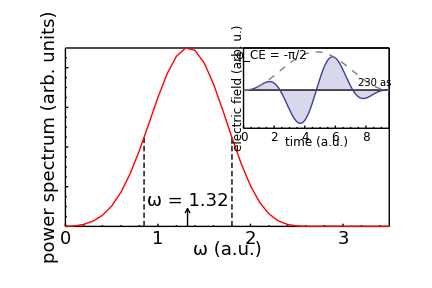

```mathematica
laserFIG=Module[{nCycles=2,ω=1.32,ωMAX=3.5,dω=0.1,lowerFWHM=0.85,upperFWHM=1.80,eps1=0.3,max1,lData,ftlData,ftlPlot,T,maxYω},
T=2π nCycles/ω;
lData=Table[{t,laser[nCycles,ω,t]},{t,0,T,0.05}];
ftlData=abFT[lData,dω,ωMAX];
maxYω=Apply[Max,Map[#[[2]]&,ftlData]];
ftlPlot=ListLinePlot[ftlData,
FrameTicks->{Automatic,None},
FrameLabel->{"ω [atomic units]","Fourier transform"},
PlotStyle->{Thick,Red},
PlotRange->All
];
Figure[{
(* main panel *)
FigurePanel[
{{0,1},{0,1}},
PlotRange->{{0,ωMAX},{0,maxYω}},
ShowTickLabels->{True,False,False,False},
ShowFrameLabels->{True,True,False,False},
FrameTicks->{LinTicks[0,ωMAX,1.,5],Automatic},
FontSize->18,
LabL->"power spectrum (arb. units)",BufferL->2,
LabB->"ω (a.u.)",BufferB->3.5,
TickNudge->{-4,0,0,0}
],
SetOptions[SchemeLine,Dashing->Automatic],
SchemeLine[{{lowerFWHM,0},{lowerFWHM,0.45}}],
SchemeLine[{{upperFWHM,0},{upperFWHM,0.45}}],
ManualLabel[{ω,maxYω/7},"ω = "<>ToString[ω],FontSize->18],
(*ScaledLabel[{0.75,0.4},"I = 1×10^15 W/cm^2",FontSize->18],
ScaledLabel[{0.75,0.3},"E = 9.0 × 10^8 V/cm",FontSize->18],*)
SchemeArrow[{ω,0},{ω,maxYω/10}],
RawGraphics[ftlPlot],

(* inset panel *)
ScaledFigurePanel[
{{0.55,1},{0.55,1}},
PlotRange->{{0,T},{-1,1.1}},
FrameTicks->{LinTicks[0,T],None},
TickFontSize->12,
TickNudge->{-3,0,0,0},
LabB->"time (a.u.)",BufferB->3,
LabL->"electric field (arb. u.)",BufferL->1
],
SchemeLine[{{0,0},{T,0}},Dashing->None],
ScaledLabel[{0.9,0.57},"230 as",FontSize->10],

ScaledLabel[{0.19,0.91},"φ_CE = -π/2"],
RawGraphics[Plot[laser[nCycles,ω,t],{t,0,T},Filling->Axis]],
RawGraphics[Plot[Sin[(ω t)/(2 nCycles)]^2,{t,0,10},PlotStyle->{Gray,Dashed}]]
},
PlotRange->{{-0.08,1.01},{-0.2,1.01}},ImageSize->72*{6,4}
]
]
If[export,Export[exportPath<>"laser."<>suffix,laserFIG]]
```

## MRA

### Version 1: Connect the dots

#### Panel

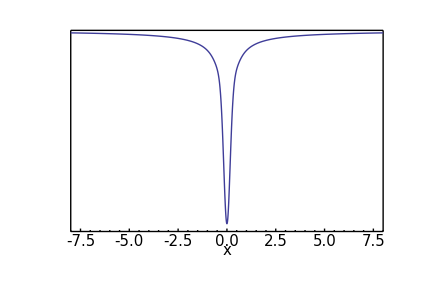

```mathematica
sV[rr_]:=With[{r=Abs[rr]},If[r>6.5,1/r,
If[r>10^-8,Erf[r]/r+(ⅇ^(-r^2)+16 ⅇ^(-4 r^2))/(3 √π),
(2.0+17/3)/(√π)]
]]
xMAX=8;
xMIN=-xMAX;
yMIN=-10;
yMAX=0;
testF[x_]:=With[{c=0.45},-sV[x/c]/c]
testFFIG=
Figure[{
FigurePanel[
{{0,1},{0,1}},
FontSize->15,
PlotRange->{{xMIN,xMAX},{yMIN,yMAX}},
FrameTicks->{Automatic,None},
LabB->"x",BufferB->3,
TickNudge->{-2,0,0,0}
],
RawGraphics[Plot[testF[x],{x,xMIN,xMAX},
PlotPoints->100,
PlotRange->All]],
SchemeLine[{{xMIN,xMAX},{yMIN,yMAX}}]
},
PlotRange->{{-0.1,1.03},{-0.15,1.02}},ImageSize->72{6,4}
]
If[export,Export[exportPath<>"testF."<>suffix,testFFIG]]
```

#### Multiresolution

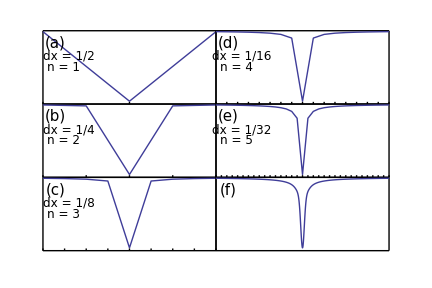

/Users/nevence/Documents/utk/first/mra.pdf

```mathematica
(*testF[x_]:=With[{a=10,R=0.2},Exp[-a Abs[x+R]]+Exp[-a Abs[x-R]]]*)
makePanel[i_,j_,n_,lett_]:=Sequence[
FigurePanel[{i,j},
FrameTicks->None,
PlotRange->{{xMIN,xMAX},{yMIN,yMAX}},
PanelLetter->lett
],RawGraphics[ListLinePlot[
Table[{x,testF[x]},{x,xMIN,xMAX,(xMAX-xMIN)2^-n}],PlotRange->{yMIN,yMAX}]],
ScaledLabel[{0.12,0.5},"n = "<>ToString[n]],
ScaledLabel[{0.15,0.65},"dx = "<>ToString[InputForm@Power[2,-n]]],Sequence@@Table[SchemeLine[{{(xMAX-xMIN)*(1 -k/2^n),yMIN},{(xMAX-xMIN)*(1 -k/2^n),yMIN+0.3}}],{k,0,2^(n+1)}]
]

mraFIG=Figure[{
Multipanel[
{{0,1},{0,1}},
{3,2},
FontSize->15,
TickNudge->{-2,0,0,0}
],
makePanel[1,1,1,"(a)"],
makePanel[2,1,2,"(b)"],
makePanel[3,1,3,"(c)"],
makePanel[1,2,4,"(d)"],
makePanel[2,2,5,"(e)"],
FigurePanel[{3,2},FrameTicks->None,PlotRange->{{xMIN,xMAX},{yMIN,yMAX}}],
RawGraphics[Plot[testF[x],{x,xMIN,xMAX},PlotPoints->100,PlotRange->All]]
},
PlotRange->{{-0.01,1.01},{-0.05,1.02}},ImageSize->72{6,4}
]
If[export,Export[exportPath<>"mra."<>suffix,mraFIG]]
(*Clear[xMIN,xMAX,yMIN,yMAX]*)
```

#### MADNESS’s multiresolution

{-8,-4,-2,-1,0,1,2,4,8}

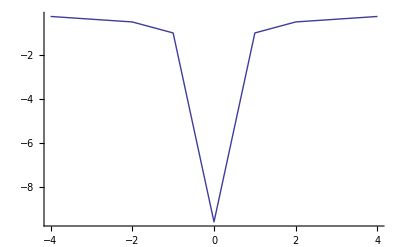

```mathematica
dyPoints[xMAX_,n_]:=Sort[Join[Table[-xMAX*2^-p,{p,0,n}],{0},Table[xMAX*2^-p,{p,0,n}]]];

pMAX=3;
dyPoints[xMAX,pMAX]
ListLinePlot[{#,testF[#]}&/@dyPoints[4,2],PlotRange->All]
```

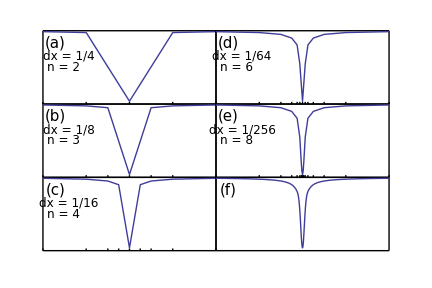

/Users/nevence/Documents/utk/first/madmra.pdf

```mathematica
makeMADPanel[i_,j_,n_,lett_]:=Sequence[
FigurePanel[{i,j},
FrameTicks->None,
PlotRange->{{xMIN,xMAX},{yMIN,yMAX}},
PanelLetter->lett
],
RawGraphics[ListLinePlot[{#,testF[#]}&/@dyPoints[xMAX,n],PlotRange->{yMIN,yMAX}]],
ScaledLabel[{0.12,0.5},"n = "<>ToString[n+1]],
ScaledLabel[{0.15,0.65},"dx = "<>ToString[InputForm@Power[2,-1-n]]],Sequence@@SchemeLine[{{#,yMIN},{#,yMIN+0.3}}]&/@dyPoints[xMAX,n]
]

madmraFIG=Figure[{
Multipanel[
{{0,1},{0,1}},
{3,2},
FontSize->15,
TickNudge->{-2,0,0,0}
],
makeMADPanel[1,1,1,"(a)"],
makeMADPanel[2,1,2,"(b)"],
makeMADPanel[3,1,3,"(c)"],
makeMADPanel[1,2,5,"(d)"],
makeMADPanel[2,2,7,"(e)"],
FigurePanel[{3,2},FrameTicks->None,PlotRange->{{xMIN,xMAX},{yMIN,yMAX}}],
RawGraphics[Plot[testF[x],{x,xMIN,xMAX},PlotPoints->100,PlotRange->All]]
},
PlotRange->{{-0.01,1.01},{-0.05,1.02}},ImageSize->72{6,4}
]
If[export,Export[exportPath<>"madmra."<>suffix,madmraFIG]]
```

#### Scaling and Wavlet functions

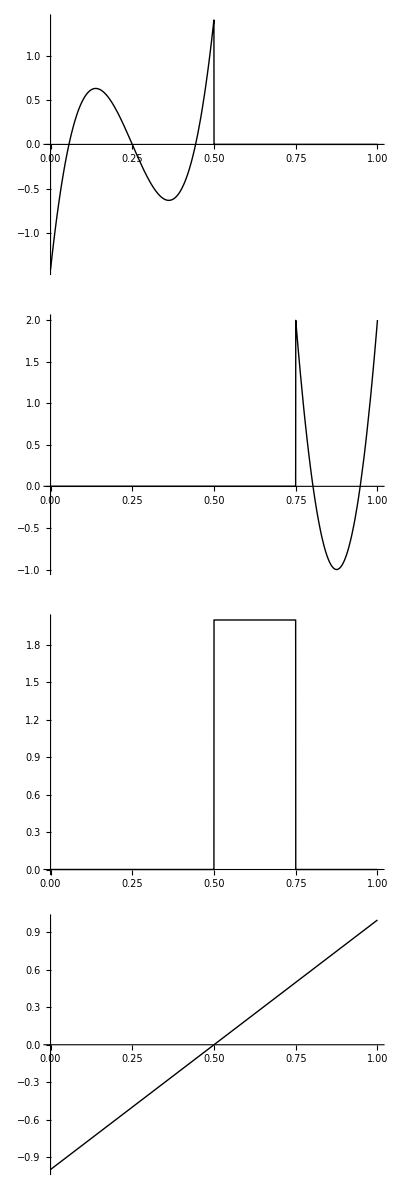

```mathematica
scalingF[n_,k_,j_,x_]:=If[k/2^n<x<(k+1)/2^n,2^(n/2)LegendreP[j,2^(n+1)x-2k-1],0];
plotSF[n_,k_,j_]:=Plot[scalingF[n,k,j,x],{x,0,1},PlotStyle->Directive[Thick,Black]];
Grid[{{plotSF[1,0,3]},{plotSF[2,3,2]},{plotSF[2,2,0]},{plotSF[0,0,1]}}]
```

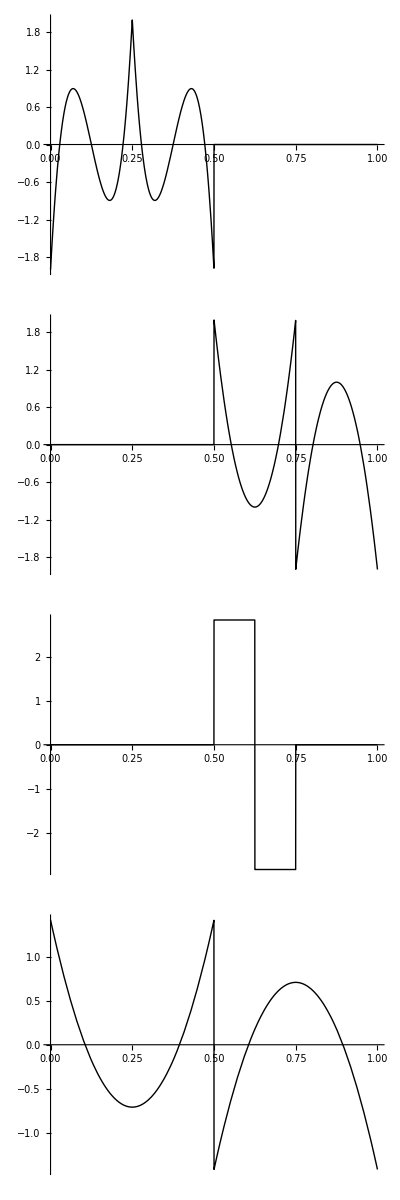

```mathematica
waveletF[n_,k_,j_,x_]:=scalingF[n+1,2k,j,x]-scalingF[n+1,2k+1,j,x];
plotWF[n_,k_,j_]:=Plot[waveletF[n,k,j,x],{x,0,1},PlotStyle->Directive[Thick,Black]];
Grid[{{plotWF[1,0,3]},{plotWF[1,1,2]},{plotWF[2,2,0]},{plotWF[0,0,2]}}]
```

```mathematica
fPanel[n_]:=Sequence[
FigurePanel[{1,n+1}],
RawGraphics[plotSF[0,0,n]],
SchemeLine[{{0,0},{1,0}}],
FigurePanel[{2,n+1}],
RawGraphics[plotWF[0,0,n]],
SchemeLine[{{0,0},{1,0}}],
]
```

Multipanel::unknownopt: Unknown option PlotRange specified for Multipanel.

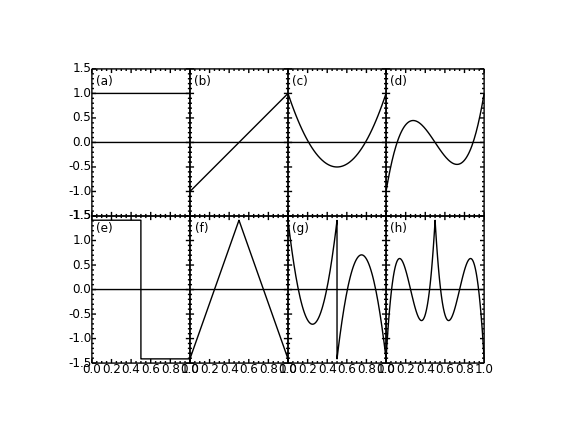

/Users/nevence/Documents/utk/first/scalWave.pdf

```mathematica
scalWaveFIG=Figure[{
Multipanel[
{{0,1},{0,1}},
{2,4},
PlotRange->{{0,1},{-1.5,1.5}}
],
fPanel[0],
fPanel[1],
fPanel[2],
fPanel[3],
},
PlotRange->{{-0.1,1.1},{-0.1,1.1}},ImageSize->72*2{4,3}
]
If[export,Export[exportPath<>"scalWave."<>suffix,scalWaveFIG]]
```

#### Combination Graph

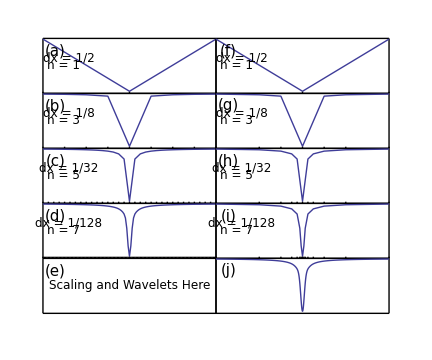

/Users/nevence/Documents/utk/first/mra.pdf

```mathematica
(*testF[x_]:=With[{a=10,R=0.2},Exp[-a Abs[x+R]]+Exp[-a Abs[x-R]]]*)
makePanel[i_,j_,n_,lett_]:=Sequence[
FigurePanel[{i,j},
FrameTicks->None,
PlotRange->{{xMIN,xMAX},{yMIN,yMAX}},
PanelLetter->lett
],RawGraphics[ListLinePlot[
Table[{x,testF[x]},{x,xMIN,xMAX,(xMAX-xMIN)2^-n}],PlotRange->{yMIN,yMAX}]],
ScaledLabel[{0.12,0.5},"n = "<>ToString[n]],
ScaledLabel[{0.15,0.65},"dx = "<>ToString[InputForm@Power[2,-n]]],Sequence@@Table[SchemeLine[{{(xMAX-xMIN)*(1 -k/2^n),yMIN},{(xMAX-xMIN)*(1 -k/2^n),yMIN+0.3}}],{k,0,2^(n+1)}]
]
n0=1;
mraFIG=Figure[{
Multipanel[
{{0,1},{0,1}},
{5,2},
FontSize->15,
TickNudge->{-2,0,0,0}
],
makePanel[1,1,n0,"(a)"],
makePanel[2,1,n0+2,"(b)"],
makePanel[3,1,n0+4,"(c)"],
makePanel[4,1,n0+6,"(d)"],
makeMADPanel[1,2,n0-1,"(f)"],
makeMADPanel[2,2,n0+1,"(g)"],
makeMADPanel[3,2,n0+3,"(h)"],
makeMADPanel[4,2,n0+5,"(i)"],
FigurePanel[{5,1},
FrameTicks->None,
PanelLetter->"(e)",
PlotRange->{{xMIN,xMAX},{yMIN,yMAX}}],
ScaledLabel[{0.5,0.5},"Scaling and Wavelets Here"],
FigurePanel[{5,2},FrameTicks->None,PlotRange->{{xMIN,xMAX},{yMIN,yMAX}}],
RawGraphics[Plot[testF[x],{x,xMIN,xMAX},PlotPoints->100,PlotRange->All]]
},
PlotRange->{{-0.01,1.01},{-0.05,1.02}},ImageSize->72{6,5}
]
If[export,Export[exportPath<>"mra."<>suffix,mraFIG]]
(*Clear[xMIN,xMAX,yMIN,yMAX]*)
```

### Version 2: Scaling Functions (Simulation Coordinates)

Calculate sum coefficients

```mathematica
s[n_,l_,k_]:=NIntegrate[f[x]*scalingF[n,l,k,x],{x,l*2^-n,(l+1)2^-n}]
```

```mathematica
fM[n_,k_]:=Table[s[n,l,i],{l,0,2^n-1},{i,0,k}]
fM[1,0]
```

{{0.55645},{0.337504}}

```mathematica
(*Why are the coefficients from fMdat 0?*)
fMeval[fMdat_,x_]:=Module[{
n=Log[2,Length[fMdat]],
k=Length[fMdat[[1]]],
l},
(*\[MathematicaIcon] indexes w/ 1 *)
l=Floor[x/2^-n];
(*Print["n=",n," l=",l," k=",k-1];
Print["ϕ",n,l,0," = ",scalingF[n,l,0,x]];*)
Sum[fMdat[[l+1,i+1]]scalingF[n,l,i,x],{i,0,k-1}]
(*Table[fMdat[[l+1,i+1]]scalingF[n,l,i,x],{i,0,k-1}]*)
]
```

dat1= {{-2.48837,0.449508},{-1.03272,0.264068}}

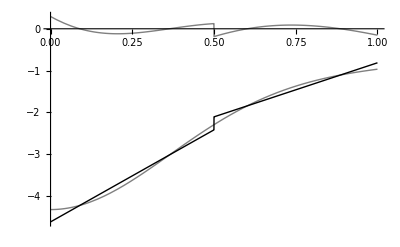

n=0 k=2 l=1

0.

```mathematica
Module[{dat1,n=1,k=1,mag=1},
Print["dat1= ",dat1=Table[s[n,l,i],{l,0,2^n-1},{i,0,k}]];
Plot[{f[x],fMeval[dat1,x],mag(f[x]-fMeval[dat1,x])},{x,0,1},PlotStyle->{Gray,Black,{Gray,Dashing->Automatic}},
PlotRange->All
]]
```

### Version 3: User coordinates

The goal is to map [xLo, xHi] onto [0,1]
I am going to store function parameters in a list, so they can be passed to each function without having icky global variables: {L, n, k}

#### Functions

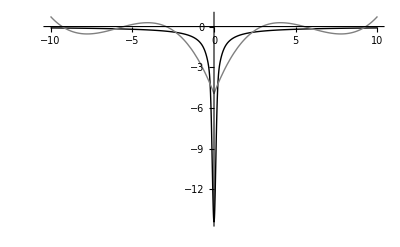

```mathematica
(*The model potential*)
sV[r_]:=If[r>6.5,1/r,
If[r>10^-8,Erf[r]/r+(ⅇ^(-r^2)+16 ⅇ^(-4 r^2))/(3 √π),
(2.0+17/3)/(√π)]
];
f[x_]:=With[{ξ=0.3},-sV[Abs[x]/ξ]/ξ]


scalingF[n_,l_,i_,x_]:=If[l/2^n≤x≤(l+1)/2^n,√(2i+1)2^(n/2)LegendreP[i,2(2^n x-l)-1],0];
waveletF[n_,k_,j_,x_]:=scalingF[n+1,2k,j,x]-scalingF[n+1,2k+1,j,x];


fMake[param_,func_]:=Module[{
xHi=param[[1]],
xLo=-param[[1]],
n=param[[2]],
k=param[[3]],
vol=2 param[[1]]},
xUser[xx_]:=(xHi-xLo)xx+xLo;
s[l_,i_]:=2^(-n/2)vol^(1/2)*NIntegrate[func[xUser[x]]*scalingF[n,l,i,x],{x,0,1},AccuracyGoal->4];
Table[s[l,i],{l,0,2^n-1},{i,0,k-1}]
]
(*param={1,1,2};
fMake[param,f]
*)

(*giv*)
fEval[param_,fDAT_,x_]:=Module[{
xHi=param[[1]],
xLo=-param[[1]],
n=param[[2]],
k=param[[3]],
vol=2 param[[1]],
l,lTest},
xSim[xx_]:=(xx-xLo)/(xHi-xLo);
(*Check that x ∈[-L,L]*)
lTest=Floor[xSim[x]/2^-n];
If[lTest<2^n,l=lTest,l=2^n-1];
If[lTest<0,l=0];
(*Print["n=",n," l=",l," k=",k-1];
Print["ϕ",n,l,0," = ",scalingF[n,l,0,x]];*)
(*\[MathematicaIcon] indexes w/ 1 *)
2^(n/2)vol^(-1/2)*Sum[fDAT[[l+1,i+1]]scalingF[n,l,i,xSim[x]],{i,0,k-1}]
(*Table[fMdat[[l+1,i+1]]scalingF[n,l,i,x],{i,0,k-1}]*)
]

fPlot[param_,fDAT_]:=Module[{
xHi=param[[1]],
xLo=-param[[1]],
n=param[[2]],
k=param[[3]]
},
(*Plot[{f[x],fEval[param,fDAT,x],(f[x]-fEval[param,fDAT,x])},{x,xLo,xHi},PlotStyle->{Gray,Black,{Gray,Dashing->Automatic}},
PlotRange->All
]*)
Plot[{f[x],fEval[param,fDAT,x]},{x,xLo,xHi},PlotStyle->{Black,Gray},
PlotRange->All
]
]
param={10,1,4};
fPlot[param,fMake[param,f]]

(*Determine the maximum on the interval defined by n and l*)
maxDiff[param_,coeffs_,f_,n_,l_]:=Module[{
L=param[[1]],
k=param[[3]],
ϵ=param[[4]],
xLo,xHi,dat},
xLo=2L*l*2^-n-L;
xHi=2L*(l+1)*2^-n-L;
dat=Table[Abs[f[x]-fEval[param,coeffs,x]],{x,xLo,xHi,(xHi-xLo)/(3k)}];
Max[dat]
]
(*param={10,1,3,0.1};
coeffs=fMake[param,f]
maxDiff[param,coeffs,f,3,7]
*)
```

#### 2nd Figure

{3,0,2}

{3,1,2}

{3,2,2}

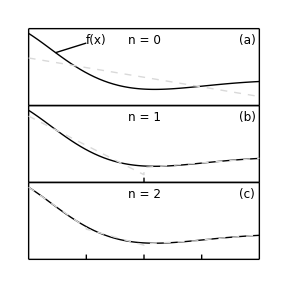

/Users/nevence/Documents/utk/thesis/MADres.pdf

```mathematica
L=3;
(*L,n,k*)
f[x_]:=Exp[-0.5(L+x)]Cos[π/4(L+x)]
p=Plot[f[x],{x,-3,3},PlotRange->All,PlotStyle->Black];
param={L,0,2}
fDAT=fMake[param,f];
aStyle={LightGray,Dashed};
p0=Show[p,Plot[fEval[param,fDAT,x],{x,-L,L},PlotRange->All,PlotStyle->aStyle]];
param={L,1,2}
fDAT=fMake[param,f];
p1=Show[p,Plot[fEval[param,fDAT,x],{x,-L,L},PlotRange->All,PlotStyle->aStyle]];
param={L,2,2}
fDAT=fMake[param,f];
p2=Show[p,Plot[fEval[param,fDAT,x],{x,-L,L},PlotRange->All,PlotStyle->aStyle]];

MADresFIG=Figure[{
Multipanel[{{0,1},{0,1}},{3,1}],
FigurePanel[{1,1},
PlotRange->{{-3,3},{-0.5,1.1}},
FrameTicks->None,
PanelLetterCorner->{1,1}],
RawGraphics[p0],
SchemeLine[{{-2.3,0.6},{-1.5,0.8}}],
ManualLabel[{-1.25,0.85},"f(x)"],
ManualLabel[{0,0.85},"n = 0"],
FigurePanel[{2,1},
PlotRange->{{-3,3},{-0.5,1.1}},
FrameTicks->None,
PanelLetterCorner->{1,1}],
RawGraphics[p1],
SchemeLine[{{0,-0.5},{0,-0.4}}],
ManualLabel[{0,0.85},"n = 1"],
FigurePanel[{3,1},
PlotRange->{{-3,3},{-0.5,1.1}},
FrameTicks->None,
PanelLetterCorner->{1,1}],
RawGraphics[p2],
SchemeLine[{{0,-0.5},{0,-0.4}}],
SchemeLine[{{-1.5,-0.5},{-1.5,-0.4}}],
SchemeLine[{{1.5,-0.5},{1.5,-0.4}}],
ManualLabel[{0,0.85},"n = 2"]
},PlotRange->{{-0.01,1.01},{-0.01,1.01}},ImageSize->72*{4,4}
]
If[export,Export[exportPath<>"MADres."<>suffix,MADresFIG]]
```

### Version 4: Adaptive Refinement

#### Function Definitions

```mathematica
(*The model potential*)
sV[r_]:=If[r>6.5,1/r,
If[r>10^-8,Erf[r]/r+(ⅇ^(-r^2)+16 ⅇ^(-4 r^2))/(3 √π),
(2.0+17/3)/(√π)]
];
f[x_]:=With[{ξ=0.3},-sV[Abs[x]/ξ]/ξ]

scalingF[n_,l_,i_,x_]:=If[l/2^n≤x≤(l+1)/2^n,√(2i+1)2^(n/2)LegendreP[i,2(2^n x-l)-1],0];
waveletF[n_,k_,j_,x_]:=scalingF[n+1,2k,j,x]-scalingF[n+1,2k+1,j,x];


(*
Evaluate an adaptively refined function;
param:  parameters from the input file: {L,k,ϵ};
fDAT: each box is represented by the element {REFINED, n, l, {k1, k2, ...}};
To evaluate the function, fDAT is traversed each box if the point is in the domain
*)
fAdEval[param_,fDAT_,x_]:=Module[{
L=param[[1]],
k=param[[2]],
vol=2 param[[1]],
n,l,lTest,
xLo,xHi,
box,answer,i},
If[Abs[x]>L,0,(*Check that x ∈[-L,L]*)
For[i=1,i≤Length[fDAT],i++,(*Test each box*)
box=fDAT[[i]];
n=box[[2]];
l=box[[3]];
(*Print["n=",n," l=",l," k=",k-1];
Print["ϕ",n,l,0," = ",scalingF[n,l,0,x]];*)
xLo=2L*l*2^-n-L;
xHi=2L*(l+1)*2^-n-L;
If[xLo≤x≤xHi,(*\[MathematicaIcon] indexes w/ 1 *)
Return[vol^(-1/2)*Sum[box[[4,i+1]]scalingF[n,l,i,(x+L)/(2L)],{i,0,k-1}]]
]
]
]
]

(*
Determine the maximum difference on the interval defined by n and l;
param:  parameters from the input file: {L,k,ϵ};
boxDAT: each box is represented by the element {REFINED, n, l, {k1, k2, ...}};
f: the analytic function *)
maxDiff[param_,boxDAT_,f_]:=Module[{
L=param[[1]],
k=param[[2]],
n=boxDAT[[2]],
l=boxDAT[[3]],
kDAT=boxDAT[[4]],
xLo,xHi,dat},
xLo=2L*l*2^-n-L;
xHi=2L*(l+1)*2^-n-L;
(*Evaluate the function difference at 3k points, and find the maximum*)
Max[Table[Abs[f[x]-fAdEval[param,{boxDAT},x]],{x,xLo,xHi,(xHi-xLo)/(3k)}]]
]

(*
Refine function down a level;
param:  parameters from the input file: {L,k,ϵ};
boxDAT: each box is represented by the element {REFINED, n, l, {k1, k2, ...}};
f: the analytic function;
For each box that is not refined;
split in two;
determine if refined;
return the a new list of function data*)
fRefine[param_,f_,fDAT_]:=Module[{
L=param[[1]],
k=param[[2]],
ϵ=param[[3]],
nBoxes,box,
n,l,i,
xLo,xHi,
lChild,rChild,
lDAT,rDAT,
lREFINED,rREFINED,
convergedBoxes={}},
nBoxes=Length[fDAT];
s[nn_,ll_,i_]:=(2L)^(-1/2)*NIntegrate[f[x]*scalingF[nn,ll,i,(x+L)/(2L)],{x,-L,L},AccuracyGoal->3];
Select[Reap[
For[i=1,i≤nBoxes,++i,
box=fDAT[[i]];
If[box[[1]],(*This box satisfies the truncation criteria*)
Sow[box];
Continue[];
];
lREFINED=False;
rREFINED=False;
n=box[[2]];
l=box[[3]];
lDAT=Table[s[n+1,2l,i],{i,0,k-1}];
rDAT=Table[s[n+1,2l+1,i],{i,0,k-1}];
lChild={lREFINED,n+1,2l,lDAT};
rChild={rREFINED,n+1,2l+1,rDAT};
If[Abs[Evaluate[maxDiff[param,lChild,f]]]<ϵ,lREFINED=True];
If[Abs[Evaluate[maxDiff[param,rChild,f]]]<ϵ,rREFINED=True];
lChild={lREFINED,n+1,2l,lDAT};
rChild={rREFINED,n+1,2l+1,rDAT};
Sow[lChild];
Sow[rChild];
];
][[2,1]],Length[#]==4&]
]

(*
Create a MADNESS function--that is a list of function coefficients;
param:  parameters from the input file: {L,k,ϵ};
f: the analytic function;
Apply refine until all of the boxes are refined;
*)
fMake[param_,f_]:=Module[{
L=param[[1]],
k=param[[2]],
ϵ=param[[3]],
vol=2 param[[1]],
dat,n=1},
(*{REFINED,n,l,{k}}*)
dat={{False,0,0,Table[0,{i,k}]}};
fRef[x_]:=fRefine[param,f,x];
notAllTrue[list_]:=!And@@(#[[1]]&/@list);
NestWhile[fRef,dat,notAllTrue]
]

getData[t_,k_,opts___]:=Module[{dat={#[[1]],Log[10,#[[2]]]}&/@Import["/Users/nevence/Documents/utk/data/FIG2/err_t"<>ToString[t]<>"_k"<>ToString[k]<>".dat"]},
ListPlot[dat,Joined->True,opts]
]
```

#### Figure

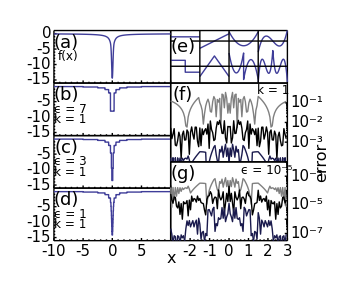

/Users/nevence/Documents/utk/first/mra.pdf

```mathematica
errFig1=Show[
getData[1,1,PlotStyle->Gray,PlotRange->{-5,0}],
getData[3,1,PlotStyle->Black],
getData[5,1,PlotStyle->RGBColor[0.1,0.1,0.3]]
];
errFig2=Show[
getData[5,1,PlotStyle->Gray,PlotRange->{-8,-3}],
getData[5,2,PlotStyle->Black],
getData[5,6,PlotStyle->RGBColor[0.1,0.1,0.3]]
];
mraFIG=Module[{L=10,ϵ={7,3,1,10^-1,10^-2,5*10^-3},k={1,4},Δy=6,yMIN=-16,yMAX=1},
makeFigure[n_,m_,k_,ϵ_,lett_,opts___]:=Module[{param={L,k,ϵ},fDAT},
fDAT=fMake[param,f];
Sequence@@{
FigurePanel[{n,m},
PanelLetter->lett,
PlotRange->{{-L,L},{yMIN,yMAX}},
opts,
FrameTicks->{Automatic,LinTicks[-15,-1,5.0,5]},
ShowTickLabels->{False,True,False,True},
ShowFrameLabels->{False,True,False,True},
TickNudge->{0,{-3,0},0,0}
],
ScaledLabel[{0.14,0.5},"ϵ = "<>ToString[ϵ]],
ScaledLabel[{0.14,0.3},"k = "<>ToString[k]],
RawGraphics[Plot[fAdEval[param,fDAT,x],{x,-L,L},PlotRange->All]]
}];
xUser[x_]:=(x+L)/(2L);
plotSF[n_,l_,i_,opts___]:=Plot[scalingF[n,l,i,xUser[x]]+Δy,{x,2L*2^-n*l-L,2L*2^-n*(l+1)-L},opts];
plotWF[n_,l_,i_,opts___]:=Plot[waveletF[n,l,i,xUser[x]]-Δy,{x,2L*2^-n*l-L,2L*2^-n*(l+1)-L},opts];
Figure[{
Multipanel[{{0,1},{0,1}},{4,2},
ShowTickLabels->{False,False,False,False},
ShowFrameLabels->{False,False,False,False},
XFrameTicks->None,
YFrameTicks->None,
FontSize->18,
TickFontSize->15
],
ScaledLabel[{0.47,0.015},"x",FontSize->16],
ScaledLabel[{0.98,0.42},"error",Orientation->Vertical,FontSize->16],
(*Multiresolution*)
FigurePanel[{1,2},
PanelLetter->"(e)",
PanelLetterInset->{15,20},
PlotRange->{{-L,L},{-14,11}}],
RawGraphics[Show[{
plotSF[2,0,0,PlotRange->{{-L,L},{-L,L}}],
plotSF[2,1,1],
plotSF[2,2,2],
plotSF[2,3,3],
plotWF[2,0,0],
plotWF[2,1,1],
plotWF[2,2,2],
plotWF[2,3,3]
}]],
SchemeLine[{{-L,Δy},{-0.93L,Δy}}],
SchemeLine[{{-0.65L,Δy},{L,Δy}}],
SchemeLine[{{-L,-Δy},{L,-Δy}}],
SchemeLine[{{-L/2,-14},{-L/2,11}}],
SchemeLine[{{0,-14},{0,11}}],
SchemeLine[{{L/2,-14},{L/2,11}}],
(*ƒ(x) Figure*)
FigurePanel[{1,1},
PanelLetter->"(a)",
PlotRange->{{-L,L},{yMIN,yMAX}},
FrameTicks->{Automatic,LinTicks[-15,0,5.0,5]},
ShowTickLabels->{False,True,False,True},
ShowFrameLabels->{False,True,False,True},
TickNudge->{0,{-3,0},0,0}
],
RawGraphics[Plot[f[x],{x,-L,L},PlotRange->{{-L,L},{yMIN,yMAX}}]],
ScaledLabel[{0.12,0.5},"f(x)"],
(*MRA refinement*)
makeFigure[2,1,k[[1]],ϵ[[1]],"(b)"],
makeFigure[3,1,k[[1]],ϵ[[2]],"(c)"],
makeFigure[4,1,k[[1]],ϵ[[3]],"(d)",
FrameTicks->{LinTicks[-10,9,5.0,5],LinTicks[-15,-1,5.0,5]},
ShowTickLabels->{True,True,False,False},
ShowFrameLabels->{True,False,False,False},
TickNudge->{-3,{-3,0},0,0}
],
(*ϵ error*)
FigurePanel[{2,2},
PlotRange->{{-3,3},{-4,0}},
PanelLetter->"(f)",
PanelAdjustments->{{0,0},{0.5,0}},
FrameTicks->{None,None,None,LogTicks[-3,-1]},
ShowTickLabels->{False,False,False,True},
ShowFrameLabels->{False,False,False,True},
TickNudge->{0,0,0,{3,0}}
],
ScaledLabel[{0.875,0.9},"k = 1"],
RawGraphics[errFig1],
(*k error*)
FigurePanel[{4,2},
PlotRange->{{-3,3},{-7.5,-2}},
PanelLetter->"(g)",
PanelAdjustments->{{0,0},{0,0.5}},
FrameTicks->{LinTicks[-2,3],None,None,LogTicks[-7,-2,TickLabelStep->2]},
ShowTickLabels->{True,False,False,True},
ShowFrameLabels->{True,False,False,True},
TickNudge->{-3,0,0,{3,0}}
],
ScaledLabel[{0.82,0.89},"ϵ = 10^-5"],
RawGraphics[errFig2]
},PlotRange->{{-0.09,1.17},{-0.1,1.02}},ImageSize->72*{5,4}
]]
If[export,Export[exportPath<>"mra."<>"pdf",mraFIG]]
```

## Propagator

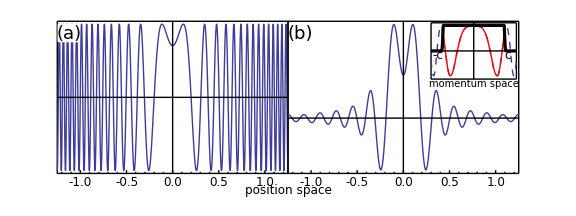

/Users/nevence/Documents/utk/first/freePP.pdf

```mathematica
blPropagatorFIG=Module[{
kMAX=50, (*Maximum frequency component*)
dk=0.5,
Δk=40,(*Width of the windowing function*), (*Why is Δk differnt from kMAX?*)
Δx=1.25,(*The x domain*)
dx=0.01,
dy=0.1,
dt=0.0085,
ticks1={0.2,0.4,0.5,0.6,0.7,0.75,0.8,0.85,0.9,0.95,1,1.025,1.05,1.075,1.1,1.125,1.15,1.175,1.2,1.225,1.25},
ticks2={0.2,0.4,0.6,0.8,1,1.2},
dat,ftDAT,k,ft,ftWinDAT,xMAX},
(*Green's function*)
G[x_,t_]:=1/(2π I t)^(1/2)Exp[(- x^2)/(2I t)];
gauss[α_,x_]:=Exp[-α x^2];
(*Window function*)
wind[a_,b_,ϵ_,α_,x_]:=If[x-a<ϵ,gauss[α,x-a-ϵ],If[b-x<ϵ,gauss[α,x-(b-ϵ)],1]];
wx[x_]:=wind[dx-Δx,Δx-dx,Δx/10,500,x];
wk[k_]:=wind[(dk-Δk),(Δk-dk),Δk/10,1,k];
(*Fourier Integral*)
F[plotDat_List,k_]:=With[{x=#[[1]]&/@ plotDat,f=#[[2]]&/@ plotDat},
 1/(√(2π))Sum[wx[x[[n]]]f[[n]] ⅇ^(-I k x[[n]])(x[[n+1]]-x[[n]]),{n,1,Length[f]-1}]
];
(*Inverse Fourier Integral*)
FI[plotDat_List,k_]:=With[{x=#[[1]]&/@ plotDat,f=#[[2]]&/@ plotDat},
 1/(√(2π))Sum[wk[x[[n]]]f[[n]] ⅇ^(I k x[[n]])(x[[n+1]]-x[[n]]),{n,1,Length[f]-1}]
];
(*Fourier Transform*)
FT[plotDat_List,dk_]:=Table[{k,F[plotDat,k]},{k,-kMAX,kMAX,dk}];

(* Data is complex *)
dat=Table[{x,wx[x]G[x,dt]},{x,-Δx,Δx,dx}];
ftDAT=FT[dat,dk];
k=First[#]&/@ftDAT;
ft=#[[2]]&/@ftDAT;
ftWinDAT=Table[{k[[i]],ft[[i]]wk[k[[i]]]},{i,1,Length[k]}];
xMAX=Max[Re[#[[2]]]&/@dat];
upperBoundK=Max[Abs[#]&/@ft];
(* Inverse Transform *)
xDAT=Table[{x,Re@FI[ftWinDAT,x]},{x,-Δx,Δx,dx}];
freePPFIG=Figure[{
Multipanel[{{0,1},{0,1}},
{1,2},
PanelLetterFontSize->18],
ScaledLabel[{0.5,0.03},"position space"],
(*freePP*)
FigurePanel[{1,1},
PlotRange->{{-Δx,Δx},{-4.5,4.5}},
FrameTicks->{Automatic,None,None,None},
TickNudge->{-3,0,0,0}
],
RawGraphics[Plot[Re@G[x,dt],{x,-Δx,Δx}]],
SchemeLine[{{-Δx,0},{Δx,0}}],
SchemeLine[{{0,-4.5},{0,4.5}}],
SchemeBox[{{-1.24,-1.02},{3.3,4.3}},Color->White],
(*Band-limited freePP*)
FigurePanel[{1,2},
PlotRange->{{-Δx,Δx},{-3,5.25}},
FrameTicks->{Automatic,None,None,None},
TickNudge->{-3,0,0,0}
],
RawGraphics[ListLinePlot[xDAT,PlotRange->All]],
SchemeLine[{{-Δx,0},{Δx,0}}],
SchemeLine[{{0,-3},{0,5.25}}],
(*Inset*)
ScaledFigurePanel[{{0.62,0.99},{0.62,0.99}},
PlotRange->{{-kMAX,kMAX},{-0.45,0.45}},
FrameTicks->None,
FontSize->10,
LabB->"momentum space",BufferB->1
],
RawGraphics[ListLinePlot[Re/@ftDAT,PlotStyle->Dashing[Small],PlotRange->All]],
RawGraphics[ListLinePlot[Re/@ftWinDAT,PlotStyle->Red]],
RawGraphics[Plot[upperBoundK wk[kk],{kk,-kMAX,kMAX},
PlotStyle->{Thickness[0.004],Black},
PlotRange->All
]],
SchemeLine[{{-kMAX,0},{kMAX,0}}],
SchemeLine[{{0,-1},{0,1}}],
ManualLabel[{-42,-0.08},"-c"],
ManualLabel[{40,-0.08},"c"]
},PlotRange->{{-0.01,1.01},{-0.15,1.01}},ImageSize->72*{8,3}
]
]
If[export,Export[exportPath<>"freePP."<>suffix,freePPFIG]]
```

## Model Potential

{{{0.3,-3.42321},{0.2,-4.282},{0.1,-5.87473},{0.05,-7.55834},{0.03,-8.85294}},{{0.3,-4.08309},{0.2,-4.96501},{0.1,-6.59532},{0.05,-8.35468},{0.03,-9.79588}},{{0.3,-4.75712},{0.2,-5.63826},{0.1,-7.26889},{0.05,-9.02733},{0.03,-10.4685}},{{0.3,-5.17732},{0.2,-6.05833},{0.1,-7.68916},{0.05,-9.44733},{0.03,-10.8861}}}

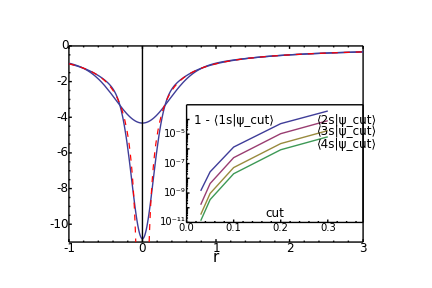

/Users/nevence/Documents/utk/first/modelV.pdf

```mathematica
sV[r_]:=If[r>6.5,1/r,
If[r>10^-8,Erf[r]/r+(ⅇ^(-r^2)+16 ⅇ^(-4 r^2))/(3 √π),
(2.0+17/3)/(√π)]
]
cutDAT=Transpose[{{0.3,#}&/@{0.999622607998,0.000082586982,0.000017493685,0.000006647794},
{0.2,#}&/@{0.999947760227,0.000010838980,0.000002300077,0.000000874313},
{0.1,#}&/@{0.999998665635,0.000000253909,0.000000053840,0.000000020457},
{0.05,#}&/@{0.999999972352,0.000000004419,0.000000000939,0.000000000357},
{0.03,#}&/@{0.999999998597,0.000000000160,0.000000000034,0.000000000013}}];
(*subtract one from the 1s overlap*)
cut2DAT=Prepend[cutDAT[[2;;]],{#[[1]],1-#[[2]]}&/@cutDAT[[1]]];
(*loggify it*)
cut3DAT=Table[{#[[1]],Log[10,#[[2]]]}&/@cut2DAT[[i]],{i,1,Length[cut2DAT]}]
Needs["PlotLegends`"];
cutFIG=ListPlot[cut3DAT,
Frame->True,
Joined->True,
FrameTicks->{LinTicks,LogTicks,None,None}
];
modelFIG=With[{sF=12,xL=-1,xR=3},Show[Plot[Table[-sV[Abs[r]/c]/c,{c,{0.4,1}}],{r,xL,xR},
Epilog->Inset[cutFIG,Scaled[{0.7,0.35}],Center,3.5],
Frame->False,
Evaluate[Sequence@@globalOPTS],
PlotRange->{-11,0}
],
Plot[-1/r,{r,0.09,xR},
PlotRange->{-22,0},
PlotStyle->{Dashing[{0.01,0.01}],Thickness[0.002],RGBColor[1,0,0]}],
Plot[1/r,{r,xL,-0.09},
PlotRange->{-22,0},
PlotStyle->{Dashing[{0.01,0.01}],Thickness[0.002],RGBColor[1,0,0]}]
]
];

modelVFIG=Figure[{
(*main panel*)
FigurePanel[
{{0,1},{0,1}},
PlotRange->{{-1,3.},{-11,0}},
FrameTicks->{LinTicks[-1,3],LinTicks[-10,0],LinTicks[-1,3],None},
FontSize->15,LabB->textit["r"],BufferB->2.5,
TickFontSize->12
],
RawGraphics[modelFIG],
SchemeLine[{{0,0},{0,-11}}],
(*inset panel*)
ScaledFigurePanel[
{{0.4,1},{0.1,0.7}},
PlotRange->{{0,0.375},{-11,-3}},
FrameTicks->{LinTicks[0,0.375,0.1,5],LogTicks[-11,-4,TickLabelStep->2]},
TickFontSize->10
],
RawGraphics[cutFIG],
ManualLabel[{0.1,-4.1},"1 - ⟨1s|ψ_cut⟩"],
ManualLabel[{0.34,-4.1},"⟨2s|ψ_cut⟩"],
ManualLabel[{0.34,-4.8},"⟨3s|ψ_cut⟩"],
ManualLabel[{0.34,-5.7},"⟨4s|ψ_cut⟩"],
ScaledLabel[{0.5,0.075},textit["cut"]]
},
PlotRange->{{-0.1,1.1},{-0.1,1.1}},ImageSize->2*72*{3,2}
]
If[export,Export[exportPath<>"modelV."<>suffix,modelVFIG]]
```

Convergence

## Bound State vs Thresh

### Prereq

```mathematica
(*Finds the max of a 2D list after stripping off the nlm quantum numbers*)
fMAX[dat_]:=With[{fNUM=Length[First[dat]]},
maxList={};
For[i=1,i≤Length[dat],i++,
thisMax=Max[dat[[i,4;;]] ];
AppendTo[maxList,thisMax];
];
Max[maxList]
]


plotBound[boundData_,tMAX_,nList_List,opts___]:=Module[{
steps=Length[boundData[[1]]]-4,dt,dat1,dat2},
dt=N[tMAX/steps];
dat1=Table[{(i-4) dt,Log[10,boundData[[n,i]] ]},{n,nList},{i,4,Length@boundData[[1]]}];
dat2=Cases[#,{x_,y_}/;x≤10]&/@dat1;
ListLinePlot[dat2,opts]
]
laser[nCycle_,ω_,t_]:=
If[ω t> 0 && (ω t)/(2nCycle)<π,Sin[(ω t)/(2nCycle)]^2 Sin[ω t],0];

boundA=Import[dataDIR<>"He06e-3/ex.dat"];
boundB=Import[dataDIR<>"He06e-5/ex.dat"];
boundC=Import[dataDIR<>"He06e-7/ex2.dat"];
tMAXa=Import[dataDIR<>"He06e-3/tMAX.dat"][[1,1]];
(*tMAXb=Import[dataDIR<>"He06e-5/tMAX.dat"][[1,1]];*)
(*boundB appears to be shifted in time*)
tMAXb=9.9;
tMAXc=Import[dataDIR<>"He06e-7/tMAX.dat"][[1,1]];
(*won't work until the length of all the lists are the same
dat2=find[{boundE,boundF,boundG,boundH}]*)
(*each boundX needs to have the same number of nℓm states;
However there may be different time steps *)
finalP[listOlist_]:=Module[{
maxT=Length[#[[1]]]&/@listOlist,
nState=Length[listOlist[[1]]]},
For[i=1,i≤nState,i++,
(*Print[listOlist[[1,i,maxT[[1]]]]]*)
Print[i,"  ",listOlist[[1,i,;;3]],"  = ",Table[listOlist[[j,i,maxT[[j]]]],{j,1,Length[listOlist]}]]

]
]
dat1=finalP[{boundA,boundB,boundC}]
```

1  {2,0,0}  = {0.0000850839,0.0000997822,0.0000996292}

2  {3,0,0}  = {0.0000148656,0.0000182598,0.0000173041}

3  {4,0,0}  = {7.58673×10^-6,5.09994×10^-6,5.96777×10^-6}

4  {5,0,0}  = {4.02162×10^-6,2.45965×10^-6,2.7935×10^-6}

5  {6,0,0}  = {2.3201×10^-6,1.39277×10^-6,1.53786×10^-6}

6  {7,0,0}  = {1.44633×10^-6,8.66019×10^-7,9.39933×10^-7}

7  {8,0,0}  = {9.59397×10^-7,5.75204×10^-7,6.17651×10^-7}

8  {9,0,0}  = {6.67898×10^-7,4.01505×10^-7,4.28112×10^-7}

9  {2,1,0}  = {0.021424,0.021415,0.0214094}

10  {3,1,0}  = {0.00200372,0.00197951,0.00196247}

11  {4,1,0}  = {0.000479223,0.000498384,0.00049212}

12  {5,1,0}  = {0.000186399,0.000194405,0.000193833}

13  {6,1,0}  = {0.0000924624,0.0000961248,0.0000965702}

14  {7,1,0}  = {0.0000529546,0.000054879,0.000055428}

15  {8,1,0}  = {0.0000333267,0.0000344542,0.0000349294}

16  {9,1,0}  = {0.0000224155,0.0000231322,0.0000235141}

17  {3,2,0}  = {0.0000602917,0.000066707,0.0000670195}

18  {4,2,0}  = {0.0000445041,0.0000349554,0.0000334508}

19  {5,2,0}  = {0.000021595,0.0000179315,0.0000178444}

20  {6,2,0}  = {0.0000119759,0.0000103743,0.0000105083}

21  {7,2,0}  = {7.36912×10^-6,6.53689×10^-6,6.67191×10^-6}

22  {8,2,0}  = {4.87356×10^-6,4.38245×10^-6,4.48911×10^-6}

23  {9,2,0}  = {3.39679×10^-6,3.07999×10^-6,3.16086×10^-6}

24  {4,3,0}  = {5.60552×10^-7,4.1956×10^-8,1.98407×10^-8}

25  {5,3,0}  = {1.7026×10^-8,4.42573×10^-8,1.56809×10^-8}

26  {6,3,0}  = {4.91061×10^-8,3.09886×10^-8,1.10392×10^-8}

27  {7,3,0}  = {4.94131×10^-8,2.09602×10^-8,7.69992×10^-9}

28  {8,3,0}  = {3.98728×10^-8,1.45283×10^-8,5.48384×10^-9}

29  {9,3,0}  = {3.06056×10^-8,1.03978×10^-8,4.00847×10^-9}

30  {5,4,0}  = {7.43985×10^-7,1.37352×10^-9,1.37786×10^-11}

31  {6,4,0}  = {3.44989×10^-7,7.12797×10^-12,7.52674×10^-12}

32  {7,4,0}  = {1.63171×10^-7,9.8297×10^-11,7.33224×10^-12}

33  {8,4,0}  = {8.52897×10^-8,1.81797×10^-10,6.74491×10^-12}

34  {9,4,0}  = {4.89875×10^-8,1.96799×10^-10,5.81458×10^-12}

35  {6,5,0}  = {1.10134×10^-7,3.49442×10^-11,1.61693×10^-11}

36  {7,5,0}  = {1.05432×10^-7,2.09761×10^-11,4.49298×10^-12}

37  {8,5,0}  = {8.25232×10^-8,2.11129×10^-11,1.71313×10^-12}

38  {9,5,0}  = {6.22728×10^-8,2.252×10^-11,9.84392×10^-13}

39  {7,6,0}  = {6.40523×10^-9,2.3263×10^-10,2.32087×10^-12}

40  {8,6,0}  = {8.86015×10^-9,2.99612×10^-10,1.56638×10^-12}

41  {9,6,0}  = {8.9236×10^-9,2.86902×10^-10,9.04924×10^-13}

42  {8,7,0}  = {1.66564×10^-10,1.08841×10^-13,2.93302×10^-13}

43  {9,7,0}  = {2.83278×10^-10,2.00191×10^-13,3.65451×10^-13}

44  {9,8,0}  = {3.63917×10^-12,1.58629×10^-14,5.24392×10^-15}

### Figure (version 2)

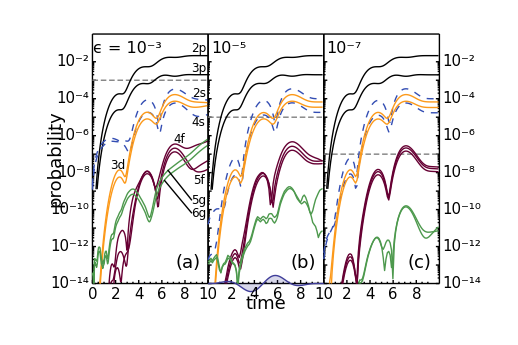

/Users/nevence/Documents/utk/first/threshConv.pdf

```mathematica
ns=Table[n,{n,1,2}];
np=Table[n,{n,9,10}];
nd=Table[n,{n,17,18}];
nf=Table[n,{n,24,26}];
ng=Table[n,{n,30,31}];
nh=Table[n,{n,35,36}];
(*ns={1};
np={9};
nd={17};
nf={24};
ng={30};
*)

laserY=-14;
laserAmp=0.5;
laserPl=Plot[laserAmp*laser[2,1.32,t]+laserY,{t,0,10},
Filling->Axis,
AxesOrigin->{0,laserY}];
x1=9.2;
x2=1.1;
dy=-0.9;
y1a=-2.5;
y1b=y1a+dy;
y1c=y1a+2dy;
y2a=-2.9;
y2b=y2a+dy;
y2c=y2a+2dy;
threshConvFIG=Figure[
{SetOptions[ScaledLabel,FontSize->16],
SetOptions[ManualLabel,FontSize->12],
ScaledLabel[{0.19,0.94},"ϵ = 10^-3"],
ScaledLabel[{0.43,0.94},"10^-5"],
ScaledLabel[{0.7,0.94},"10^-7"],
Multipanel[{{0,1},{0,1}},
{1,3},
FontSize->18,
TickFontSize->15,
XPlotRanges->{0,10},
YPlotRanges->{-14,-0.5},
PanelLetterCorner->{1,-1},
PanelLetterInset->{25,25},
PanelLetterFontSize->18,
TickNudge->{-4,{-3,0},0,{3,0}}
],
(*He 10^-3 vs t*)
FigurePanel[{1,1},
FrameTicks->{Automatic,LogTicks[-14,-2,TickLabelStep->2]},
LabL->"probability",BufferL->5
],
SchemeLine[{{0,-3},{10,-3}},LineColor->Gray,Dashing->Automatic],
RawGraphics[plotBound[boundA,tMAXa,np,PlotStyle->{styleList[[1]]}]],
ManualLabel[{x1,-1.3},"2p"],
ManualLabel[{x1,-2.35},"3p"],RawGraphics[plotBound[boundA,tMAXa,ns,PlotStyle->{styleList[[2]]}]],
ManualLabel[{x1,-3.7},"2s"],
ManualLabel[{x1,-5.3},"4s"],
RawGraphics[plotBound[boundA,tMAXa,nd,PlotStyle->{styleList[[3]]}]],
ManualLabel[{2.2,-7.6},"3d"],
RawGraphics[plotBound[boundA,tMAXa,nf,PlotStyle->{styleList[[4]]}]],
ManualLabel[{7.5,-6.2},"4f"],
ManualLabel[{x1,-8.4},"5f"],
RawGraphics[plotBound[boundA,tMAXa,ng,PlotStyle->{styleList[[5]]}]],
ManualLabel[{x1,-9.5},"5g"],
SchemeLine[{{8.6,-9.5},{6.5,-7.85}}],
ManualLabel[{x1,-10.2},"6g"],
SchemeLine[{{8.6,-10.2},{6.2,-8.4}}],
(*He 10^-5 vs t*)
FigurePanel[{1,2},
FrameTicks->{LinTicks[0.5,10],LogTicks[-14,-2],None,None},
ShowTickLabels->{True,False,False,False},
LabB->"time",BufferB->2.8
],
SchemeLine[{{0,-5},{10,-5}},LineColor->Gray,Dashing->Automatic],
RawGraphics[plotBound[boundB,tMAXb,np,PlotStyle->{styleList[[1]]}]],
RawGraphics[plotBound[boundB,tMAXb,ns,PlotStyle->{styleList[[2]]}]],
RawGraphics[plotBound[boundB,tMAXb,nd,PlotStyle->{styleList[[3]]}]],
RawGraphics[plotBound[boundB,tMAXb,nf,PlotStyle->{styleList[[4]]}]],
RawGraphics[plotBound[boundB,tMAXb,ng,PlotStyle->{styleList[[5]]}]],
RawGraphics[laserPl],
(*He 10^-7 vs t*)
FigurePanel[{1,3},
FrameTicks->{LinTicks[0.5,9.5],LogTicks[-14,-2],None,LogTicks[-14,-2,TickLabelStep->2]},
ShowTickLabels->{True,False,False,True}
],
SchemeLine[{{0,-7},{10,-7}},LineColor->Gray,Dashing->Automatic],
RawGraphics[plotBound[boundC,tMAXc,np,PlotStyle->{styleList[[1]]}]],
RawGraphics[plotBound[boundC,tMAXc,ns,PlotStyle->{styleList[[2]]}]],
RawGraphics[plotBound[boundC,tMAXc,nd,PlotStyle->{styleList[[3]]}]],
RawGraphics[plotBound[boundC,tMAXc,nf,PlotStyle->{styleList[[4]]}]],
RawGraphics[plotBound[boundC,tMAXc,ng,PlotStyle->{styleList[[5]]}]]
},
PlotRange->{{-0.13,1.09},{-0.12,1.01}},ImageSize->72*2*{3.6,2.4}
]
If[export,Export[exportPath<>"threshConv."<>suffix,threshConvFIG]]
Clear[x1,x2,dy,y1a,y1b,y1c,y2a,y2b,y2c];
```

### Figure (version 3)

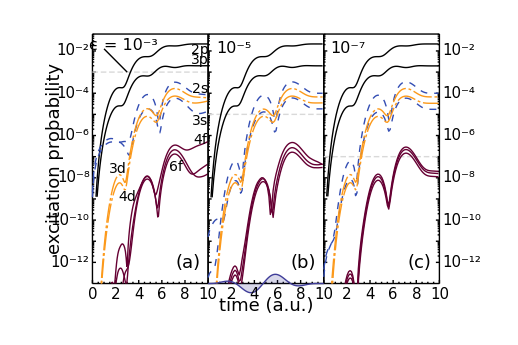

/Users/nevence/Documents/utk/first/threshConv.pdf

```mathematica
ns=Table[n,{n,1,2}];
np=Table[n,{n,9,10}];
nd=Table[n,{n,17,18}];
nf=Table[n,{n,24,26}];
ng=Table[n,{n,30,31}];
nh=Table[n,{n,35,37}];

laserY=-13;
laserAmp=0.5;
laserPl=Plot[laserAmp*laser[2,1.32,t]+laserY,{t,0,10},
Filling->Axis,
AxesOrigin->{0,laserY}];
x1=9.3;
x2=1.1;
dy=-0.5;
y1a=-1.95;
y1b=y1a+dy;
y1c=y1a+2dy;
y2a=-2.9;
y2b=y2a+dy;
y2c=y2a+2dy;
threshConvFIG=Figure[
{SetOptions[ScaledLabel,FontSize->16],
SetOptions[ManualLabel,FontSize->14],
ScaledLabel[{0.18,0.95},"ϵ = 10^-3"],
ScaledLabel[{0.44,0.94},"10^-5"],
ScaledLabel[{0.71,0.94},"10^-7"],
Multipanel[{{0,1},{0,1}},
{1,3},
FontSize->18,
TickFontSize->15,
XPlotRanges->{0,10},
YPlotRanges->{-13,-1.2},
PanelLetterCorner->{1,-1},
PanelLetterInset->{25,25},
PanelLetterFontSize->18,
TickNudge->{-4,{-3,0},0,{3,0}}
],
(*He 10^-3 vs t*)
FigurePanel[{1,1},
FrameTicks->{Automatic,LogTicks[-12,-1,TickLabelStep->2]},
LabL->"excitation probability",BufferL->5
],
SchemeLine[{{0,-3},{10,-3}},LineColor->LightGray,Dashing->Automatic],
RawGraphics[plotBound[boundA,tMAXa,np,PlotStyle->{styleList[[1]]}]],
SchemeLine[{{1.0,-1.9},{3,-3}}],
ManualLabel[{x1,y1a},"2p"],
ManualLabel[{x1,y1b},"3p"],
RawGraphics[plotBound[boundA,tMAXa,ns,PlotStyle->{styleList[[2]]}]],
ManualLabel[{x1,-3.8},"2s"],
ManualLabel[{x1,-5.3},"3s"],
RawGraphics[plotBound[boundA,tMAXa,nd,PlotStyle->{styleList[[3]]}]],
ManualLabel[{2.2,-7.6},"3d"],
ManualLabel[{3.0,-8.9},"4d"],
RawGraphics[plotBound[boundA,tMAXa,nf,PlotStyle->{styleList[[4]]}]],
ManualLabel[{x1,-6.2},"4f"],
ManualLabel[{7.2,-7.5},"6f"],

(*He 10^-5 vs t*)
FigurePanel[{1,2},
FrameTicks->{LinTicks[0.5,10],LogTicks[-12,-1],None,None},
ShowTickLabels->{True,False,False,False},
LabB->"time (a.u.)",BufferB->3
],
SchemeLine[{{0,-5},{10,-5}},LineColor->LightGray,Dashing->Automatic],
RawGraphics[plotBound[boundB,tMAXb,np,PlotStyle->{styleList[[1]]}]],
RawGraphics[plotBound[boundB,tMAXb,ns,PlotStyle->{styleList[[2]]}]],
RawGraphics[plotBound[boundB,tMAXb,nd,PlotStyle->{styleList[[3]]}]],
RawGraphics[plotBound[boundB,tMAXb,nf,PlotStyle->{styleList[[4]]}]],
RawGraphics[laserPl],
(*He 10^-7 vs t*)
FigurePanel[{1,3},
FrameTicks->{LinTicks[0.5,10],LogTicks[-12,-1],None,LogTicks[-12,-1,TickLabelStep->2]},
ShowTickLabels->{True,False,False,True}
],
SchemeLine[{{0,-7},{10,-7}},LineColor->LightGray,Dashing->Automatic],
RawGraphics[plotBound[boundC,tMAXc,np,PlotStyle->{styleList[[1]]}]],
RawGraphics[plotBound[boundC,tMAXc,ns,PlotStyle->{styleList[[2]]}]],
RawGraphics[plotBound[boundC,tMAXc,nd,PlotStyle->{styleList[[3]]}]],
RawGraphics[plotBound[boundC,tMAXc,nf,PlotStyle->{styleList[[4]]}]]
},
PlotRange->{{-0.13,1.09},{-0.12,1.01}},ImageSize->72*2*{3.6,2.4}
]
If[export,Export[exportPath<>"threshConv."<>suffix,threshConvFIG]]
Clear[x1,x2,dy,y1a,y1b,y1c,y2a,y2b,y2c];
```

## dP/dk vs thresh

#### Definition

```mathematica
dPdk[dat_List,fNUM_,hue_]:=Module[{
dk,dθ,dϕ=π,tol=0.00001,kMAX,sum,maxH=5,
points,nk,nθ,θnext,fnext,
k,θ,f,radialCS={}},
(* The task is to integrate the cross section over the angular variables taking the left right symmetries into accout.

The points on the z-axis must be handled carefully, for it needs to represent a cone, but Sin[θ] give it zero width. See journal E pg 18 for a description of the special case Jacobian.
*)
angle[x_,z_]:=If[x≥0,
If[z≠0,If[z>0,ArcTan[x/z],ArcTan[x/z]+π],π/2],
If[z≠0,If[z<0,ArcTan[x/z]+π,ArcTan[x/z]+2π],3π/2]];
xz2rθ[{x_,z_,f___}]:={√(x^2+z^2),angle[x,z],f};
(* Steps 1 & 2
Reflecting the points which don't lie on the z axis
Turning them into polar cordinates and
Sorting them in increasing r *)
points=Sort[xz2rθ/@Join[dat,Cases[dat,{x_,z_,f___}:>{-x,z,f}/;x≠0]]];
nθ=Last[First[Tally[points,Abs[#1[[1]]- #2[[1]]]<tol&]]];
(* Steps 3 & 4
Partitioning the list and then sorting each according to r *)
points2=Sort[#,#1[[2]]<#2[[2]]&]&/@Partition[points,nθ];
nk=Length[points2];
dk = points2[[2,1,1]]-points2[[1,1,1]];
dθ = points2[[1,2,2]]-points2[[1,1,2]];
(*Print["dk = ",dk,"   dθ = ",dθ,"   dϕ = ",dϕ,"   nθ = ",nθ,"   nk = ",nk];*)
(* Step 5
Integrating θ *)
For[m=1,m≤nk,m++,
sum=0;
For[n=1,n≤nθ,n++,
k=points2[[m,n,1]];
θ=points2[[m,n,2]];
θnext=If[n≠nθ,points2[[m,n+1,2]],2π];
fnext=If[n≠nθ,points2[[m,n+1,fNUM]],points2[[m,1,fNUM]]];
If[k>kMAX,kMAX=k];
(*Print[k,"  ",N[θ],"   k dθ = ",k dθ,"    π k Abs[Sin[(θ+θnext)/2]] ",π k Abs[Sin[(θ+θnext)/2]]];*)
f=points2[[m,n,fNUM]];
(*sum+=f*dk*k dθ*dϕ k Abs[Sin[(θ+θnext)/2]];*)
sum+=(f+fnext)/2*k^2 Abs[Sin[(θ+θnext)/2]]dθ dϕ ;
If[n==nθ,AppendTo[radialCS,{k,sum}];
];
];
];
f=Interpolation[Prepend[radialCS,{0,0}]];
Off[Interpolation::inhr];
(* Step 6
Plotting k *)
(*Print["Total Cross Section = ",Total[#[[2]]*dk&/@radialCS]];*)
Plot[f[x],{x,0,radialCS[[-1,1]]},
PlotStyle->styleList[[hue]]
]
]
```

#### Loading Data

```mathematica
If[export,
scale[dat_,p_]:=With[{x=10^p},{#[[1]],#[[2]],Sequence@@(x*#[[3;;]])}&/@dat];
(*ionA=Import[dataDIR<>"H2t5/ion10.dat"];
ionB=Import[dataDIR<>"H2t5/ion20.dat"];
ionC=Import[dataDIR<>"H2t5/ion40.dat"];
ionD=Import[dataDIR<>"H2t5/ion80.dat"];*)
ionA=Import[dataDIR<>"H1e-3/ion.dat"];
ionB=Import[dataDIR<>"H1e-4/ion.dat"];
ionC=Import[dataDIR<>"H1e-5/ion.dat"];
ionD=Import[dataDIR<>"H1e-6/ion.dat"];
(*ionE=Import[dataDIR<>"H1e-7/ion.dat"];*)
Print[Length[ionA]];
Print[Length[ionB]];
Print[Length[ionB]];
Print[Length[ionC]];
Print[Length[ionD]];
tSTEPa=Length[First[ionA]];
tSTEPb=Length[First[ionB]];
tSTEPc=Length[First[ionC]];
tSTEPd=Length[First[ionD]];
kaFIG=dPdk[scale[ionA,2],tSTEPa,5];
kbFIG=dPdk[scale[ionB,2],tSTEPb,4];
kcFIG=dPdk[scale[ionC,2],tSTEPc,3];
kdFIG=dPdk[scale[ionD,2],tSTEPd,2];
ionF=Import[dataDIR<>"He06e-4/ion.dat"];
ionG=Import[dataDIR<>"He06e-5/ion.dat"];
ionH=Import[dataDIR<>"He06e-6/ion.dat"];
ionI=Import[dataDIR<>"He06e-7/ion.dat"];
tSTEPf=Length[First[ionF]];
tSTEPg=Length[First[ionG]];
tSTEPh=Length[First[ionH]];
tSTEPi=Length[First[ionI]];
kfFIG=dPdk[scale[ionF,3],tSTEPf,4];
kgFIG=dPdk[scale[ionG,3],tSTEPg,3];
khFIG=dPdk[scale[ionH,3],tSTEPh,2];
kiFIG=dPdk[scale[ionI,3],tSTEPi,1];
]
```

2050

2050

2050

«2 more identical outputs»

#### Laser Power Spectrum

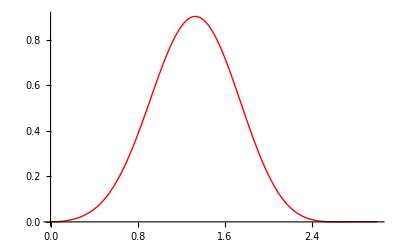

```mathematica
F[plotDat_List,ω_]:=With[{t=#[[1]]&/@ plotDat,f=#[[2]]&/@ plotDat},
 1/(√(2π))Sum[f[[n]] ⅇ^(-I ω t[[n]])(t[[n+1]]-t[[n]]),{n,1,Length[f]-1}]
];
abFT[plotDat_List,ωMAX_,dω_]:=Table[{ω,Abs[F[plotDat,ω]]^2},{ω,0,ωMAX,dω}]
laser[nCycle_,ω_,t_]:=
If[ω t> 0 && (ω t)/(2nCycle)<π,Sin[(ω t)/(2nCycle)]^2 Sin[ω t],0];
lDATA=With[{ω=1.32,nCycles=2},Table[{t,laser[nCycles,ω,t]},{t,0,(2π)/ω*(nCycles+1),0.1}]];
psPLOT=ListLinePlot[abFT[lDATA,3,0.02],
FrameTicks->{{0.5,1,1.5,2,2.5},None,None,None},
PlotStyle->{Red,Thickness[Large]}]
```

#### LevelScheme

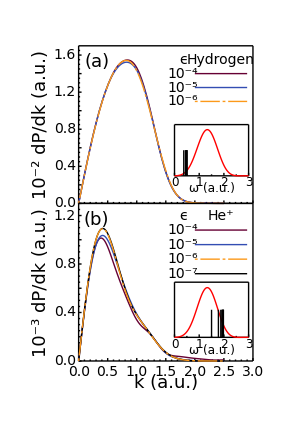

/Users/nevence/Documents/utk/first/threshQ.pdf

```mathematica
dyA=-0.15;
yA0=1.55;
yA1=yA0+dyA;
yA2=yA0+2dyA;
yA3=yA0+3dyA;
yA4=yA0+4dyA;
yA5=yA0+5dyA;
x0=1.8;
x1=2.0;
x2=2.9;
x3=(x2+x1)/2;
dyB=-0.12;
yB0=1.2;
yB1=yB0+dyB;
yB2=yB0+2dyB;
yB3=yB0+3dyB;
yB4=yB0+4dyB;
yB5=yB0+5dyB;
threshQFIG=Figure[{
SetOptions[ManualLabel,FontSize->14],
Multipanel[
{{0,1},{0,1}},
{2,1},
XPlotRanges->{0,3},
YPlotRanges->{{0,1.7},{0,1.3}},
XFrameLabels->"k (a.u.)",
OrientationL->Vertical,
BufferL->5,
BufferB->3,
FontSize->18,
TickFontSize->14,
TickNudge->{-4,{-3,0},0,0},
PanelLetterInset->{22,20}
],
FigurePanel[{1,1},
FrameTicks->{Automatic,LinTicks[0,1.69,0.2,4,TickLabelStep->2]},
LabL->"10^-2 dP/dk (a.u.)"
],

RawGraphics[kbFIG],
RawGraphics[kcFIG],
RawGraphics[kdFIG],
ManualLabel[{x3,yA0},"Hydrogen"],
RawGraphics[Graphics[{
Sequence@@styleList[[4]],Line[{{x1,yA1},{x2,yA1}}],
Sequence@@styleList[[3]],Line[{{x1,yA2},{x2,yA2}}],
Sequence@@styleList[[2]],Line[{{x1,yA3},{x2,yA3}}]
}]],
ManualLabel[{x0,yA0},"ϵ"],
ManualLabel[{x0,yA1},"10^-4"],
ManualLabel[{x0,yA2},"10^-5"],
ManualLabel[{x0,yA3},"10^-6"],

ScaledFigurePanel[
{{0.55,0.975},{0.175,0.5}},
PlotRange->{{0,3},{0,1}},
FrameTicks->{LinTicks[0,3,1,2],None},
TickFontSize->12,
LabB->"ω (a.u.)",BufferB->2.5
],
RawGraphics[psPLOT],
With[{en=0.5},RawGraphics[Graphics[
Table[Line[{{en(1-1/n^2),0},{en(1-1/n^2),0.5}}],{n,2,10}]
]]],

FigurePanel[{2,1},
FrameTicks->{Automatic,LinTicks[0,1.5,0.2,4,TickLabelStep->2]},
LabL->"10^-3 dP/dk (a.u.)"
],
RawGraphics[kfFIG],
RawGraphics[kgFIG],
RawGraphics[kiFIG],
RawGraphics[khFIG],

ManualLabel[{x3,yB0},"He^+"],
RawGraphics[Graphics[{
Sequence@@styleList[[1]],Line[{{x1,yB4},{x2,yB4}}],
Sequence@@styleList[[2]],Line[{{x1,yB3},{x2,yB3}}],
Sequence@@styleList[[3]],Line[{{x1,yB2},{x2,yB2}}],
Sequence@@styleList[[4]],Line[{{x1,yB1},{x2,yB1}}],
}]],
ManualLabel[{x0,yB0},"ϵ"],
ManualLabel[{x0,yB1},"10^-4"],
ManualLabel[{x0,yB2},"10^-5"],
ManualLabel[{x0,yB3},"10^-6"],
ManualLabel[{x0,yB4},"10^-7"],
ScaledFigurePanel[
{{0.55,0.975},{0.15,0.5}},
PlotRange->{{0,3},{0,1}},
FrameTicks->{LinTicks[0,3,1,2],None},
LabB->"ω (a.u.)",BufferB->2.5
],
With[{en=2.0,ω=1.32},Sequence@@{
RawGraphics[psPLOT],
RawGraphics[Graphics[
Table[Line[{{en(1-1/n^2),0},{en(1-1/n^2),0.5}}],{n,2,10}]
]]}]
},
PlotRange->{{-0.3,1.05},{-0.1,1.02}},ImageSize->72*{4,6}
]
If[export,Export[exportPath<>"threshQ."<>suffix,threshQFIG]]
```

## tScale

### Prereq

```mathematica
dPdk[dat_List,fNUM_,hue_]:=Module[{
dk,dθ,dϕ=π,tol=0.00001,kMAX,sum,maxH=5,
points,nk,nθ,θnext,fnext,
k,θ,f,radialCS={}},
(* The task is to integrate the cross section over the angular variables taking the left right symmetries into accout.

The points on the z-axis must be handled carefully, for it needs to represent a cone, but Sin[θ] give it zero width. See journal E pg 18 for a description of the special case Jacobian.
*)
angle[x_,z_]:=If[x≥0,
If[z≠0,If[z>0,ArcTan[x/z],ArcTan[x/z]+π],π/2],
If[z≠0,If[z<0,ArcTan[x/z]+π,ArcTan[x/z]+2π],3π/2]];
xz2rθ[{x_,z_,f___}]:={√(x^2+z^2),angle[x,z],f};
(* Steps 1 & 2
Reflecting the points which don't lie on the z axis
Turning them into polar cordinates and
Sorting them in increasing r *)
points=Sort[xz2rθ/@Join[dat,Cases[dat,{x_,z_,f___}:>{-x,z,f}/;x≠0]]];
nθ=Last[First[Tally[points,Abs[#1[[1]]- #2[[1]]]<tol&]]];
(* Steps 3 & 4
Partitioning the list and then sorting each according to r *)
points2=Sort[#,#1[[2]]<#2[[2]]&]&/@Partition[points,nθ];
nk=Length[points2];
dk = points2[[2,1,1]]-points2[[1,1,1]];
dθ = points2[[1,2,2]]-points2[[1,1,2]];
(*Print["dk = ",dk,"   dθ = ",dθ,"   dϕ = ",dϕ,"   nθ = ",nθ,"   nk = ",nk];*)
(* Step 5
Integrating θ *)
For[m=1,m≤nk,m++,
sum=0;
For[n=1,n≤nθ,n++,
k=points2[[m,n,1]];
θ=points2[[m,n,2]];
θnext=If[n≠nθ,points2[[m,n+1,2]],2π];
fnext=If[n≠nθ,points2[[m,n+1,fNUM]],points2[[m,1,fNUM]]];
If[k>kMAX,kMAX=k];
(*Print[k,"  ",N[θ],"   k dθ = ",k dθ,"    π k Abs[Sin[(θ+θnext)/2]] ",π k Abs[Sin[(θ+θnext)/2]]];*)
f=points2[[m,n,fNUM]];
(*sum+=f*dk*k dθ*dϕ k Abs[Sin[(θ+θnext)/2]];*)
sum+=(f+fnext)/2*k^2 Abs[Sin[(θ+θnext)/2]]dθ dϕ ;
If[n==nθ,AppendTo[radialCS,{k,sum}];
];
];
];
f=Interpolation[Prepend[radialCS,{0,0}]];
Off[Interpolation::inhr];
(* Step 6
Plotting k *)
(*Print["Total Cross Section = ",Total[#[[2]]*dk&/@radialCS]];*)
Plot[f[x],{x,0,radialCS[[-1,1]]},

(*Evaluate@Sequence[csOPTS[hue]],*)
PlotStyle->styleList[[hue]]
]
]

laser[nCycle_,ω_,t_]:=
If[ω t> 0 && (ω t)/(2nCycle)<π,Sin[(ω t)/(2nCycle)]^2 Sin[ω t],0];
laserY=-0.5;
laserAmp=0.004;
laserPl=Plot[laserAmp*laser[2,1.32,t]+laserY,{t,0,10},
Filling->Axis,
AxesOrigin->{0,laserY}];

eDiff[master_,slave_,opts___]:=Module[{f=Interpolation[master]},
ListLinePlot[{#[[1]],100(f[#[[1]]]-#[[2]])/f[#[[1]]]}&/@slave,PlotRange->All,opts]
]

If[export,
scale[dat_,p_]:=With[{x=10^p},{#[[1]],#[[2]],Sequence@@(x*#[[3;;]])}&/@dat];
enA=Union@Import[dataDIR<>"H2t1/energy.dat"];
enB=Union@Import[dataDIR<>"H2t5/energy.dat"];
enC=Union@Import[dataDIR<>"H2t8/energy.dat"];
enD=Union@Import[dataDIR<>"H2t9/energy.dat"];
enE=Union@Import[dataDIR<>"H2t10/energy.dat"];
enF=Union@Import[dataDIR<>"H2t11/energy.dat"];
enG=Union@Import[dataDIR<>"H2t12.5/energy.dat"];
enH=Union@Import[dataDIR<>"H2t15/energy.dat"];
enI=Union@Import[dataDIR<>"H2t17.5/energy.dat"];
enJ=Union@Import[dataDIR<>"H2t20/energy.dat"];
ionA=Union@Import[dataDIR<>"H2t1/ion.dat"];
ionB=Union@Import[dataDIR<>"H2t5/ion40.dat"];
ionE=Union@Import[dataDIR<>"H2t10/ion.dat"];
ionF=Union@Import[dataDIR<>"H2t12.5/ion.dat"];


Print[Length[ionA]];
Print[Length[ionB]];
Print[Length[ionE]];
Print[Length[ionF]];
tSTEPa=Length[First[ionA]];
tSTEPb=Length[First[ionB]];
tSTEPe=Length[First[ionE]];
tSTEPf=Length[First[ionF]];
kaFIG=dPdk[scale[ionA,2],tSTEPa,1];
kbFIG=dPdk[scale[ionB,2],tSTEPb,4];
keFIG=dPdk[scale[ionE,2],tSTEPe,3];
kfFIG=dPdk[scale[ionF,2],tSTEPf,2];
]
```

2050

2050

2050

«1 more identical outputs»

### Take 1

```mathematica
enA=Union@Import[dataDIR<>"H2t.5/energy2.dat"];
enB=Union@Import[dataDIR<>"H2t2/energy.dat"];
enC=Union@Import[dataDIR<>"H2t5/energy.dat"];
enD=Union@Import[dataDIR<>"H2t10/energy.dat"];
enE=Union@Import[dataDIR<>"H2t12.5/energy.dat"];
enF=Union@Import[dataDIR<>"H2t15/energy.dat"];
enG=Union@Import[dataDIR<>"H2t17.5/energy.dat"];
enH=Union@Import[dataDIR<>"H2t20/energy.dat"];


laser[nCycle_,ω_,t_]:=
If[ω t> 0 && (ω t)/(2nCycle)<π,Sin[(ω t)/(2nCycle)]^2 Sin[ω t],0];
laserY=-0.5;
laserAmp=0.004;
laserPl=Plot[laserAmp*laser[2,1.32,t]+laserY,{t,0,10},
Filling->Axis,
AxesOrigin->{0,laserY}];
eDiff[master_,slave_,opts___]:=Module[{f=Interpolation[master]},
ListLinePlot[{#[[1]],100(f[#[[1]]]-#[[2]])/f[#[[1]]]}&/@slave,PlotRange->All,opts]
]
scale[dat_,p_]:=With[{x=10^p},{#[[1]],x #[[2]]}&/@dat];
```

```mathematica
en0=enA[[-1,2]];
rErr[dt_,en_]:={dt,(en0-en)/en0};
en2=rErr[2,enB[[-1,2]]];
en3=rErr[5,enC[[-1,2]]];
en4=rErr[10,enD[[-1,2]]];
en5=rErr[12.5,enE[[-1,2]]];
en6=rErr[15,enF[[-1,2]]];
en7=rErr[17.5,enG[[-1,2]]];
en8=rErr[20,enH[[-1,2]]];
enVStScale={en2,en3,en4,en5,en6,en7};
expr=a x^p;
coefs={a,p};
fitB[x_]:=Evaluate[expr/.FindFit[scale[enVStScale,2],expr,coefs,x]]
FindFit[scale[enVStScale,2],expr,coefs,x]

dy=-0.0045;
y0=-0.44;
y1=y0+dy;
y2=y0+2dy;
y3=y0+3dy;
y4=y0+4dy;
y5=y0+5dy;
y6=y0+6dy;
y7=y0+7dy;
y8=y0+8dy;
x1=1;
x2=1.75;
x3=4;

tSclConvFIG=Figure[
{
(*exH vs cut*)
Multipanel[
{{0,1},{0,1}},
{2,2},
XPlotRanges->{0,10},
FontSize->18,
TickFontSize->15,
TickNudge->{-4,{-2,0},0,{3,0}}
],
SetOptions[ManualLabel,FontSize->15],
ScaledLabel[{0.5,0.023},"time [atomic units]",FontSize->18],
FigurePanel[{1,1},
YPlotRange->{-0.5,-0.43},
PanelAdjustments->{{0,0},{1,0}},
LabL->"Energy H",BufferL->5,
FrameTicks->{LinTicks[0,9.75,2,4],LinTicks[-0.5,-0.43,0.02,4],None,None},
ShowFrameLabels->{True,True,False,False},
ShowTickLabels-> {True,True,False,False},
Order->Vertical
],
ManualLabel[{x1,y0},"dt"],
ManualLabel[{x1,y1},"0.5"],
ManualLabel[{x1,y2},"2"],
ManualLabel[{x1,y3},"5"],
ManualLabel[{x1,y4},"10"],
ManualLabel[{x1,y5},"12.5"],
ManualLabel[{x1,y6},"15"],
RawGraphics[Graphics[{
Sequence@@styleList[[1]],Line[{{x2,y1},{x3,y1}}],
Sequence@@styleList[[2]],Line[{{x2,y2},{x3,y2}}],
Sequence@@styleList[[3]],Line[{{x2,y3},{x3,y3}}],
Sequence@@styleList[[4]],Line[{{x2,y4},{x3,y4}}],
Sequence@@styleList[[5]],Line[{{x2,y5},{x3,y5}}],
Sequence@@styleList[[6]],Line[{{x2,y6},{x3,y6}}]
}]],
RawGraphics[ListLinePlot[{enA,enB,enC,enD,enE,enF},
PlotStyle->{styleList[[1]],styleList[[2]],styleList[[3]],styleList[[4]],styleList[[5]],styleList[[6]]},
PlotRange->All]],
RawGraphics[laserPl],
(**)
FigurePanel[{1,2},
YPlotRange->{0,3.5},
XPlotRange->{0.5,15},
LabR->"% Error",BufferR->4,
FontSize->17,
LabB->"dt [in units of t_crit]",BufferB->3,
FontSize->18,
FrameTicks->{LinTicks[0,14,5.,4],None,None,LinTicks[0,3,1,4]},
ShowFrameLabels->{True,False,False,True},
ShowTickLabels-> {True,False,False,True}
],
RawGraphics[Show[
ListPlot[scale[enVStScale,2],PlotStyle->PointSize[0.01]],
Plot[fitB[dt],{dt,0,20},PlotRange->All]]],
(**)
FigurePanel[{2,2},
YPlotRange->{-0.1,0.95},
LabR->"% Error",BufferR->4,
FrameTicks->{Automatic,None,None,LinTicks[0,0.9,0.2,2]},
ShowTickLabels->{True,False,False,True},
ShowFrameLabels->{True,False,False,True},
PanelLetter->"(c)",
PanelLetterInset->{20,25}
],
SchemeLine[{{0,0},{10,0}}],
RawGraphics[eDiff[enA,enB[[12;;-5]],PlotStyle->styleList[[2]]]],
RawGraphics[eDiff[enA,enC[[10;;-2]],PlotStyle->styleList[[3]]]],
RawGraphics[eDiff[enA,enD[[11;;-5]],PlotStyle->styleList[[4]]]],
RawGraphics[eDiff[enA,enE[[11;;-5]],PlotStyle->styleList[[5]]]]

},
PlotRange->{{-0.14,1.15},{-0.12,1.05}},ImageSize->72*2*{3.6,2.4}
]
If[export,Export[exportPath<>"tSclConv."<>suffix,tSclConvFIG]]
```

### Take 2

```mathematica
laser[nCycle_,ω_,t_]:=
If[ω t> 0 && (ω t)/(2nCycle)<π,Sin[(ω t)/(2nCycle)]^2 Sin[ω t],0];
laserY=-0.5;
laserAmp=0.004;
laserPl=Plot[laserAmp*laser[2,1.32,t]+laserY,{t,0,10},
Filling->Axis,
AxesOrigin->{0,laserY}];
eDiff[master_,slave_,opts___]:=Module[{f=Interpolation[master]},
ListLinePlot[{#[[1]],100(f[#[[1]]]-#[[2]])/f[#[[1]]]}&/@slave,PlotRange->All,opts]
]
scale[dat_,p_]:=With[{x=10^p},{#[[1]],x #[[2]]}&/@dat];
enA=Union@Import[dataDIR<>"H2/energy.dat"];
enB=Union@Import[dataDIR<>"H2t2/energy.dat"];
enC=Union@Import[dataDIR<>"H2t5/energy.dat"];
enD=Union@Import[dataDIR<>"H2t10/energy.dat"];
enE=Union@Import[dataDIR<>"H2t12.5/energy.dat"];
enF=Union@Import[dataDIR<>"H2t15/energy.dat"];
dy=-0.0045;
y0=-0.45;
y1=y0+dy;
y2=y0+2dy;
y3=y0+3dy;
y4=y0+4dy;
y5=y0+5dy;
y6=y0+6dy;
y7=y0+7dy;
y8=y0+8dy;
x1=1;
x2=1.75;
x3=4;

tSclConvFIG=Figure[{
FigurePanel[{{0,1},{0,1}},
PlotRange->{{0,10},{-0.5,-0.445}},
PanelAdjustments->{{0,0},{1,0}},
LabL->"Energy H",BufferL->5,
LabB->"time [atomic units]",BufferB->5,
FrameTicks->{LinTicks[0,9.75,2,4],LinTicks[-0.5,-0.43,0.02,4],None,None},
ShowFrameLabels->{True,True,False,False},
ShowTickLabels-> {True,True,False,False},
Order->Vertical,
FontSize->18,
TickFontSize->15,
TickNudge->{-4,{-2,0},0,{3,0}}
],
SetOptions[ManualLabel,FontSize->15],
ManualLabel[{x1,y0},"dt"],
ManualLabel[{x1,y1},"1"],
ManualLabel[{x1,y2},"5"],
ManualLabel[{x1,y3},"10"],
ManualLabel[{x1,y4},"12.5"],
(*ManualLabel[{x1,y6},"15"],*)
RawGraphics[Graphics[{
Sequence@@styleList[[1]],Line[{{x2,y1},{x3,y1}}],
Sequence@@styleList[[2]],Line[{{x2,y2},{x3,y2}}],
Sequence@@styleList[[3]],Line[{{x2,y3},{x3,y3}}],
Sequence@@styleList[[4]],Line[{{x2,y4},{x3,y4}}](*,
Sequence@@styleList[[5]],Line[{{x2,y5},{x3,y5}}],
Sequence@@styleList[[6]],Line[{{x2,y6},{x3,y6}}]*)
}]],
RawGraphics[ListLinePlot[{enA,enC,enD,enE},
PlotStyle->{styleList[[1]],styleList[[2]],styleList[[3]],styleList[[4]],styleList[[5]],styleList[[6]]},
PlotRange->All]],
RawGraphics[laserPl]
},PlotRange->{{-0.13,1.02},{-0.1,1.02}},ImageSize->72*2*{3.6,2.4}
]
If[export,Export[exportPath<>"tSclConv."<>suffix,tSclConvFIG]]
```

### Take 3

```mathematica
dy=-0.0045;
y0=-0.45;
y1=y0+dy;
y2=y0+2dy;
y3=y0+3dy;
y4=y0+4dy;
x1=1;
x2=2;
x3=4.5;

tSclConvFIG=Figure[{
Multipanel[{{0,1},{0,1}},{1,2},
TickFontSize->10,
FontSize->12,
PanelLetterFontSize->17
],
SetOptions[ManualLabel,FontSize->10],
FigurePanel[{1,1},
PlotRange->{{0,10},{-0.5,-0.445}},
LabL->"Energy H",BufferL->5.5,
LabB->"time [atomic units]",BufferB->3,
FrameTicks->{LinTicks[0,9.75,2,4],LinTicks[-0.5,-0.43,0.02,4],None,None},
ShowFrameLabels->{True,True,False,False},
ShowTickLabels-> {True,True,False,False},
Order->Vertical,
TickNudge->{-3,{-2,0},0,{3,0}},
PanelLetterCorner->{1,1}
],

ManualLabel[{x1,y0},"dt"],
ManualLabel[{x1,y1},"1"],
ManualLabel[{x1,y2},"5"],
ManualLabel[{x1,y3},"10"],
ManualLabel[{x1,y4},"12.5"],
RawGraphics[Graphics[{
Sequence@@styleList[[1]],Line[{{x2,y1},{x3,y1}}],
Sequence@@styleList[[2]],Line[{{x2,y2},{x3,y2}}],
Sequence@@styleList[[3]],Line[{{x2,y3},{x3,y3}}],
Sequence@@styleList[[4]],Line[{{x2,y4},{x3,y4}}]
}]],
RawGraphics[ListLinePlot[{enA,enC,enD,enE},
PlotStyle->{styleList[[1]],styleList[[2]],styleList[[3]],styleList[[4]],styleList[[5]],styleList[[6]]},
PlotRange->All]],
RawGraphics[laserPl],
FigurePanel[{1,2},
PlotRange->{{0,2.5},{0,1.7}},
ShowFrameLabels->{True,False,False,True},
ShowTickLabels-> {True,False,False,True},
FrameTicks->{LinTicks[0,2.5,1.0,4],None,None,LinTicks[0,1.75,0.5,5]},
LabB->"q [atomic units]",BufferB->3,
LabR->"dP/dq",BufferR->4.5,OrientationR->Horizontal,
TickNudge->{-3,0,0,{2,0}}
],
RawGraphics[kaFIG],
RawGraphics[kbFIG],
RawGraphics[kcFIG],
RawGraphics[kdFIG]
},PlotRange->{{-0.2,1.17},{-0.17,1.02}},ImageSize->72*{4,2.5}
]

If[export,Export[exportPath<>"tSclConv."<>suffix,tSclConvFIG]]
```

### Take 4

{{5,0.000097761},{8,0.000226041},{9,0.000340789},{10,0.000761797},{11,0.00176652},{12.5,0.00570756},{15,0.0273911}}

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{a→1.76923×10^-10,p→8.66422}

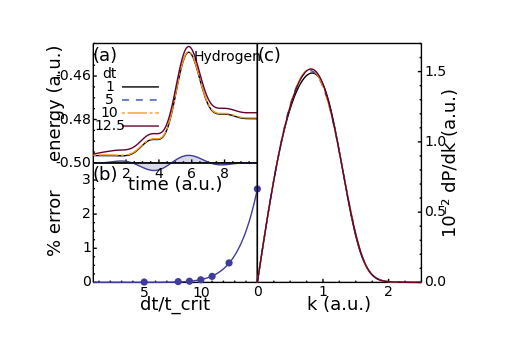

/Users/nevence/Documents/utk/first/tSclConv.pdf

/Users/nevence/Documents/utk/qmprop/qmprop8-img/tSclConv.pdf

```mathematica
en0=enA[[-1,2]];
tLIST={1,5,8,9,10,11,12.5,15,17.5,20}; (*Length10*)
rErr[dt_,en_]:={dt,(en0-en)/en0};(*relative Error*)
en2=rErr[tLIST[[2]],enB[[-1,2]]];
en3=rErr[tLIST[[3]],enC[[-1,2]]];
en4=rErr[tLIST[[4]],enD[[-1,2]]];
en5=rErr[tLIST[[5]],enE[[-1,2]]];
en6=rErr[tLIST[[6]],enF[[-1,2]]];
en7=rErr[tLIST[[7]],enG[[-1,2]]];
en8=rErr[tLIST[[8]],enH[[-1,2]]]; (*abarrant*)
en9=rErr[tLIST[[9]],enI[[-1,2]]]; (*abarrant*)

enVStScale={en2,en3,en4,en5,en6,en7,en8};
Print[enVStScale];
expr=a x^p;
coefs={a,p};
scale[dat_,p_]:=With[{x=10^p},{#[[1]],Sequence@@(x*#[[2;;]])}&/@dat];
fitB[x_]:=Evaluate[expr/.FindFit[scale[enVStScale,2],expr,coefs,x]]
FindFit[scale[enVStScale,2],expr,coefs,x]

dy=-0.006;
y0=-0.459;
y1=y0+dy;
y2=y0+2dy;
y3=y0+3dy;
y4=y0+4dy;
y5=y0+5dy;
y6=y0+6dy;
y7=y0+7dy;
y8=y0+8dy;
x1=1;
x2=1.75;
x3=4;

tSclConvFIG=Figure[
{
(*exH vs cut*)
Multipanel[
{{0,1},{0,1}},
{2,2},
FontSize->18,
TickFontSize->14,
TickNudge->{-4,{-2,0},0,{3,0}}
],
SetOptions[ManualLabel,FontSize->14],
(*Energy vs Time*)
FigurePanel[{1,1},
PlotRange->{{0,10},{-0.5,-0.445}},
LabL->"energy (a.u.)",BufferL->5,
LabB->"time (a.u.)",BufferB->3,
FrameTicks->{LinTicks[2,9.75,2,4],LinTicks[-0.5,-0.43,0.02,4],None,None},
ShowFrameLabels->{True,True,False,False},
ShowTickLabels-> {True,True,False,False},
Order->Vertical
],
ManualLabel[{x1,y0},"dt"],
ManualLabel[{x1,y1},"1"],
ManualLabel[{x1,y2},"5"],
ManualLabel[{x1,y3},"10"],
ManualLabel[{x1,y4},"12.5"],

ManualLabel[{8.2,-0.451},"Hydrogen"],
RawGraphics[Graphics[{
Sequence@@styleList[[1]],Line[{{x2,y1},{x3,y1}}],
Sequence@@styleList[[2]],Line[{{x2,y2},{x3,y2}}],
Sequence@@styleList[[3]],Line[{{x2,y3},{x3,y3}}],
Sequence@@styleList[[4]],Line[{{x2,y4},{x3,y4}}]
}]],
RawGraphics[ListLinePlot[{enA,enE,enG},
PlotStyle->{styleList[[1]],styleList[[3]],styleList[[4]]},
PlotRange->All]],
RawGraphics[laserPl],
(*Error vs dt*)
FigurePanel[{2,1},
PlotRange->{{0.5,15},{0,3.5}},
LabL->"% error",BufferL->5,
LabB->"dt/t_crit",BufferB->3,
PanelLetter->"(b)",
FrameTicks->{LinTicks[0,14,5.,5],LinTicks[0,3,1,4]}
],
RawGraphics[ListPlot[scale[enVStScale,2],PlotStyle->PointSize[0.01]]],
RawGraphics[Plot[fitB[dt],{dt,0,20},PlotRange->All]],
(*dP/dk vs ϵ*)
FigurePanel[{1,2},
PlotRange->{{0,2.5},{0,1.7}},
PanelAdjustments->{{0,0},{1,0}},
PanelLetter->"(c)",
ShowFrameLabels->{True,False,False,True},
ShowTickLabels-> {True,False,False,True},
FrameTicks->{LinTicks[0,2.5,1.0,4],None,None,LinTicks[0,1.75,0.5,5]},
LabB->"k (a.u.)",BufferB->3,
LabR->"10^-2 dP/dk (a.u.)",BufferR->4,
TickNudge->{-3,0,0,{3,0}}
],
RawGraphics[kaFIG],
RawGraphics[kbFIG],
RawGraphics[keFIG],
RawGraphics[kfFIG]
},
PlotRange->{{-0.14,1.15},{-0.13,1.05}},ImageSize->72*2*{3.6,2.4}
]
If[export,Export[exportPath<>"tSclConv."<>suffix,tSclConvFIG]]
If[export,Export["/Users/nevence/Documents/utk/qmprop/qmprop8-img/tSclConv."<>suffix,tSclConvFIG]]
```

### Take 4 (w/o a.u. labels)

{{5,0.000097761},{8,0.000226041},{9,0.000340789},{10,0.000761797},{11,0.00176652},{12.5,0.00570756},{15,0.0273911}}

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{a→1.76923×10^-10,p→8.66422}

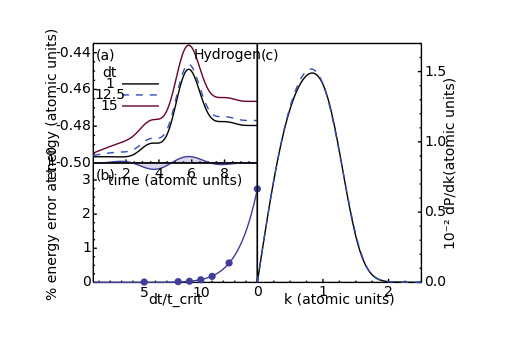

/Users/nevence/Documents/utk/jun/tdse/qmprop8-img/tSclConv.pdf

```mathematica
en0=enA[[-1,2]];
tLIST={1,5,8,9,10,11,12.5,15,17.5,20}; (*Length10*)
rErr[dt_,en_]:={dt,(en0-en)/en0};(*relative Error*)
en2=rErr[tLIST[[2]],enB[[-1,2]]];
en3=rErr[tLIST[[3]],enC[[-1,2]]];
en4=rErr[tLIST[[4]],enD[[-1,2]]];
en5=rErr[tLIST[[5]],enE[[-1,2]]];
en6=rErr[tLIST[[6]],enF[[-1,2]]];
en7=rErr[tLIST[[7]],enG[[-1,2]]];
en8=rErr[tLIST[[8]],enH[[-1,2]]]; (*abarrant*)
en9=rErr[tLIST[[9]],enI[[-1,2]]]; (*abarrant*)

enVStScale={en2,en3,en4,en5,en6,en7,en8};
Print[enVStScale];
expr=a x^p;
coefs={a,p};
scale[dat_,p_]:=With[{x=10^p},{#[[1]],Sequence@@(x*#[[2;;]])}&/@dat];
fitB[x_]:=Evaluate[expr/.FindFit[scale[enVStScale,2],expr,coefs,x]]
FindFit[scale[enVStScale,2],expr,coefs,x]

dy=-0.006;
y0=-0.451;
y1=y0+dy;
y2=y0+2dy;
y3=y0+3dy;
y4=y0+4dy;
y5=y0+5dy;
y6=y0+6dy;
y7=y0+7dy;
y8=y0+8dy;
x1=1;
x2=1.75;
x3=4;

tSclConvFIG=Figure[
{
(*exH vs cut*)
Multipanel[
{{0,1},{0,1}},
{2,2},
FontSize->14,
TickFontSize->14,
TickNudge->{-4,{-2,0},0,{3,0}}
],
SetOptions[ManualLabel,FontSize->14],
(*Energy vs Time*)
FigurePanel[{1,1},
PlotRange->{{0,10},{-0.5,-0.435}},
LabL->"energy (atomic units)",BufferL->7,
LabB->"time (atomic units)",BufferB->3,
FrameTicks->{LinTicks[2,9.75,2,4],LinTicks[-0.5,-0.43,0.02,4],None,None},
ShowFrameLabels->{True,True,False,False},
ShowTickLabels-> {True,True,False,False},
Order->Vertical
],
ManualLabel[{x1,y0},"dt"],
ManualLabel[{x1,y1},"1"],
ManualLabel[{x1,y2},"12.5"],
ManualLabel[{x1,y3},"15"],

ManualLabel[{8.2,-0.441},"Hydrogen"],
RawGraphics[Graphics[{
Sequence@@styleList[[1]],Line[{{x2,y1},{x3,y1}}],
Sequence@@styleList[[2]],Line[{{x2,y2},{x3,y2}}],
Sequence@@styleList[[4]],Line[{{x2,y3},{x3,y3}}]
}]],
RawGraphics[ListLinePlot[{enA,enG,enH},
PlotStyle->{styleList[[1]],styleList[[2]],styleList[[4]]},
PlotRange->All]],
RawGraphics[laserPl],
(*Error vs dt*)
FigurePanel[{2,1},
PlotRange->{{0.5,15},{0,3.5}},
LabL->"% energy error at t=0",BufferL->7,
LabB->"dt/t_crit",BufferB->3,
PanelLetter->"(b)",
FrameTicks->{LinTicks[0,14,5.,5],LinTicks[0,3,1,4]}
],
RawGraphics[ListPlot[scale[enVStScale,2],PlotStyle->PointSize[0.01]]],
RawGraphics[Plot[fitB[dt],{dt,0,20},PlotRange->All]],
(*dP/dk vs ϵ*)
FigurePanel[{1,2},
PlotRange->{{0,2.5},{0,1.7}},
PanelAdjustments->{{0,0},{1,0}},
PanelLetter->"(c)",
ShowFrameLabels->{True,False,False,True},
ShowTickLabels-> {True,False,False,True},
FrameTicks->{LinTicks[0,2.5,1.0,4],None,None,LinTicks[0,1.75,0.5,5]},
LabB->"k (atomic units)",BufferB->3,
LabR->"10^-2 dP/dk(atomic units)",BufferR->5,
TickNudge->{-3,0,0,{3,0}}
],
RawGraphics[kaFIG],
(*RawGraphics[keFIG],*)
RawGraphics[kfFIG]
},
PlotRange->{{-0.14,1.15},{-0.13,1.05}},ImageSize->72*2*{3.6,2.4}
]
If[export,Export[exportPath<>"tSclConv."<>suffix,tSclConvFIG]]
```

## Energy & Excitation (large multipanel)

#### Prereq

```mathematica
enA=Union[Import[dataDIR<>"H3/energy.dat"]];
enB=Union[Import[dataDIR<>"H19/energy.dat"]];
enC=Union[Import[dataDIR<>"H1/energy.dat"]];
enD=Union[Import[dataDIR<>"H05e-7/energy.dat"]];
hEn0CutDAT={
{0.3,enA[[1,2]]},
{0.187,enB[[1,2]]},
{0.1,enC[[1,2]]},
{0.05,enD[[1,2]]},
{0.025,-0.499990154}
};
hEnDCutDAT={
{0.3,Last[enA][[2]]-First[enA][[2]]},
{0.187,Last[enB][[2]]-First[enB][[2]] },
{0.1,Last[enC][[2]]-First[enC][[2]]},
{0.05,Last[enD][[2]]-First[enD][[2]]}
};

enE=Union[Import[dataDIR<>"He2/energy.dat"]];
enF=Union[Import[dataDIR<>"He12e-7/energy.dat"]];
enG=Union[Import[dataDIR<>"He08/energy.dat"]];
enH=Union[Import[dataDIR<>"He06e-7/energy.dat"]];
enI=Union[Import[dataDIR<>"He05/energy.dat"]];
heEn0CutDAT={
{0.20,enE[[1,2]]},
{0.12,enF[[1,2]]},
{0.08,enG[[1,2]]},
{0.06,enH[[1,2]]},
{0.05,enI[[1,2]]}
};
heEnDCutDAT={
{0.20,Last[enE][[2]]-First[enE][[2]]},
{0.12,Last[enF][[2]]-First[enF][[2]]},
{0.08,Last[enG][[2]]-First[enG][[2]] },
{0.06,Last[enH][[2]]-First[enH][[2]] },
{0.05,Last[enI][[2]]-First[enI][[2]]}
};
minusOne[lst_List]:={#[[1]],1-(#[[2]])^2}&/@lst;

totalExA=minusOne@Union[Import[dataDIR<>"H3/overlap.dat"]];
totalExB=minusOne@Union[Import[dataDIR<>"H19/overlap.dat"]];
totalExC=minusOne@Union[Import[dataDIR<>"H1/overlap.dat"]];
totalExD=minusOne@Union[Import[dataDIR<>"H05e-7/overlap.dat"]];
totalExE=minusOne@Union[Import[dataDIR<>"He2/overlap.dat"]];
totalExF=minusOne@Union[Import[dataDIR<>"He12e-7/overlap.dat"]];
totalExG=minusOne@Union[Import[dataDIR<>"He08/overlap.dat"]];
totalExH=minusOne@Union[Import[dataDIR<>"He06e-7/overlap.dat"]];
exHVcutDAT=Transpose[{{0.3,0.187,0.1,0.05},#[[-1,2]]&/@{totalExA,totalExB,totalExC,totalExD}}]
exHeVcutDAT=Transpose[{{0.2,0.12,0.08,0.059},Last/@Last/@{totalExE,totalExF,totalExG,totalExH}}]

heStyleList=styleList[[5;;]];
hStyleList=styleList[[;;4]];
laser[nCycle_,ω_,t_]:=
If[ω t> 0 && (ω t)/(2nCycle)<π,Sin[(ω t)/(2nCycle)]^2 Sin[ω t],0]
laserY=-0.0;
laserAmp=0.003;
laserPl=Plot[laserAmp*laser[2,1.32,t]+laserY,{t,0,10},
Filling->Axis,
AxesOrigin->{0,laserY}];
```

{{0.3,0.0226935},{0.187,0.0232966},{0.1,0.0235173},{0.05,0.0235571}}

{{0.2,0.0304171},{0.12,0.0268144},{0.08,0.025795},{0.059,0.0254842}}

#### Figure

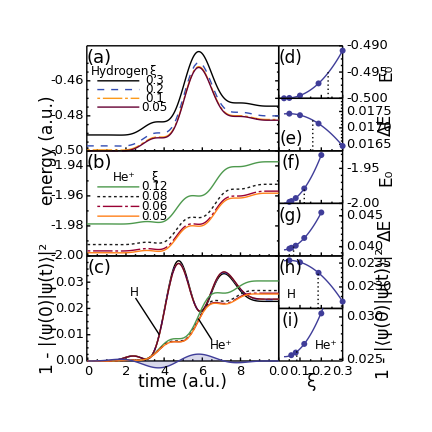

/Users/nevence/Documents/utk/first/enexConv.pdf

/Users/nevence/Documents/utk/first/enexConv.png

```mathematica
dyA=-0.005;
yA0=-0.455;
yA1=yA0+dyA;
yA2=yA0+2dyA;
yA3=yA0+3dyA;
yA4=yA0+4dyA;
x0=0.5;
x1=1.9;
x2=2.7;
x3=3.5;

dyB=-0.0065;
yB0=-1.9475;
yB1=yB0+dyB;
yB2=yB0+2dyB;
yB3=yB0+3dyB;
yB4=yB0+4dyB;
dA=1;
dB=2;


enexConvFIG=Figure[
{
Multipanel[
{{0,1},{0,1}},
{6,2},
XPanelSizes->{3,1},
XPlotRanges->{{0,10},{0,0.3}},
YPlotRanges->{0,1},
XFrameLabels->{"time (a.u.)","ξ"},
BufferB->3,
BufferL->5.5,
BufferR->6.2,
XFrameTicks->{LinTicks[0,10,1,5],LinTicks[0,0.3,0.1,2]},
YFrameTicks->Automatic,
TickNudge->{-4,{-3,0},0,{4,0}},
FontSize->17,
TickFontSize->13,
Order->Vertical
],
ManualLabel[{1.16,0.15},"1 - |⟨ψ(0)|ψ(t)⟩|^2",FontSize->17,Orientation->Vertical],
ManualLabel[{-0.15,0.67},"energy (a.u.)",FontSize->17,Orientation->Vertical],
(*H Subscript[E, 0] vs cut *)
FigurePanel[{1,2},
PlotRange->{{0,0.3},{-0.5,-0.49}},
LabR->"E_0",
FrameTicks->{LinTicks[0,0.3,0.1,2],None,None,LinTicks[-0.5,-0.49,0.005,4]},
ShowFrameLabels->{False,False,False,True},
ShowTickLabels->{False,False,False,True},
PanelLetter->"(d)"
],
RawGraphics[ListPlot[hEn0CutDAT,PlotStyle->PointSize[0.01]]],
RawGraphics[Plot[Evaluate[Fit[hEn0CutDAT,{1,x,x^2,x^3},x]],{x,0.025,0.3}]],
SchemeLine[{{0.232,-0.5},{0.232,-0.495}},Dashing->AbsoluteDashing[{dA,dB}]],
(*H ΔE vs cut *)
FigurePanel[{2,2},
PlotRange->{{0,0.3},{0.0163,0.0179}},
LabR->"ΔE",
FrameTicks->{LinTicks[0,0.3,0.1,2],None,None,LinTicks[0.0165,0.0179,0.0005,5]},
ShowFrameLabels->{False,False,False,True},
ShowTickLabels->{False,False,False,True},
PanelLetter->"(e)",
PanelLetterCorner->{-1,-1}
],
RawGraphics[ListPlot[hEnDCutDAT,PlotStyle->PointSize[0.01]]],
RawGraphics[Plot[Evaluate[Fit[hEnDCutDAT,{1,x,x^2},x]],{x,0.025,0.3}]],
SchemeLine[{{0.16,0},{0.16,0.01723}},Dashing->AbsoluteDashing[{dA,dB}]],
(*He Subscript[E, 0] vs cut *)
FigurePanel[{3,2},
PlotRange->{{0,0.3},{-2,-1.925}},
LabR->"E_0",
FrameTicks->{LinTicks[0,0.3,0.1,2],None,None,LinTicks[-2,-1.93,0.05,5]},
ShowFrameLabels->{False,False,False,True},
ShowTickLabels->{False,False,False,True},
PanelLetter->"(f)"
],
RawGraphics[ListPlot[heEn0CutDAT,PlotStyle->PointSize[0.01]]],
RawGraphics[Plot[Evaluate[Fit[heEn0CutDAT,{1,x,x^2},x]],{x,0.025,0.2}]],
SchemeLine[{{0.12,-2.00},{0.12,-1.98}},Dashing->AbsoluteDashing[{dA,dB}]],
(*He ΔE vs cut *)
FigurePanel[{4,2},
PlotRange->{{0,0.3},{0.0385,0.047}},
LabR->"ΔE",
FrameTicks->{LinTicks[0,0.3,0.1,2],None,None,LinTicks[{0.04,0.045},Range[0.039,0.048,0.001]]},
ShowFrameLabels->{False,False,False,True},
ShowTickLabels->{False,False,False,True},
PanelLetter->"(g)"
],
RawGraphics[ListPlot[heEnDCutDAT,PlotStyle->PointSize[0.01]]],
RawGraphics[Plot[Evaluate[Fit[heEnDCutDAT,{1,x,x^2},x]],{x,0.025,0.2}]],
SchemeLine[{{0.07,0},{0.07,0.04}},Dashing->AbsoluteDashing[{dA,dB}]],
(*exH vs cut*)
FigurePanel[{5,2},
YPlotRange->{0.02255,0.02365},
FrameTicks-> {LinTicks[0,0.3,0.1,2],None,None,LinTicks[0.0225,0.0236,0.0005,5]},
ShowFrameLabels->{False,False,False,True},
ShowTickLabels->{False,False,False,True},
PanelLetter->"(h)"
],
ScaledLabel[{0.2,0.27},"H"],
RawGraphics[Plot[Evaluate[Fit[exHVcutDAT,{1,x,x^2},x]],{x,0.025,0.3}]],
RawGraphics[ListPlot[exHVcutDAT,PlotStyle->PointSize[0.01]]],
SchemeLine[{{0.185,0},{0.185,0.0233}},Dashing->AbsoluteDashing[{dA,dB}]],
(*exHe vs cut*)
FigurePanel[{6,2},
YPlotRange->{0.0248,0.031},
FrameTicks-> {LinTicks[0,0.3,0.1,2],None,None,LinTicks[0.025,0.031,0.005,5]},
ShowFrameLabels->{True,False,False,True},
ShowTickLabels->{True,False,False,True},
PanelLetter->"(i)"
],
RawGraphics[Plot[Evaluate[Fit[exHeVcutDAT[[2;;]],{1,x,x^2},x]],{x,0.025,0.22}]],
RawGraphics[ListPlot[exHeVcutDAT,PlotStyle->PointSize[0.01]]],
ScaledLabel[{0.75,0.3},"He^+"],
SchemeLine[{{0.085,0},{0.085,0.026}},Dashing->AbsoluteDashing[{dA,dB}]],



(*H En vs time*)
FigurePanel[{1,1},
PanelAdjustments->{{0,0},{1,0}},
PlotRange->{{-0.05,10},{-0.5,-0.44}},
FrameTicks->{Automatic,LinTicks[-0.5,-0.45,0.02,4],None,LinTicks[-0.5,-0.45,0.01,2]},
ShowFrameLabels->{False,True,False,False},
ShowTickLabels->{False,True,False,False},
PanelLetterFontSize->18
],
RawGraphics[ListLinePlot[{enA,enB,enC,enD},PlotStyle->styleList]],
RawGraphics[Graphics[{
Sequence@@styleList[[1]],Line[{{x0,yA1},{x2,yA1}}],
Sequence@@styleList[[2]],Line[{{x0,yA2},{x2,yA2}}],
Sequence@@styleList[[3]],Line[{{x0,yA3},{x2,yA3}}],
Sequence@@styleList[[4]],Line[{{x0,yA4},{x2,yA4}}]
}]],
ManualLabel[{x1-0.2,yA0+0.0004},"Hydrogen"],
ManualLabel[{x3-0.1,yA0+0.0004},"ξ"],
ManualLabel[{x3,yA1},"0.3  "],
ManualLabel[{x3,yA2},"0.2  "],
ManualLabel[{x3,yA3},"0.1  "],
ManualLabel[{x3,yA4},"0.05"],

(*He E vs time*)
FigurePanel[{3,1},
PanelAdjustments->{{0,0},{1,0}},
PlotRange->{{-0.05,10},{-2,-1.93}},
FrameTicks->{LinTicks[0,9.5,2,4],LinTicks[-2,-1.9,0.02,2],None,LinTicks[-2,-1.9,0.02,2]},
ShowFrameLabels->{False,True,False,False},
ShowTickLabels->{False,True,False,False},
PanelLetterFontSize->18,
PanelLetter->"(b)"
],
RawGraphics[ListLinePlot[{enF,enG,enH,enI},PlotRange->All,PlotStyle->styleList[[5;;]]]],
RawGraphics[Graphics[{
Sequence@@styleList[[5]],Line[{{x0,yB1},{x2,yB1}}],
Sequence@@styleList[[6]],Line[{{x0,yB2},{x2,yB2}}],
Sequence@@styleList[[7]],Line[{{x0,yB3},{x2,yB3}}],
Sequence@@styleList[[8]],Line[{{x0,yB4},{x2,yB4}}]
}]],
ManualLabel[{x1,yB0},"He^+"],
ManualLabel[{x3,yB0},"ξ"],
ManualLabel[{x3,yB1},"0.12"],
ManualLabel[{x3,yB2},"0.08"],
ManualLabel[{x3,yB3},"0.06"],
ManualLabel[{x3,yB4},"0.05"],
(*ex vs time*)
FigurePanel[{6,1},
FrameTicks->{LinTicks[0,9.75],LinTicks[0,0.0375,0.01,4]},
PlotRange->{{-0.05,10},{0,0.04}},
LabL->"1 - |⟨ψ(0)|ψ(t)⟩|^2",
PanelAdjustments->{{0,0},{0,1}},
PanelLetterFontSize->18,
PanelLetter->"(c)"
],
RawGraphics[ListLinePlot[{totalExA,totalExB,totalExC,totalExD},PlotStyle->styleList]],
RawGraphics[ListLinePlot[{totalExE,totalExF,totalExG,totalExH},PlotStyle->styleList[[5;;]],PlotRange->All]],
RawGraphics[laserPl],
ScaledLabel[{0.25,0.65},"H"],
SchemeLine[{{2.5,0.024},{3.75,0.01}}],
ScaledLabel[{0.7,0.15},"He^+"],
SchemeLine[{{5.8,0.016},{6.5,0.008}}]
},
PlotRange->{{-0.185,1.195},{-0.1,1.02}},ImageSize->72*2*{3,3}
]
If[export,Export[exportPath<>"enexConv."<>suffix,enexConvFIG]]
Clear[x0,x1,x2,x3,dyA,yA0,yA1,yA2,yA3,yA4,dyB,yB0,yB1,yB2,yB3,yB4,dA,dB]
```

## dP/dk vs cut

#### Prereq

```mathematica
dPdk[dat_List,fNUM_,hue_]:=Module[{
dk,dθ,dϕ=π,tol=0.00001,kMAX,sum,maxH=5,
points,nk,nθ,θnext,fnext,
k,θ,f,radialCS={}},
(* The task is to integrate the cross section over the angular variables taking the left right symmetries into accout.

The points on the z-axis must be handled carefully, for it needs to represent a cone, but Sin[θ] give it zero width. See journal E pg 18 for a description of the special case Jacobian.
*)
angle[x_,z_]:=If[x≥0,
If[z≠0,If[z>0,ArcTan[x/z],ArcTan[x/z]+π],π/2],
If[z≠0,If[z<0,ArcTan[x/z]+π,ArcTan[x/z]+2π],3π/2]];
xz2rθ[{x_,z_,f___}]:={√(x^2+z^2),angle[x,z],f};
(* Steps 1 & 2
Reflecting the points which don't lie on the z axis
Turning them into polar cordinates and
Sorting them in increasing r *)
points=Sort[xz2rθ/@Join[dat,Cases[dat,{x_,z_,f___}:>{-x,z,f}/;x≠0]]];
nθ=Last[First[Tally[points,Abs[#1[[1]]- #2[[1]]]<tol&]]];
(* Steps 3 & 4
Partitioning the list and then sorting each according to r *)
points2=Sort[#,#1[[2]]<#2[[2]]&]&/@Partition[points,nθ];
nk=Length[points2];
dk = points2[[2,1,1]]-points2[[1,1,1]];
dθ = points2[[1,2,2]]-points2[[1,1,2]];
(*Print["dk = ",dk,"   dθ = ",dθ,"   dϕ = ",dϕ,"   nθ = ",nθ,"   nk = ",nk];*)
(* Step 5
Integrating θ *)
For[m=1,m≤nk,m++,
sum=0;
For[n=1,n≤nθ,n++,
k=points2[[m,n,1]];
θ=points2[[m,n,2]];
θnext=If[n≠nθ,points2[[m,n+1,2]],2π];
fnext=If[n≠nθ,points2[[m,n+1,fNUM]],points2[[m,1,fNUM]]];
If[k>kMAX,kMAX=k];
(*Print[k,"  ",N[θ],"   k dθ = ",k dθ,"    π k Abs[Sin[(θ+θnext)/2]] ",π k Abs[Sin[(θ+θnext)/2]]];*)
f=points2[[m,n,fNUM]];
(*sum+=f*dk*k dθ*dϕ k Abs[Sin[(θ+θnext)/2]];*)
sum+=(f+fnext)/2*k^2 Abs[Sin[(θ+θnext)/2]]dθ dϕ ;
If[n==nθ,AppendTo[radialCS,{k,sum}];
];
];
];
f=Interpolation[Prepend[radialCS,{0,0}]];
Off[Interpolation::inhr];
(* Step 6
Plotting k *)
(*Print["Total Cross Section = ",Total[#[[2]]*dk&/@radialCS]];*)
Plot[f[x],{x,0,radialCS[[-1,1]]},

(*Evaluate@Sequence[csOPTS[hue]],*)
PlotStyle->styleList[[hue]]
]
]

scale[dat_,p_]:=With[{x=10^p},{#[[1]],#[[2]],Sequence@@(x*#[[3;;]])}&/@dat];
(*ionA=Import[dataDIR<>"H2t5/ion10.dat"];
ionB=Import[dataDIR<>"H2t5/ion20.dat"];
ionC=Import[dataDIR<>"H2t5/ion40.dat"];
ionD=Import[dataDIR<>"H2t5/ion80.dat"];*)
ionA=Import[dataDIR<>"H3e-7/ion.dat"];
ionB=Import[dataDIR<>"H2e-7/ion.dat"];
ionC=Import[dataDIR<>"H1e-7/ion.dat"];
ionD=Import[dataDIR<>"H05e-7/ion.dat"];
Print[Length[ionA]];
Print[Length[ionB]];
Print[Length[ionC]];
Print[Length[ionD]];
tSTEPa=Length[First[ionA]];
tSTEPb=Length[First[ionB]];
tSTEPc=Length[First[ionC]];
tSTEPd=Length[First[ionD]];
kaFIG=dPdk[scale[ionA,2],tSTEPa,1];
kbFIG=dPdk[scale[ionB,2],tSTEPb,2];
kcFIG=dPdk[scale[ionC,2],tSTEPc,3];
kdFIG=dPdk[scale[ionD,2],tSTEPd,4];
ionE=Import[dataDIR<>"He12e-7/ion.dat"];
ionF=Import[dataDIR<>"He08/ion.dat"];
ionG=Import[dataDIR<>"He06e-7/ion.dat"];
ionH=Import[dataDIR<>"He05/ion.dat"];
tSTEPe=Length[First[ionE]];
tSTEPf=Length[First[ionF]];
tSTEPg=Length[First[ionG]];
tSTEPh=Length[First[ionH]];
keFIG=dPdk[scale[ionE,3],tSTEPe,1];
kfFIG=dPdk[scale[ionF,3],tSTEPf,2];
kgFIG=dPdk[scale[ionG,3],tSTEPg,3];
khFIG=dPdk[scale[ionH,3],tSTEPh,4];

F[plotDat_List,ω_]:=With[{t=#[[1]]&/@ plotDat,f=#[[2]]&/@ plotDat},
 1/(√(2π))Sum[f[[n]] ⅇ^(-I ω t[[n]])(t[[n+1]]-t[[n]]),{n,1,Length[f]-1}]
];
abFT[plotDat_List,ωMAX_,dω_]:=Table[{ω,Abs[F[plotDat,ω]]^2},{ω,0,ωMAX,dω}]
laser[nCycle_,ω_,t_]:=
If[ω t> 0 && (ω t)/(2nCycle)<π,Sin[(ω t)/(2nCycle)]^2 Sin[ω t],0];
lDATA=With[{ω=1.32,nCycles=2},Table[{t,laser[nCycles,ω,t]},{t,0,(2π)/ω*(nCycles+1),0.1}]];
psPLOT=ListLinePlot[abFT[lDATA,3,0.02],
FrameTicks->{{0.5,1,1.5,2,2.5},None,None,None},
PlotStyle->{Red,Thickness[Large]}]
```

2050

2050

2050

«1 more identical outputs»

-Graphics-

#### LevelScheme

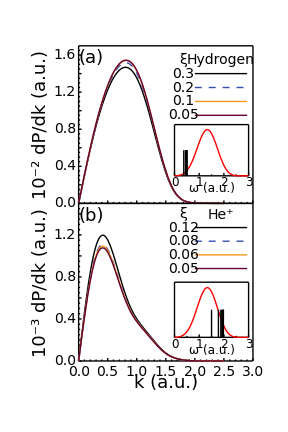

/Users/nevence/Documents/utk/first/kConv.pdf

```mathematica
dyA=-0.15;
yA0=1.55;
yA1=yA0+dyA;
yA2=yA0+2dyA;
yA3=yA0+3dyA;
yA4=yA0+4dyA;
x0=1.8;
x1=2.0;
x2=2.9;
x3=(x2+x1)/2;
dyB=-0.13;
yB0=1.4;
yB1=yB0+dyB;
yB2=yB0+2dyB;
yB3=yB0+3dyB;
yB4=yB0+4dyB;
kConvFIG=Figure[{
SetOptions[ManualLabel,FontSize->14],
Multipanel[
{{0,1},{0,1}},
{2,1},
XPlotRanges->{0,3},
YPlotRanges->{{0,1.7},{0,1.5}},
XFrameLabels->"k (a.u.)",
OrientationL->Vertical,
BufferL->5,
BufferB->3,
FontSize->18,
TickFontSize->14,
TickNudge->{-4,{-3,0},0,0}
],
FigurePanel[{1,1},
FrameTicks->{Automatic,LinTicks[0,1.69,0.2,4,TickLabelStep->2]},
LabL->"10^-2 dP/dk (a.u.)"
],
RawGraphics[kaFIG],
RawGraphics[kbFIG],
RawGraphics[kcFIG],
RawGraphics[kdFIG],
ManualLabel[{x3,yA0},"Hydrogen"],
RawGraphics[Graphics[{
Sequence@@styleList[[1]],Line[{{x1,yA1},{x2,yA1}}],
Sequence@@styleList[[2]],Line[{{x1,yA2},{x2,yA2}}],
Sequence@@styleList[[3]],Line[{{x1,yA3},{x2,yA3}}],
Sequence@@styleList[[4]],Line[{{x1,yA4},{x2,yA4}}]
}]],
ManualLabel[{x0,yA0},"ξ"],
ManualLabel[{x0,yA1},"0.3"],
ManualLabel[{x0,yA2},"0.2"],
ManualLabel[{x0,yA3},"0.1"],
ManualLabel[{x0,yA4},"0.05"],

ScaledFigurePanel[
{{0.55,0.975},{0.175,0.5}},
PlotRange->{{0,3},{0,1}},
FrameTicks->{LinTicks[0,3,1,2],None},
TickFontSize->12,
LabB->"ω (a.u.)",BufferB->2.5
],
RawGraphics[psPLOT],
With[{en=0.5},RawGraphics[Graphics[
Table[Line[{{en(1-1/n^2),0},{en(1-1/n^2),0.5}}],{n,2,10}]
]]],

FigurePanel[{2,1},
FrameTicks->{Automatic,LinTicks[0,1.5,0.2,4,TickLabelStep->2]},
LabL->"10^-3 dP/dk (a.u.)"
],
RawGraphics[keFIG],
RawGraphics[kfFIG],
RawGraphics[kgFIG],
RawGraphics[khFIG],
ManualLabel[{x3,0.99*yB0},"He^+"],
RawGraphics[Graphics[{
Sequence@@styleList[[1]],Line[{{x1,yB1},{x2,yB1}}],
Sequence@@styleList[[2]],Line[{{x1,yB2},{x2,yB2}}],
Sequence@@styleList[[3]],Line[{{x1,yB3},{x2,yB3}}],
Sequence@@styleList[[4]],Line[{{x1,yB4},{x2,yB4}}]
}]],
ManualLabel[{x0,yB0},"ξ"],
ManualLabel[{x0,yB1},"0.12"],
ManualLabel[{x0,yB2},"0.08"],
ManualLabel[{x0,yB3},"0.06"],
ManualLabel[{x0,yB4},"0.05"],
ScaledFigurePanel[
{{0.55,0.975},{0.15,0.5}},
PlotRange->{{0,3},{0,1}},
FrameTicks->{LinTicks[0,3,1,2],None},
LabB->"ω (a.u.)",BufferB->2.5

],
With[{en=2.0,ω=1.32},Sequence@@{
RawGraphics[psPLOT],
RawGraphics[Graphics[
Table[Line[{{en(1-1/n^2),0},{en(1-1/n^2),0.5}}],{n,2,10}]
]]
}]
},
PlotRange->{{-0.3,1.05},{-0.1,1.02}},ImageSize->72*{4,6}
]
If[export,Export[exportPath<>"kConv."<>suffix,kConvFIG]]
```

## Bound State vs Time ( not used )

sciForm[x,n] tested

#### Prereq

```mathematica
(*Finds the max of a 2D list after stripping off the nlm quantum numbers*)
fMAX[dat_]:=With[{fNUM=Length[First[dat]]},
maxList={};
For[i=1,i≤Length[dat],i++,
thisMax=Max[dat[[i,4;;]] ];
AppendTo[maxList,thisMax];
];
Max[maxList]
]

(*nList is a list of the indicies to be plotted*)
(*tMAX allows correct labeling of the x axis*)
plotBound[boundData_,tMAX_,nList_List,opts___]:=
Module[{steps=Length[boundData[[1,4;;]] ],dt,dat},
dt=tMAX/steps;
dat=Table[{(i-3) dt,boundData[[n,i]] },{n,nList},{i,4,Length@boundData[[1]]}];
ListLinePlot[dat,opts,PlotRange->All]
]

boundH=Import[dataDIR<>"H05e-7/ex.dat"];
boundHe=Import[dataDIR<>"He06e-7/ex.dat"];
Print["Length[boundH] = ",Length[boundH]]
Print["Length[boundH[[1]]] = ",Length[boundH[[1]]]]
Print["Length[boundHe] = ", Length[boundHe]]
Print["Length[boundHe[[1]]] = ",Length[boundHe[[1]]]]

laser[nCycle_,ω_,t_]:=
If[ω t> 0 && (ω t)/(2nCycle)<π,Sin[(ω t)/(2nCycle)]^2 Sin[ω t],0];


sciForm[x_,n_]:=ScientificForm[x,{n,n-1},NumberPadding->{"","0"}]
TableForm@Table[{n,sciForm[0.04,n],sciForm[0.049,n],sciForm[0.0499,n],sciForm[0.04999,n]},{n,1,5}]
```

#### He^+ (Broken)

```mathematica
laserY=0;
laserAmp=0.00002;
laserPl=Plot[laserAmp*laser[2,1.32,t]+laserY,{t,0,10},
Filling->Axis,
AxesOrigin->{0,laserY}];

laserAmp=0.0014;
laserPl2=Plot[laserAmp*laser[2,1.32,t]+laserY,{t,0,10},
Filling->Axis,
AxesOrigin->{0,laserY}];

ns=Table[n,{n,1,5}];
np=Table[n,{n,14,18}];
nd=Table[n,{n,25,28}];
nf=Table[n,{n,35,38}];
ng=Table[n,{n,44,47}];
nh=Table[n,{n,52,55}];

hePnlFIG=Figure[
{
ScaledLabel[{0.5,0.98},"Bound State probabilities of He^+ vs time",FontSize->15],
Multipanel[{{0,1},{0,1}},
{1,6},
XPlotRanges->{0,10}
],
(*Ps vs t*)
FigurePanel[{1,1},
FrameTicks->None,
YPlotRange->{0,3.5*^-4}
],
RawGraphics[plotBound[boundHe,11.8,ns,PlotStyle->Blue]],
ScaledLabel[{0.5,0.95},Subscript[P,n00]],
ManualLabel[{9.2,0.94*boundHe[[2,-1]]},Subscript[P,200]],
ManualLabel[{9.2,1.5*boundHe[[3,-1]]},Subscript[P,300]],
RawGraphics[laserPl],
(*Pp v t*)
FigurePanel[{1,2},
FrameTicks->None,
YPlotRange->{0,2.5*^-2}
],
ScaledLabel[{0.21,0.29},sciForm[boundHe[[2,-1]],2]],
ScaledLabel[{0.21,0.06},sciForm[boundHe[[3,-1]],2]],
RawGraphics[plotBound[boundHe,11.8,np,PlotStyle->Green]],
ScaledLabel[{0.5,0.95},Subscript[P,n10]],
ManualLabel[{9.1,1.02*boundHe[[14,-1]]},Subscript[P,210]],
ManualLabel[{9.1,1.3*boundHe[[15,-1]]},Subscript[P,310]],
RawGraphics[laserPl2],
(*Pd vs t*)
FigurePanel[{1,3},
FrameTicks->None,
YPlotRange->{0,1.8*^-4}
],
ScaledLabel[{0.23,0.86},sciForm[boundHe[[14,-1]],2]],
ScaledLabel[{0.23,0.08},sciForm[boundHe[[15,-1]],2]],

RawGraphics[plotBound[boundHe,11.8,nd,PlotStyle->Gray,PlotRange->All]],
ScaledLabel[{0.5,0.95},Subscript[P,n20]],
ManualLabel[{9.1,0.95*boundHe[[25,-1]]},Subscript[P,320]],
ManualLabel[{9.1,0.92*boundHe[[26,-1]]},Subscript[P,420]],
(*Pf vs t*)
FigurePanel[{1,4},
FrameTicks->None,
YPlotRange->{0,5*^-7}
],
ScaledLabel[{0.23,0.38},sciForm[boundHe[[25,-1]],2]],
ScaledLabel[{0.23,0.2},sciForm[boundHe[[26,-1]],2]],
ScaledLabel[{0.23,0.11},sciForm[boundHe[[27,-1]],2]],
ScaledLabel[{0.23,0.06},sciForm[boundHe[[28,-1]],2]],
RawGraphics[plotBound[boundHe,11.8,nf,PlotStyle->Orange]],
ScaledLabel[{0.5,0.95},Subscript[P,n30]],
(*Pg vs t*)
FigurePanel[{1,5},
FrameTicks->None,
YPlotRange->{0,2.5*^-9}
],
ScaledLabel[{0.23,0.1},sciForm[boundHe[[36,-1]],2]],
ScaledLabel[{0.23,0.045},sciForm[boundHe[[38,-1]],2]],
RawGraphics[plotBound[boundHe,11.8,ng,PlotStyle->Brown]],
ScaledLabel[{0.5,0.95},Subscript[P,n40]],
(*Ph vs t*)
FigurePanel[{1,6},
FrameTicks->None,
YPlotRange->{0,8*^-10}
],
RawGraphics[plotBound[boundHe,11.8,nh,PlotStyle->Black]],
ScaledLabel[{0.25,0.075},sciForm[boundHe[[45,-1]],2]],
ScaledLabel[{0.5,0.95},Subscript[P,n50]]
},
PlotRange->{{-0.07,1.07},{-0.08,1.05}},ImageSize->72*2*{6,2.4}
]
If[export,Export[exportPath<>"hePnl."<>suffix,hePnlFIG]]
```

## Bound State vs Cut ( fancy Ticks )

Generating this figure is a multi-step process. Projecting on the eigenstates with projPsi must be done with the same bound.num file so that finalProb will correctly collect the last wave

### Listed P(T)

```mathematica
(*EACH boundX MUST HAVE THE SAME PATTERN OF STATES*)
(* 
i different cuts = Length[listOlist];
j states in each cut (must be the same for all boundN;
t the time step (the first three are the bound quantum numbers*)
finalProb[listOlist_]:=With[{
Ncut=Length[listOlist],(*i index*)
Nstates=Length[listOlist[[2]]],(*j index*)
Nsteps=Length[#[[1]]]&/@listOlist},(*k index*)
Print["Ncut: ",Ncut];
Print["Nstates: ",Nstates];
Print["Nsteps: ",Nsteps];
If[Length@listOlist[[1]]!=Length@listOlist[[2]],Print["Lists 1 and 2 have different Length"]];
If[Length@listOlist[[2]]!=Length@listOlist[[3]],Print["Lists 2 and 3 have different Length"]];
If[Length@listOlist[[3]]!=Length@listOlist[[4]],Print["Lists 3 and 4 have different Length"]];
Table[(* cycle through the different states*)
Join[
listOlist[[1,j,;;3]],(*n l m*) 
Table[listOlist[[i,j,Nsteps[[i]]]],
{i,Ncut}] (*final probability for each boundX*)
],
{j,1,Nstates}]
]
sciForm[x_,n_]:=ScientificForm[x,{n,n-1},NumberPadding->{"","0"}]
```

#### H (broken)

```mathematica
boundA=Import[dataDIR<>"H3e-7/ex.dat"];
boundB=Import[dataDIR<>"H2e-7/ex.dat"];
boundC=Import[dataDIR<>"H1e-7/ex.dat"];
boundD=Import[dataDIR<>"H05e-7/ex.dat"];
dat1={boundA,boundB,boundC,boundD};
Length[#]&/@dat1;
hDAT=finalProb[dat1]
```

Ncut: 4

Nstates: 45

Nsteps: {4,4,33,160}

{{1,0,0,4.16655×10^-9,5.36565×10^-10,1.33332×10^-11,2.80333×10^-13},{2,0,0,0.0000200655,0.0000207074,0.0000208447,0.0000208665},{3,0,0,5.42857×10^-6,5.66764×10^-6,5.8728×10^-6,5.784×10^-6},{4,0,0,2.22582×10^-6,2.32407×10^-6,2.39977×10^-6,2.36201×10^-6},{5,0,0,1.12488×10^-6,1.17442×10^-6,1.21109×10^-6,1.19169×10^-6},{6,0,0,6.46399×10^-7,6.74824×10^-7,6.95446×10^-7,6.84284×10^-7},{7,0,0,4.05338×10^-7,4.23147×10^-7,4.35913×10^-7,4.28936×10^-7},{8,0,0,2.70798×10^-7,2.82689×10^-7,2.91149×10^-7,2.86504×10^-7},{9,0,0,1.89831×10^-7,1.98164×10^-7,2.04061×10^-7,2.00816×10^-7},{2,1,0,0.00499821,0.00501802,0.00502835,0.00502889},{3,1,0,0.00124138,0.00125648,0.0012648,0.00126516},{4,1,0,0.000496917,0.000504141,0.000507933,0.00050823},{5,1,0,0.000248629,0.000252499,0.000254506,0.000254658},{6,1,0,0.000142137,0.000144426,0.000145607,0.000145695},{7,1,0,0.0000888619,0.0000903213,0.0000910717,0.0000911271},{8,1,0,0.000059253,0.0000602383,0.0000607439,0.0000607812},{9,1,0,0.0000414829,0.0000421785,0.0000425349,0.0000425613},{3,2,0,1.16281×10^-6,1.1656×10^-6,1.15637×10^-6,1.16637×10^-6},{4,2,0,6.21799×10^-7,6.24853×10^-7,6.23819×10^-7,6.25128×10^-7},{5,2,0,3.46906×10^-7,3.48965×10^-7,3.48598×10^-7,3.49637×10^-7},{6,2,0,2.09382×10^-7,2.10735×10^-7,2.10619×10^-7,2.11304×10^-7},{7,2,0,1.35061×10^-7,1.35975×10^-7,1.35954×10^-7,1.36401×10^-7},{8,2,0,9.18566×10^-8,9.24957×10^-8,9.2508×10^-8,9.28093×10^-8},{9,2,0,6.51705×10^-8,6.56326×10^-8,6.56555×10^-8,6.58663×10^-8},{4,3,0,7.15143×10^-11,7.78148×10^-11,1.70564×10^-10,2.41049×10^-11},{5,3,0,5.91575×10^-11,6.35366×10^-11,9.25971×10^-11,3.58369×10^-11},{6,3,0,4.20548×10^-11,4.48255×10^-11,5.62807×10^-11,2.96783×10^-11},{7,3,0,2.95985×10^-11,3.1417×10^-11,3.67046×10^-11,2.23012×10^-11},{8,3,0,2.12211×10^-11,2.24686×10^-11,2.51984×10^-11,1.65747×10^-11},{9,3,0,1.55861×10^-11,1.6476×10^-11,1.80088×10^-11,1.24511×10^-11},{5,4,0,9.36666×10^-16,3.64044×10^-14,1.08616×10^-12,3.36279×10^-13},{6,4,0,1.02039×10^-15,2.04307×10^-14,8.54018×10^-13,2.58955×10^-13},{7,4,0,8.90741×10^-16,1.168×10^-14,6.15748×10^-13,1.78536×10^-13},{8,4,0,6.95714×10^-16,7.22352×10^-15,4.45313×10^-13,1.24087×10^-13},{9,4,0,6.13×10^-16,4.78276×10^-15,3.28246×10^-13,8.86227×10^-14},{6,5,0,2.66914×10^-17,1.00816×10^-15,4.37042×10^-13,6.57172×10^-13},{7,5,0,1.54902×10^-17,8.71376×10^-16,4.3951×10^-13,5.67478×10^-13},{8,5,0,1.20105×10^-17,6.51816×10^-16,3.58494×10^-13,4.11131×10^-13},{9,5,0,6.79722×10^-18,4.81693×10^-16,2.7968×10^-13,2.92625×10^-13},{7,6,0,3.11555×10^-18,6.86753×10^-17,1.00963×10^-15,1.92315×10^-15},{8,6,0,3.84793×10^-18,8.42479×10^-17,1.32649×10^-15,2.69237×10^-15},{9,6,0,2.60459×10^-18,7.71302×10^-17,1.29509×10^-15,2.73396×10^-15},{8,7,0,4.8131×10^-19,1.16695×10^-18,4.68269×10^-16,9.62626×10^-16},{9,7,0,3.45552×10^-19,1.85982×10^-18,7.91464×10^-16,1.65032×10^-15},{9,8,0,3.53199×10^-19,1.23505×10^-19,3.97511×10^-19,7.53639×10^-19}}

Lists 1 and 2 have different Length

Nsteps: {2,4,33,160}

Nstates: 45

Ncut: 4

Lists 2 and 3 have different Length

Lists 1 and 2 have different Length

Nsteps: {2,4,2,2}

Nstates: 210

Ncut: 4

Ncut: 4

Nstates: 22

Nsteps: {16,13,15,98}

Lists 3 and 4 have different Length

{{2,0,0,0.000164784,0.0000182697,0.0000180278,0.0000205628},{3,0,0,0.0000394937,2.56894×10^-6,5.08972×10^-6,6.16746×10^-6},{4,0,0,0.0000137084,8.29567×10^-7,2.06758×10^-6,2.53691×10^-6},{5,0,0,6.24929×10^-6,3.77168×10^-7,1.03985×10^-6,1.27746×10^-6},{6,0,0,3.37005×10^-6,2.05141×10^-7,5.96002×10^-7,7.31859×10^-7},{7,0,0,2.0283×10^-6,1.24578×10^-7,3.73172×10^-7,4.57953×10^-7},{8,0,0,1.31794×10^-6,8.15537×10^-8,2.49071×10^-7,3.05494×10^-7},{9,0,0,9.05973×10^-7,5.63926×10^-8,1.74488×10^-7,2.13927×10^-7},{2,1,0,0.00500147,0.00501805,0.00502502,1.5562×10^-7},{3,1,0,0.00124173,0.00125641,0.00126445,0.00499757},{4,1,0,0.000496959,0.000504175,0.000507661,0.00131796},{5,1,0,0.000248626,0.00025252,0.000254291,0.000525503},{6,1,0,0.000142128,0.000144439,0.00014546,0.000261946},{7,1,0,0.0000888528,0.0000903293,0.000090971,0.000149395},{8,1,0,0.0000592455,0.0000602436,0.0000606733,0.0000932572},{9,1,0,0.000041477,0.0000421822,0.0000424839,0.0000621206},{3,2,0,1.16363×10^-6,1.16927×10^-6,1.20887×10^-6,0.0000434596},{4,2,0,6.22235×10^-7,6.26491×10^-7,6.38172×10^-7,0.000031594},{5,2,0,3.4681×10^-7,3.49788×10^-7,3.54672×10^-7,1.11997×10^-6},{4,3,0,4.38174×10^-11,9.32893×10^-11,3.66756×10^-11,5.48938×10^-7},{5,3,0,4.35426×10^-11,6.87952×10^-11,1.8902×10^-11,3.09764×10^-7},{5,4,0,2.22673×10^-13,5.7252×10^-15,5.48225×10^-12,1.8952×10^-7}}

#### He^+

```mathematica
Clear[boundA,boundB,boundC,boundD];
boundA=Import[dataDIR<>"He12e-7/ex2.dat"];
boundB=Import[dataDIR<>"He08/ex2.dat"];
boundC=Import[dataDIR<>"He06e-7/ex2.dat"];
boundD=Import[dataDIR<>"He05/ex3.dat"];
dat2={boundA,boundB,boundC,boundD};
Length[#]&/@dat2;
heDAT=finalProb[dat2]
```

Ncut: 4

Nstates: 44

Nsteps: {107,50,88,4}

{{2,0,0,0.000101745,0.000100441,0.0000996292,0.000100053},{3,0,0,0.0000182003,0.0000174951,0.0000173041,0.0000173007},{4,0,0,6.34797×10^-6,6.07869×10^-6,5.96777×10^-6,5.95045×10^-6},{5,0,0,2.9739×10^-6,2.83273×10^-6,2.7935×10^-6,2.80873×10^-6},{6,0,0,1.63886×10^-6,1.56315×10^-6,1.53786×10^-6,1.54245×10^-6},{7,0,0,1.00193×10^-6,9.56742×10^-7,9.39933×10^-7,9.40386×10^-7},{8,0,0,6.58418×10^-7,6.29137×10^-7,6.17651×10^-7,6.16891×10^-7},{9,0,0,4.56362×10^-7,4.36227×10^-7,4.28112×10^-7,4.27098×10^-7},{2,1,0,0.0224427,0.0216586,0.0214094,0.0213547},{3,1,0,0.00210189,0.00199502,0.00196247,0.00194454},{4,1,0,0.000532423,0.000500687,0.00049212,0.000486581},{5,1,0,0.00021052,0.000197077,0.000193833,0.000191319},{6,1,0,0.00010521,0.0000982133,0.0000965702,0.0000952176},{7,1,0,0.0000605095,0.0000563802,0.000055428,0.0000546165},{8,1,0,0.000038183,0.0000355316,0.0000349294,0.0000344038},{9,1,0,0.0000257284,0.0000239198,0.0000235141,0.000023154},{3,2,0,0.000067951,0.0000674057,0.0000670195,0.0000671913},{4,2,0,0.000033979,0.0000336137,0.0000334508,0.0000334983},{5,2,0,0.0000181882,0.0000180027,0.0000178444,0.0000178685},{6,2,0,0.0000107069,0.0000105856,0.0000105083,0.0000105323},{7,2,0,6.79742×10^-6,6.71566×10^-6,6.67191×10^-6,6.69061×10^-6},{8,2,0,4.57378×10^-6,4.51705×10^-6,4.48911×10^-6,4.50281×10^-6},{9,2,0,3.22074×10^-6,3.18012×10^-6,3.16086×10^-6,3.17087×10^-6},{4,3,0,2.22011×10^-8,2.54622×10^-8,1.98407×10^-8,2.10381×10^-8},{5,3,0,1.76816×10^-8,1.85425×10^-8,1.56809×10^-8,1.71816×10^-8},{6,3,0,1.22559×10^-8,1.3768×10^-8,1.10392×10^-8,1.25002×10^-8},{7,3,0,8.53384×10^-9,9.81602×10^-9,7.69992×10^-9,8.74616×10^-9},{8,3,0,6.08226×10^-9,7.05226×10^-9,5.48384×10^-9,6.20568×10^-9},{9,3,0,4.44992×10^-9,5.17372×10^-9,4.00847×10^-9,4.51545×10^-9},{5,4,0,5.77211×10^-12,3.2568×10^-11,1.37786×10^-11,7.719×10^-12},{6,4,0,4.63835×10^-12,1.11405×10^-11,7.52674×10^-12,1.17161×10^-12},{7,4,0,4.15583×10^-12,9.11593×10^-12,7.33224×10^-12,8.40831×10^-13},{8,4,0,3.30945×10^-12,7.80644×10^-12,6.74491×10^-12,7.16724×10^-13},{9,4,0,2.55263×10^-12,6.51796×10^-12,5.81458×10^-12,8.20303×10^-13},{6,5,0,4.93884×10^-13,1.76744×10^-11,1.61693×10^-11,5.62816×10^-11},{7,5,0,5.15814×10^-14,3.93723×10^-12,4.49298×10^-12,1.89086×10^-11},{8,5,0,1.81678×10^-14,8.92892×10^-13,1.71313×10^-12,7.10081×10^-12},{9,5,0,9.8733×10^-15,4.98279×10^-13,9.84392×10^-13,3.30764×10^-12},{7,6,0,3.74377×10^-14,1.8448×10^-12,2.32087×10^-12,7.48629×10^-12},{8,6,0,4.65394×10^-14,1.033×10^-12,1.56638×10^-12,5.40849×10^-12},{9,6,0,5.51457×10^-14,4.9406×10^-13,9.04924×10^-13,3.33007×10^-12},{8,7,0,1.8871×10^-14,4.84785×10^-13,2.93302×10^-13,4.5447×10^-13},{9,7,0,1.59587×10^-14,6.24576×10^-13,3.65451×10^-13,5.6805×10^-13},{9,8,0,1.00915×10^-14,7.85558×10^-15,5.24392×10^-15,1.17298×10^-15}}

### P(T) vs cut

#### Scientific Notation

```mathematica
(*
prob = {n,ℓ,m,P1,P2,...,Pn};
cut  = {c1,c2,...,cn};
pos  = {rowN,colN};
showTickLableList is an option for FigurePanel;
startAt is the starting of the data to plot
*)
plotVScB[prob_,cut_,pos_,showTickLabelList_,startAt_,opts___]:=Module[{(*Strip off nlm labels,and tack on cut as a label across the list's other dimension*)dat=Transpose[{cut,prob[[4;;]]}][[startAt;;]],
(*Store labels*)
nl=ToString[prob[[1]]]<>ToString[prob[[2]]],
max1=Max[prob[[3+startAt;;]]],
min1=Min[prob[[3+startAt;;]]],
yTicks={},nlStr,
dy1,dy2,dy3,dy4,dy,y,
min,min2,min3,min4,
max,max2,max3,max4,
exact,powerOfTen},

exact=dat[[-1,2]]; (*the y-value of the smallest cut*)
(**Here is how I'm doing Scientific notation**)
(*I want approximately 6 dy divisions across my yaxis*)
dy1=(max1-min1)/6;
(*compressing dy1 between 1 and 9.99...*)
dy2=dy1/Power[10,Floor[Log[10,dy1]]];
(*compressing min and max to dy1's scale*)
min2=min1/Power[10,Floor[Log[10,dy1]]];
max2=max1/Power[10,Floor[Log[10,dy1]]];
(*finding the closest integer 1, 2, 5, 10 for the ticks*)
dy3=Which[dy2>7.5,10,dy2>3,5,dy2>1.5,2,dy2≥1,1];
(*rounding to the nearest tick*)
min3=Floor[min2/dy3]*dy3;
max3=Ceiling[max2/dy3]*dy3;
(*dy = dy3 * the original exponent*)
dy=dy3*Power[10,Floor[Log[10,dy1]]];
min=min3*Power[10,Floor[Log[10,dy1]]];
max=max3*Power[10,Floor[Log[10,dy1]]];
(*Print["dy = ",1.*dy];
Print["min = ",1.*min];
Print["max = ",1.*max];*)
(*MORE LOGIC NEEDED;
I'm limited to three dy ticks;
Logic needed to discern the length of the yTicks list;*)


(*Generate yTicks*)
yTicks=Table[{min+y,sciForm[N[min+y],3],{0.01,0},{}},{y,dy,5dy,2dy}];

(*Generate LevelScheme*)
Sequence@@{
FigurePanel[pos,
PlotRange->{{0,Max[cut]},{min-dy/2,max+dy/2}},FrameTicks->{LinTicks[0,0.29,0.05,5],yTicks,None,yTicks},
ShowTickLabels->showTickLabelList,
opts
],
RawGraphics[ListLinePlot[dat]],
RawGraphics[ListPlot[dat,PlotStyle->PointSize[0.012]]],
SchemeLine[{{0,exact},{cut[[1]],exact}},LineColor->Gray,Dashing->Automatic],
ScaledLabel[{0.35,0.85},Subscript[P,nl]],
ScaledLabel[{0.45,0.85}," = "],
ScaledLabel[{0.7,0.85},sciForm[exact,4]]
(*,SchemeLine[{{cut[[-1]],exact},{0.35 cut[[1]],0.9(max-min)+min}},Color->LightGray]*)
}
]

Figure[{
Multipanel[
{{0,1},{0,1}},
{2,1}
],
plotVScB[heDAT[[1]],{0.3,0.2,0.1,0.05},{1,1},{False,True,False,False},2],
plotVScB[heDAT[[9]],{0.3,0.2,0.1,0.05},{2,1},{False,True,False,False},1,LabL->"Probability",BufferL->11]
},
PlotRange->{{-0.2,1.15},{-0.08,1.05}},ImageSize->72*2*{4,2}
]
```

#### Percent

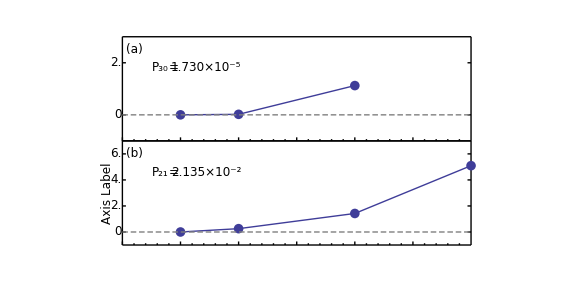

```mathematica
(*
prob = {n,ℓ,m,P1,P2,...,Pn};
cut  = {c1,c2,...,cn};
pos  = {rowN,colN};
showTickLableList is an option for FigurePanel;
startAt is the starting of the data to plot
*)
plotVScB[prob_,cut_,pos_,showTickLabelList_,startAt_,tweak_,opts___]:=Module[{(*Strip off nlm labels,and tack on cut as a label across the list's other dimension*)dat=Transpose[{cut,prob[[4;;]]}][[startAt;;]],
(*Store labels*)
nl=ToString[prob[[1]]]<>ToString[prob[[2]]],
max1=Max[prob[[3+startAt;;]]],
min1=Min[prob[[3+startAt;;]]],
yTicks={},nlStr,
dy1,dy2,dy3,dy4,dy,y,
min,min2,min3,min4,
max,max2,max3,max4,
exact,powerOfTen},
exact=dat[[-1,2]]; (*the y-value of the smallest cut*)
(**Change to percent**)
(*I want one tick mark to be approximately 1/2 dy of the range (~2 tick marks)*)
(*dy Represents 1 tick mark*)
dy1=(max1-min1)/tweak;
(*dy as a % of exact*)
dy2=dy1/exact;
(*Scaled*)
min2=(exact-min1)/exact;(*% over*)
max2=(max1-exact)/exact;(*% under*)
(*powerOfTen: the exponent part in scientific notation*)
powerOfTen=Power[10,Floor[Log[10,dy2]]];
(**compressing numbers -> [1,10)**)
(*dy3: the decimal part of scientific notation*)
dy3=dy2/powerOfTen;
min3=min2/powerOfTen;
max3=max2/powerOfTen;
(*finding the closest integer {1,2,5,10} for the ticks*)
dy4=Which[dy3>7.5,10,dy3>3,5,dy3>1.5,2,dy3≥1,1];
min4=Ceiling[min3/dy4]*dy4;(*min is positive*)
max4=Ceiling[max3/dy4]*dy4;
(**expanding numbers back to original coordinates*)
dy=(dy4*powerOfTen)*exact;
(*Scaling is based on Exact*)
(*Max and Min are shifted as a percentage over/under Exact*)
min=exact*(1-min4*powerOfTen);
max=exact*(1+max4*powerOfTen);
(*Print["exact = ",exact,"  powerOfTen = ",powerOfTen];
Print["dy1:  ",dy1/exact,"    dy1 = ",dy1,"   dy2 = ",dy2,"   dy3 = ",dy3,"   dy4 = ",dy4,"   dy = ",N@dy,"   dy: ",N@dy/exact];
Print["min1 = ",min1,"   min2 = ",min2,"   min3 = ",min3,"   min4 = ",min4,"   min = ",min];
Print["max1 = ",max1,"   max2 = ",max2,"   max3 = ",max3,"   max4 = ",max4,"   max = ",max];
*)
(*Generate yTicks *)
y=min;
While[y≤max,
If[ Abs[(y-exact)/exact]>0.00001,
AppendTo[yTicks,{y,ToString[NumberForm[100 (y-exact)/exact,4]],{0.01,0},{}}],
AppendTo[yTicks,{y,"0",{0.01,0},{}}]];
y+=dy;];
(*Generate LevelScheme*)
Sequence@@{
FigurePanel[pos,
PlotRange->{{0,Max[cut]},{min-dy/2,max+dy/2}},FrameTicks->{LinTicks[0,0.29,0.05,5],yTicks,None,yTicks},
ShowTickLabels->showTickLabelList,
opts
],
RawGraphics[ListLinePlot[dat]],
RawGraphics[ListPlot[dat,PlotStyle->PointSize[0.012]]],
SchemeLine[{{0,exact},{cut[[1]],exact}},LineColor->Gray,Dashing->Automatic],
(*One Column MultiPanel*)
ScaledLabel[{0.11,0.7},Subscript[P,nl]],
ScaledLabel[{0.147,0.7}," = "],
ScaledLabel[{0.24,0.7},sciForm[exact,4]]
(*Two Column MultiPanel*)
(*ScaledLabel[{0.35,0.85},Subscript[P,nl]],
ScaledLabel[{0.45,0.85}," = "],
ScaledLabel[{0.7,0.85},sciForm[exact,4]]*)
(*,SchemeLine[{{cut[[-1]],exact},{0.35 cut[[1]],0.9(max-min)+min}},Color->LightGray]*)
}
]

Figure[{
Multipanel[
{{0,1},{0,1}},
{2,1}
],
plotVScB[heDAT[[2]],{0.3,0.2,0.1,0.05},{1,1},{False,True,False,False},2,0.5],
plotVScB[heDAT[[9]],{0.3,0.2,0.1,0.05},{2,1},{False,True,False,False},1,1.7,LabL->"Axis Label",BufferL->3]
},
PlotRange->{{-0.2,1.15},{-0.08,1.05}},ImageSize->72*2*{4,2}
]
```

#### H

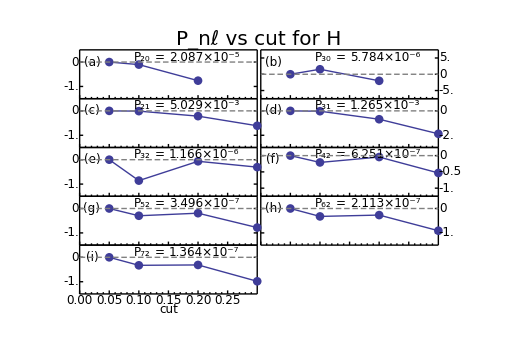

/Users/nevence/Documents/utk/first/nlConv.pdf

/Users/nevence/Documents/utk/first/nlConv.pdf

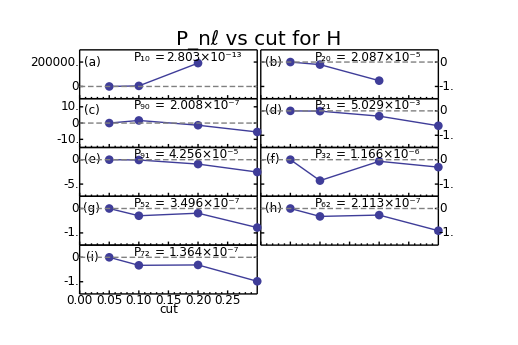

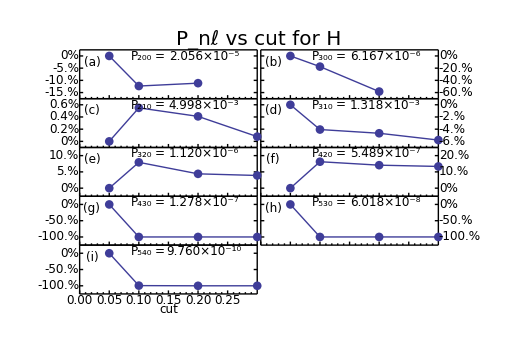

/Users/nevence/Documents/utk/10C/vence1/nlConv.pdf

```mathematica
hCut={0.3,0.2,0.1,0.05};
tweak=0.8;
Figure[{
ScaledLabel[{0.5,0.97},"P_nℓ vs cut for H",FontSize->20],
Multipanel[
{{0,1},{0,1}},
{5,2},
XFrameLabels->textit["cut"],
BufferB->3,
XGapSizes->0.02,
ShowTickLabelsExterior->{True,True,False,True}
],
plotVScB[hDAT[[2]],hCut,{1,1},{False,True,False,False},2,tweak],
plotVScB[hDAT[[3]],hCut,{1,2},{False,False,False,True},2,tweak],
plotVScB[hDAT[[10]],hCut,{2,1},{False,True,False,False},1,tweak],
plotVScB[hDAT[[11]],hCut,{2,2},{False,False,False,True},1,tweak],
plotVScB[hDAT[[18]],hCut,{3,1},{False,True,False,False},1,tweak],
plotVScB[hDAT[[19]],hCut,{3,2},{False,False,False,True},1,tweak],
plotVScB[hDAT[[20]],hCut,{4,1},{False,True,False,False},1,tweak],
plotVScB[hDAT[[21]],hCut,{4,2},{False,False,False,True},1,tweak],
plotVScB[hDAT[[22]],hCut,{5,1},{True,True,False,False},1,tweak]
},
PlotRange->{{-0.09,1.09},{-0.08,1.075}},ImageSize->72*2*{3.6,2.4}
]
If[export,Export[exportPath<>"nlConv."<>suffix,nlConvFIG]]
```

#### He^+ 1

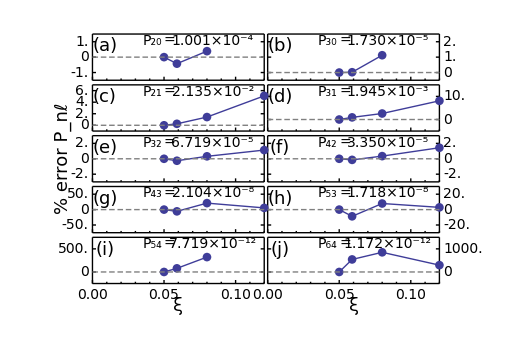

```mathematica
heCut={0.12,0.08,0.059,0.05};
tweak=0.8;
Figure[{
(*ScaledLabel[{0.5,0.97},"P_nℓ vs cut for He^+",FontSize->20],*)
SetOptions[ScaledLabel,FontSize->14],
Multipanel[
{{0,1},{0,1}},
{5,2},
XFrameLabels->"ξ",
BufferB->3,
XGapSizes->0.02,
YGapSizes->0.1,
ShowTickLabelsExterior->{True,True,False,True},
TickNudge->{-5,{-4,0},0,{4,0}},
TickFontSize->14,
FontSize->18
],
plotVScB[heDAT[[1]],heCut,{1,1},{False,True,False,False},2,tweak],
plotVScB[heDAT[[2]],heCut,{1,2},{False,False,False,True},2,tweak],
plotVScB[heDAT[[9]],heCut,{2,1},{False,True,False,False},1,2.7tweak],
plotVScB[heDAT[[10]],heCut,{2,2},{False,False,False,True},1,tweak],
(*plotVScB[heDAT[[17]],heCut,{3,1},{False,True,False,False},1,LabL->"% error (P^cut)_nl compared with (P^0.05)_nl",BufferL->5],*)
plotVScB[heDAT[[17]],heCut,{3,1},{False,True,False,False},1,tweak,LabL->"% error P_nℓ",BufferL->4],

plotVScB[heDAT[[18]],heCut,{3,2},{False,False,False,True},1,tweak,LabR->"% error P_nℓ",BufferR->1],
plotVScB[heDAT[[24]],heCut,{4,1},{False,True,False,False},1,tweak],
plotVScB[heDAT[[25]],heCut,{4,2},{False,False,False,True},1,tweak],
plotVScB[heDAT[[30]],heCut,{5,1},{True,True,False,False},2,tweak],
plotVScB[heDAT[[31]],heCut,{5,2},{True,False,False,True},1,tweak]
},
PlotRange->{{-0.13,1.09},{-0.12,1.01}},ImageSize->72*2*{3.6,2.4}
]
```

#### He^+ 2

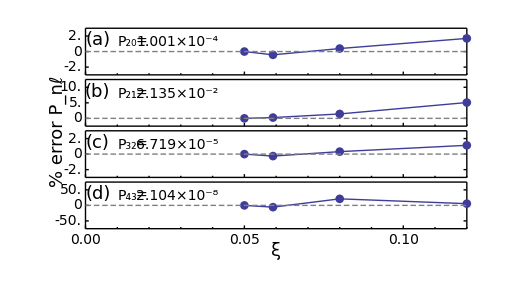

/Users/nevence/Documents/utk/first/nlConv.pdf

```mathematica
heCut={0.12,0.08,0.059,0.05};
tweak=0.8;
nlConvFIG=Figure[{
ScaledLabel[{0.025,0.55},"% error P_nℓ",Orientation->Vertical,FontSize->18],
SetOptions[ScaledLabel,FontSize->14],
Multipanel[
{{0,1},{0,1}},
{4,1},
XFrameLabels->"ξ",
BufferB->3,
XGapSizes->0.02,
YGapSizes->0.1,
ShowTickLabelsExterior->{True,True,False,True},
TickNudge->{-5,{-4,0},0,{4,0}},
TickFontSize->14,
FontSize->18
],
plotVScB[heDAT[[1]],heCut,{1,1},{False,True,False,False},1,tweak],
plotVScB[heDAT[[9]],heCut,{2,1},{False,True,False,False},1,tweak],
plotVScB[heDAT[[17]],heCut,{3,1},{False,True,False,False},1,tweak(*,LabL->"% error P_nℓ",BufferL->4*)],
plotVScB[heDAT[[24]],heCut,{4,1},{True,True,False,False},1,tweak]
},
PlotRange->{{-0.1,1.01},{-0.16,1.01}},ImageSize->72*2*{3.6,2}
]
If[export,Export[exportPath<>"nlConv."<>suffix,nlConvFIG]]
```

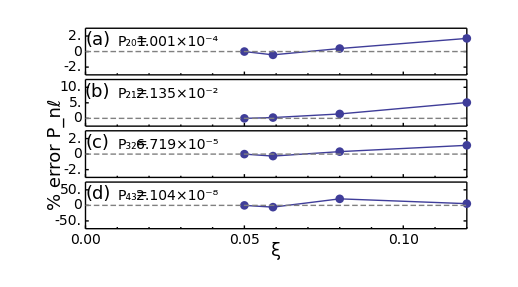

### Bound State vs time vs cut

```mathematica
(*Finds the max of a 2D list after stripping off the nlm quantum numbers*)
fMAX[dat_]:=With[{fNUM=Length[First[dat]]},
maxList={};
For[i=1,i≤Length[dat],i++,
thisMax=Max[dat[[i,4;;]] ];
AppendTo[maxList,thisMax];
];
Max[maxList]
]


plotBound[boundData_,tMAX_,nList_List,opts___]:=Module[{steps=Length[boundData[[1,4;;]] ],dt,dat},
dt=tMAX/steps;
dat=Table[{(i-3) dt,Log[10,boundData[[n,i]] ]},{n,nList},{i,4,Length@boundData[[1]]}];
ListLinePlot[dat,opts]
]

boundA=Import[dataDIR<>"H3/ex.dat"];
boundB=Import[dataDIR<>"H2/ex.dat"];
boundC=Import[dataDIR<>"H1/ex.dat"];
boundD=Import[dataDIR<>"H05/ex.dat"];
boundE=Import[dataDIR<>"He2/ex.dat"];
boundF=Import[dataDIR<>"He12e-7/ex2.dat"];
boundG=Import[dataDIR<>"He08/ex2.dat"];
boundH=Import[dataDIR<>"He06e-7/ex2.dat"];
boundI=Import[dataDIR<>"He05/ex3.dat"];

finalP[listOlist_]:=Module[{
maxT=Length[#[[1]]]&/@listOlist,
nState=Length[listOlist[[1]]]},
For[i=1,i≤nState,i++,
(*Print[listOlist[[1,i,maxT[[1]]]]]*)
Print[listOlist[[1,i,;;3]],"  = ",Table[listOlist[[j,i,maxT[[j]]]],{j,1,Length[listOlist]}]]

]
]
dat1=finalP[{boundF,boundG,boundH,boundI}]
(*won't work until the length of all the lists are the same
dat2=find[{boundE,boundF,boundG,boundH}]*)
```

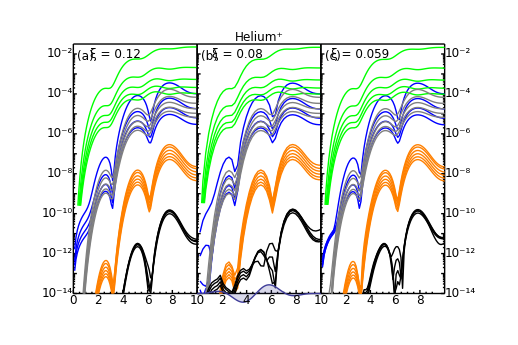

```mathematica
nS=Table[n,{n,1,5}];
nP=Table[n,{n,9,13}];
nD=Table[n,{n,17,19}];
nF=Table[n,{n,20,21}];
nG={22};
ns=Table[n,{n,1,4}];
np=Table[n,{n,9,13}];
nd=Table[n,{n,17,21}];
nf=Table[n,{n,24,29}];
ng=Table[n,{n,30,33}];
nh=Table[n,{n,52,55}];

laserY=-14;
laserAmp=0.5;
laserPl=Plot[laserAmp*laser[2,1.32,t]+laserY,{t,0,10},
Filling->Axis,
AxesOrigin->{0,laserY}];

nlexConvFIG=Figure[
{
ScaledLabel[{0.5,0.98},"Helium^+"],
ScaledLabel[{0.16,0.92},"ξ = 0.12"],
ScaledLabel[{0.45,0.92},"ξ = 0.08"],
ScaledLabel[{0.74,0.92},"ξ = 0.059"],

Multipanel[{{0,1},{0,1}},
{1,3},
XPlotRanges->{0,10},
YPlotRanges->{-14,-1.5}
],

(*He12 vs t*)
FigurePanel[{1,1},
FrameTicks->{Automatic,LogTicks[-14,-2,TickLabelStep->2]}
],
RawGraphics[plotBound[boundF,11,ns,PlotStyle->Blue]],
RawGraphics[plotBound[boundF,11,np,PlotStyle->Green]],
RawGraphics[plotBound[boundF,11,nd,PlotStyle->Gray]],
RawGraphics[plotBound[boundF,11,nf,PlotStyle->Orange]],
RawGraphics[plotBound[boundF,11,ng,PlotStyle->Black]],
(*He08 vs t*)
FigurePanel[{1,2},
FrameTicks->{LinTicks[0.5,10],LogTicks[-14,-2],None,None},
ShowTickLabels->{True,False,False,False}
],
RawGraphics[plotBound[boundG,11,ns,PlotStyle->Blue]],
RawGraphics[plotBound[boundG,11,np,PlotStyle->Green]],
RawGraphics[plotBound[boundG,11,nd,PlotStyle->Gray]],
RawGraphics[plotBound[boundG,11,nf,PlotStyle->Orange]],
RawGraphics[plotBound[boundG,11,ng,PlotStyle->Black]],
RawGraphics[laserPl],
(*He06 vs t*)
FigurePanel[{1,3},
FrameTicks->{LinTicks[0.5,9.5],LogTicks[-14,-2],None,LogTicks[-14,-2,TickLabelStep->2]},
ShowTickLabels->{True,False,False,True}
],
RawGraphics[plotBound[boundH,11,ns,PlotStyle->Blue]],
RawGraphics[plotBound[boundH,11,np,PlotStyle->Green]],
RawGraphics[plotBound[boundH,11,nd,PlotStyle->Gray]],
RawGraphics[plotBound[boundH,11,nf,PlotStyle->Orange]],
RawGraphics[plotBound[boundH,11,ng,PlotStyle->Black]]
},
PlotRange->{{-0.07,1.07},{-0.08,1.05}},ImageSize->72*2*{3.6,2.4}
]
If[False,Export[exportPath<>"nlexConv."<>suffix,nlexConvFIG]]
```

The behavior or P_(4f) (the top orange line) strikes me as odd for it wanders towards the end of the pulse. Expecially for the smaller cuts. See journal F p29

## Dipole

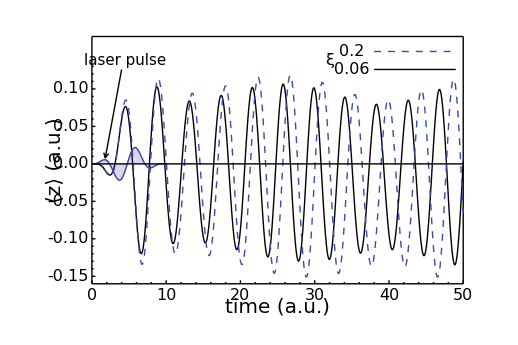

/Users/nevence/Documents/utk/first/zConv.pdf

```mathematica
F[plotDat_List,ω_]:=With[{t=#[[1]]&/@ plotDat,f=#[[2]]&/@plotDat},
 1/(√(2π))Sum[f[[n]] ⅇ^(-I ω t[[n]])(t[[n+1]]-t[[n]]),{n,1,Length[f]-1}]
];
abFT[plotDat_List,ωMAX_,dω_]:=Table[{ω,Abs[F[plotDat,ω]]^2},{ω,0,ωMAX,dω}];
laser[nCycle_,ω_,t_]:=
If[ω t> 0 && (ω t)/(2nCycle)<π,Sin[(ω t)/(2nCycle)]^2 Sin[ω t],0];
(*Damping the end of the function*)
dampTail[dat_,fade_]:=Module[{n=Length[dat]},
With[{x1=n-fade-1},
Join[dat[[;;x1]],Table[{dat[[x1+i,1]],Exp[-5/fade^2 i^2]dat[[x1+i,2]]} ,{i,1,fade}]]
]]
scaleUp[dat_,factor_]:={#[[1]],factor#[[2]]}&/@dat;
logScaleUp[dat_,factor_]:={#[[1]],factor Log[10,#[[2]]]}&/@dat;
zdipA=Union[Import[dataDIR<>"He06LONG/zdip.dat"]];
zdipB=Union[Import[dataDIR<>"He2/zdip.dat"]];

laserY=0;
laserAmp=0.025;
yMin=-0.513;
yMax=-0.415;
pady=0.005;
laserPl=Plot[laserAmp*laser[2,1.32,t]+laserY,{t,0,10},
Filling->Axis,
AxesOrigin->{0,laserY}];
y0=0.15;
dy=0.024;
y1=y0-1dy;
y2=y0-2dy;
y3=y0-3dy;
x1=32;
x2=35;
x3=38;
x4=49;
heStyleList={{Black},{LightGray}};
zConvFIG=Figure[
{
SetOptions[ManualLabel,FontSize->16],
FigurePanel[{{0,1},{0,1}},
PlotRange->{{0,50},{-0.16,0.17}},
FrameTicks->{LinTicks[0,50],LinTicks[-0.16,0.14]},
FontSize->20,
TickFontSize->16,
TickNudge->{-5,{-4,0},0,0},
LabL->"⟨z⟩ (a.u.)",BufferL->4.5,
LabB->"time (a.u.)",BufferB->2.8
],
RawGraphics[ListLinePlot[{zdipA,zdipB},PlotStyle->styleList]],
RawGraphics[laserPl],
SchemeLine[{{0,0},{50,0}}],
RawGraphics[Graphics[{
Sequence@@styleList[[2]],Line[{{x3,y0},{x4,y0}}],
Sequence@@styleList[[1]],Line[{{x3,y1},{x4,y1}}]
}]],
ManualLabel[{x1,(y0+y1)/2},"ξ  "],
ManualLabel[{x2,y0},"0.2  "],
ManualLabel[{x2,y1},"0.06"],
ManualLabel[{4.5,(y1+y0)/2},"laser pulse",FontSize->15],
SchemeArrow[{4,y1},{1.8,0.008}]
},
PlotRange->{{-0.12,1.02},{-0.12,1.02}},ImageSize->72*2*{3.6,2.4}
]
If[export,Export[exportPath<>"zConv."<>suffix,zConvFIG]]
```

## projPsi old and new

```mathematica
(*Finds the max of a list of 2D lists*)
fMAX[dat_]:=With[{fNUM=Length[First[dat]]},
maxList={};
For[i=1,i≤Length[dat],i++,
For[j=3,j≤Length[dat[[i]]],j++,
kx=dat[[i,j,1]];
kz=dat[[i,j,2]];
thisMax=Max[(kx^2+kz^2)#&/@dat[[i,j,3;;]] ];
AppendTo[maxList,thisMax];
];
];
Max[maxList]
]

(*3D plot of the electron's ionization*)
dPdkdΩ[dat_,fNUM_,fMAX_,opts___]:=Show[{ListPlot3D[{#[[1]],#[[2]],((#[[1]])^2+(#[[2]])^2)*#[[fNUM]]}&/@dat,ViewPoint->{10,0,1},PlotRange->{0,fMAX},opts],
Graphics3D[{Thick,Arrow[{{3,0,fMAX},{3,2,fMAX}}],
Text["Laser Polarization",Scaled[{0.8,0.65,1}]]}]}];

(*Ionization Probability*)
ionizationP[dat_List,fNUM_]:=Module[{
dk,dθ,dϕ=π,tol=0.00001,kMAX,sum=0,m,n,points2,angle,xz2rθ,
points,nk,nθ,θnext,fnext,
k,θ,f,radialCS={}},
(*The points on the z-axis must be handled carefully, for it needs to represent a cone, but Sin[θ] give it zero width. See journal E pg 18 for a description of the special case Jacobian.
*)
angle[x_,z_]:=If[x≥0,
If[z≠0,If[z>0,ArcTan[x/z],ArcTan[x/z]+π],π/2],
If[z≠0,If[z<0,ArcTan[x/z]+π,ArcTan[x/z]+2π],3π/2]];
xz2rθ[{x_,z_,f___}]:={√(x^2+z^2),angle[x,z],f};
(* Steps 1 & 2
Reflecting the points which don't lie on the z axis
Turning them into polar cordinates and
Sorting them in increasing r *)
points=Sort[xz2rθ/@Join[dat,Cases[dat,{x_,z_,f___}:>{-x,z,f}/;x≠0]]];
nθ=Last[First[Tally[points,Abs[#1[[1]]- #2[[1]]]<tol&]]];
(* Steps 3 & 4
Partitioning the list and then sorting each according to r *)
points2=Sort[#,#1[[2]]<#2[[2]]&]&/@Partition[points,nθ];
nk=Length[points2];
dk = points2[[2,1,1]]-points2[[1,1,1]];
dθ = points2[[1,2,2]]-points2[[1,1,2]];
(*Print["dk = ",dk,"   dθ = ",dθ,"   dϕ = ",dϕ,"   nθ = ",nθ,"   nk = ",nk];*)
(*Step 5: Integration*)
For[m=1,m≤nk,m++,
For[n=1,n≤nθ,n++,
k=points2[[m,n,1]];
θ=points2[[m,n,2]];
θnext=If[n≠nθ,points2[[m,n+1,2]],2π];
f=points2[[m,n,fNUM]];
fnext=If[n≠nθ,points2[[m,n+1,fNUM]],points2[[m,1,fNUM]]];
(*Abs[Sin[(θ+θnext)/2]] represents the angle half way between this and the next point*)
sum+=(f+fnext)/2*k^2 Abs[Sin[(θ+θnext)/2]]dk dθ dϕ ;
];
];
sum
]
```

### First

```mathematica
dPdkdΩ[dat_,fNUM_,fMAX_,opts___]:=Show[{ListPlot3D[{#[[1]],#[[2]],((#[[1]])^2+(#[[2]])^2)*#[[fNUM]]}&/@dat,ViewPoint->{10,0,1},PlotRange->{0,fMAX},opts],
Graphics3D[{Thick,Arrow[{{3,0,fMAX},{3,2,fMAX}}],
Text["Laser Polarization",Scaled[{0.8,0.65,1}]]}]}]
```

#### Visual Comparison

```mathematica
ionA=Import[dataDIR<>"H2/ion.dat"];
ionB=Import[dataDIR<>"H19/oldIon.dat"];
ionC=Import[dataDIR<>"H19/ion.dat"];
ionD=Import[dataDIR<>"He05/oldIon.dat"];
ionE=Import[dataDIR<>"He05/ion.dat"];
ionF=Import[dataDIR<>"He05/newIon.dat"];
ionG=Import[dataDIR<>"He06e-7/ion.dat"];
tSTEPa=Length[First[ionA]];
tSTEPb=42;
tSTEPc=Length[First[ionC]];
tSTEPd=Length[First[ionD]];
tSTEPe=Length[First[ionE]];
tSTEPf=Length[First[ionF]];
tSTEPg=Length[First[ionG]];
hDAT={ionA,ionB,ionC};
heDAT={ionD,ionE,ionF};
hMAX=fMAX[hDAT];
heMAX=fMAX[heDAT];

Print["Hydrogen cut = 0.2 OLD"];
dPdkdΩ[ionA,tSTEPa,hMAX]
Print["Hydrogen cut = 0.19 mediumOld"];
dPdkdΩ[ionB,tSTEPb,hMAX]
Print["Hydrogen cut = 0.19 New"];
dPdkdΩ[ionC,tSTEPc,hMAX]
Print["He^+ cut = 0.05 OLD"];
dPdkdΩ[ionE,tSTEPe,heMAX]
Print["He^+0.05 Medium OLD"];
dPdkdΩ[ionD,tSTEPd,heMAX]
Print["He^+ cut = 0.05 NEW"];
dPdkdΩ[ionF,tSTEPf,heMAX]
Print["He^+ cut = 0.05 REALLY NEW"];
dPdkdΩ[ionG,tSTEPg,fMAX[{ionG}]]
```

#### Ionization Probability

```mathematica
ionAb=Import[dataDIR<>"H19/oldIon.dat"];
ionA=Import[dataDIR<>"H19/ion.dat"];
ionBb=Import[dataDIR<>"He05/oldIon.dat"];
ionB=Import[dataDIR<>"He05/ion.dat"];
tSTEPa=Length[ionA[[1]]];
tSTEPab=42;
tSTEPionb=Length[ionB[[1]]];
tSTEPbb=Length[ionBb[[1]]];
Print["Total ionization of Hydrogen(0.19) OLD: ",ionizationP[ionAb,tSTEPab]];
Print["Total ionization of Hydrogen(0.19) NEW: ",ionizationP[ionA,tSTEPa]];
Print["Total ionization of He+(0.05)    ?OLD?: ",ionizationP[ionBb,tSTEPbb]];
Print["Total ionization of He+(0.05)      NEW: ",ionizationP[ionB,tSTEPionb]];
```

#### Bound State Excitation

```mathematica
totalExcitationP[dat_List,t_]:=Total[dat[[All,t]]]
boundA=Import[dataDIR<>"H19/ex.dat"];
boundB=Import[dataDIR<>"He05/ex.dat"];
tSTEPa=Length[boundA[[1]]];
tSTEPb=Length[boundB[[1]]];
Print["Total bound state excitation of Hydrogen(0.19) NEW: ",totalExcitationP[boundA,tSTEPa]];
Print["Total bound state excitation of He+(0.05)      NEW: ",totalExcitationP[boundB,tSTEPb]];
```

#### Total Inelastic Excitation Probability

```mathematica
(*Total excitation*)
minusOne[lst_List]:={#[[1]],1-(#[[2]])^2}&/@lst;
totalExA=minusOne@Union[Import[dataDIR<>"H19/overlap.dat"]];
totalExB=minusOne@Union[Import[dataDIR<>"He05/overlap.dat"]];
Print["Total exIon of Hydrogen(0.2)  OLD: ",totalExA[[-1,2]]];
Print["Total exIon of Hydrogen(0.19) NEW: ",totalExB[[-1,2]]];
```

#### Sum

```mathematica
compP[totP_,ionP_,exP_]:={totP,ionP,exP,totP-ionP-exP}
```

```mathematica
Print["Hydrogen 0.19"];
compP[totalExA[[-1,2]],ionizationP[ionA,Length[ionA[[1]]]],totalExcitationP[boundA,Length[boundA[[1]]]]]
Print["He+ 0.05"];
compP[totalExB[[-1,2]],ionizationP[ionB,Length[ionB[[1]]]],totalExcitationP[boundB,Length[boundB[[1]]]]]
```

```mathematica
ionizationP[ionC,tSTEPc]+totalExcitationP[boundB,tSTEPb]
```

### Helium^+

#### Visual Comparison

```mathematica
ionA=Import[dataDIR<>"He05/ion.289983"];
ionB=Import[dataDIR<>"He05/ion.298041"];
tSTEPa=Length[First[ionA]];
tSTEPb=Length[First[ionB]];
heDAT={ionA,ionB};
heMAX=fMAX[heDAT];

Print["He^+ cut = 0.05 OLD"];
dPdkdΩ[ionA,tSTEPa,heMAX]
Print["He^+ cut = 0.05 NEW"];
dPdkdΩ[ionB,tSTEPb,heMAX]
```

#### Ionization Probability

```mathematica
ionA=Import[dataDIR<>"He05/ion.289983"];
ionB=Import[dataDIR<>"He05/ion.298041"];
tSTEPa=Length[First[ionA]];
tSTEPb=Length[First[ionB]];
Print["Total ionization of He+(0.05)      OLD: ",ionizationP[ionA,tSTEPa]];
Print["Total ionization of He+(0.05)      NEW: ",ionizationP[ionB,tSTEPb]];
```

#### Bound State Excitation

```mathematica
totalExcitationP[dat_List,t_]:=Total[dat[[All,t]]]
boundA=Import[dataDIR<>"He05/ex.dat"];
boundB=Import[dataDIR<>"He05/bigEX.dat"];
tSTEPa=Length[boundA[[1]]];
tSTEPb=Length[boundB[[1]]];
Print["Total bound state excitation of He+(0.05): ",totalExcitationP[boundA,tSTEPa]];
Print["Total Ion/Ex of He+(0.05) larger list:     ",totalExcitationP[boundB,tSTEPb]];
```

#### Total Inelastic Excitation Probability

```mathematica
(*Total excitation*)
minusOne[lst_List]:={#[[1]],1-(#[[2]])^2}&/@lst;
totalExA=minusOne@Union[Import[dataDIR<>"He05/overlap.dat"]];
Print["Total Inelastic Excitation He^+(0.05)  OLD: ",totalExA[[-1,2]]];
```

#### Sum

```mathematica
compP[totP_,ionP_,exP_]:={totP,ionP,exP,totP-ionP-exP}
Print["He+ 0.05"];
compP[totalExA[[-1,2]],
ionizationP[ionA,Length[ionA[[1]]]],
totalExcitationP[boundA,Length[boundA[[1]]]]]
Print["He+ 0.05 New:"];
compP[totalExA[[-1,2]],
ionizationP[ionB,Length[ionB[[1]]]],
totalExcitationP[boundB,Length[boundB[[1]]]]]
```

Hmm, when do we cross over the exactly 1 threshold?

```mathematica
plotN[dat_,fNUM_,expectedProb_]:=Module[{
totalN=Length[dat],
maxN=Max[#[[1]]&/@dat],
Pnl={},
Pn={},
Sn={},
n,ℓ},
Pnl=Table[Table[0,{ℓ,0,n-1}],{n,maxN}];
(* sort Subscript[P, nl] according to n*)
Do[Pnl[[dat[[ii,1]],dat[[ii,2]]+1]]=dat[[ii,fNUM]],{ii,totalN}];
Pn=Total[#]&/@Pnl[[2;;]];
Sn=Table[Sum[Pn[[jj]],{jj,1,ii}],{ii,1,maxN-1}];
(*FindFit[Total[#]&/@Pnl,a x^p,{a,p},x]*)
GraphicsGrid[{{
ListLogPlot[Pn,PlotStyle->PointSize[0.015],PlotRange->All],
ListLinePlot[expectedProb-#&/@Sn,
PlotStyle->PointSize[0.015],
PlotRange->{expectedProb-Sn[[-1]],4*^-4},
PlotLabel->"(Expected - total) bound state excitation",
FrameLabel->{"n","discrepancy"}]
}}]
]
plotN[boundB,4,totalExA[[-1,2]]-ionizationP[ionB,Length[ionB[[1]]]]]
```

## Norm, Total Ionization, Excitation

### Routines

```mathematica
ionizationP[dat_List,fNUM_]:=Module[{
dk,dθ,dϕ=π,tol=0.00001,kMAX,sum=0,m,n,points2,angle,xz2rθ,
points,nk,nθ,θnext,fnext,
k,θ,f,radialCS={}},
(*The points on the z-axis must be handled carefully, for it needs to represent a cone, but Sin[θ] give it zero width. See journal E pg 18 for a description of the special case Jacobian.
*)
angle[x_,z_]:=If[x≥0,
If[z≠0,If[z>0,ArcTan[x/z],ArcTan[x/z]+π],π/2],
If[z≠0,If[z<0,ArcTan[x/z]+π,ArcTan[x/z]+2π],3π/2]];
xz2rθ[{x_,z_,f___}]:={√(x^2+z^2),angle[x,z],f};
(* Steps 1 & 2
Reflecting the points which don't lie on the z axis
Turning them into polar cordinates and
Sorting them in increasing r *)
points=Sort[xz2rθ/@Join[dat,Cases[dat,{x_,z_,f___}:>{-x,z,f}/;x≠0]]];
nθ=Last[First[Tally[points,Abs[#1[[1]]- #2[[1]]]<tol&]]];
(* Steps 3 & 4
Partitioning the list and then sorting each according to r *)
points2=Sort[#,#1[[2]]<#2[[2]]&]&/@Partition[points,nθ];
nk=Length[points2];
dk = points2[[2,1,1]]-points2[[1,1,1]];
dθ = points2[[1,2,2]]-points2[[1,1,2]];
(*Print["dk = ",dk,"   dθ = ",dθ,"   dϕ = ",dϕ,"   nθ = ",nθ,"   nk = ",nk];*)
(*Step 5: Integration
*)
For[m=1,m≤nk,m++,
For[n=1,n≤nθ,n++,
k=points2[[m,n,1]];
θ=points2[[m,n,2]];
θnext=If[n≠nθ,points2[[m,n+1,2]],2π];
f=points2[[m,n,fNUM]];
fnext=If[n≠nθ,points2[[m,n+1,fNUM]],points2[[m,1,fNUM]]];
(*If[k>kMAX,kMAX=k];*)
sum+=(f+fnext)/2*k^2 Abs[Sin[(θ+θnext)/2]]dk dθ dϕ ;
];
];
sum
]
totalExcitationP[dat_List]:=Module[{t=Length[First[dat]]},Total[#[[t]]&/@dat]]
totalInfo[str_]:=Module[{groundProb,
ionProb=ionizationP[Import[str<>"/ion.dat"],-1],
exProb=totalExcitationP[Import[str<>"/ex.dat"]],
norm=Import[str<>"/norm.dat"][[-1,2]],
overlap=Import[str<>"/overlap.dat"][[-1,2]]},
groundProb=(overlap*norm)^2;
Print["ionization Prob= ",ionProb];
Print["excitation Prob = ",exProb];
Print["ground Prob = ",groundProb];
Print["total Prob = ",NumberForm[(ionProb+exProb+groundProb)/norm^2,10]];
]
```

```mathematica
totalInfo["/Users/nevence/Documents/utk/data/He05"]
```

ionization Prob= 0.000836277

excitation Prob = 0.0244837

ground Prob = 0.974604

total Prob = 0.9999209176

### Ionization

```mathematica
ionA=Import[dataDIR<>"2Li03e-5/ion.dat"];ionB=Import[dataDIR<>"2Li03e-6/ion.dat"];
ionC=Import[dataDIR<>"He06e-3/ion.dat"];
ionD=Import[dataDIR<>"He06e-4/ion.dat"];
ionE=Import[dataDIR<>"He06e-5/ion.dat"];
ionF=Import[dataDIR<>"He06e-6/ion.dat"];
ionG=Import[dataDIR<>"He06e-7/ion.dat"];

tSTEPa=Length[First[ionA]];
tSTEPb=Length[First[ionB]];
tSTEPc=Length[First[ionC]];
tSTEPd=Length[First[ionD]];
tSTEPe=Length[First[ionE]];
tSTEPf=Length[First[ionF]];
tSTEPg=Length[First[ionG]];

ionizationP[ionA,tSTEPa]
ionizationP[ionB,tSTEPb]
ionizationP[ionC,tSTEPc]
ionizationP[ionD,tSTEPd]
ionizationP[ionE,tSTEPe]
ionizationP[ionF,tSTEPf]
ionizationP[ionG,tSTEPg]
```

### Excitation

```mathematica
totalExcitationP[Import[dataDIR<>"2Li03e-5/ex.dat"]]
totalExcitationP[Import[dataDIR<>"2Li03e-6/ex.dat"]]
totalExcitationP[Import[dataDIR<>"He06e-3/ex.dat"]]
totalExcitationP[Import[dataDIR<>"He06e-4/ex.dat"]]
totalExcitationP[Import[dataDIR<>"He06e-5/ex.dat"]]
totalExcitationP[Import[dataDIR<>"He06e-6/ex.dat"]]
totalExcitationP[Import[dataDIR<>"He06e-7/ex2.dat"]]
```

```mathematica
totalExcitationP[Import[dataDIR<>"He12e-7/ex.dat"]]
totalExcitationP[Import[dataDIR<>"He08/ex.dat"]]
totalExcitationP[Import[dataDIR<>"He06e-7/ex2.dat"]]
totalExcitationP[Import[dataDIR<>"He05/ex.dat"]]
```

### P_n1

```mathematica
exDAT=Cases[Import[dataDIR<>"H2t5/ex2.dat"],{n_,l_,m_,prob_}:>{n,prob}];
sumDAT=#[[2]]&/@exDAT;
exTotDAT=Table[{n+1,Sum [sumDAT[[i]],{i,1,n}]},{n,1,Length[sumDAT]}];
ListLinePlot[{exDAT,exTotDAT},PlotRange->All]
```

### k mesh

```mathematica
ionA=Import[dataDIR<>"H2t5/ion10.dat"];
ionB=Import[dataDIR<>"H2t5/ion20.dat"];
ionC=Import[dataDIR<>"H2t5/ion40.dat"];
ionD=Import[dataDIR<>"H2t5/ion80.dat"];
totalInfo[str_,nEx_,nIon_]:=Module[{
ionH=ionizationP[Import[str<>"/ion"<>ToString[nIon]<>".dat"],-1],
exH=totalExcitationP[Import[str<>"/ex"<>ToString[nEx]<>".dat"]],
groundH=(Import[str<>"/overlap.dat"][[-1,2]])^2},
Print["ionization Prob= ",ionH];
Print["excitation Prob = ",exH];
Print["ground Prob = ",groundH];
Print["total Prob = ",N[ionH+exH+groundH,10]];
]
totalInfo[dataDIR<>"H2t5",1,10]
```

```mathematica
totalInfo[dataDIR<>"H2t5",1,20]
```

```mathematica
totalInfo[dataDIR<>"H2t5",2,20]
```

```mathematica
totalInfo[dataDIR<>"H2t5",2,40]
```

### | (c^ion)ℓ|^2

#### Hydrogen

ℓ=0

```mathematica
0.97640916-0.9760864
```

ℓ=1

```mathematica
0.0232226-0.00756
```

ℓ=1

```mathematica
0.0232226-0.00756
```

ℓ=2

```mathematica
0.0001774103134-2.91*^-6
```

ℓ=3

```mathematica
0.00000111699014-2*^-10
```

ℓ=4

```mathematica
0.000000005645694156-2.9*^-12
```

### Totals

#### H

```mathematica
totalInfo[dataDIR<>"H05e-7"](*Subscript[N, max]=50   Subscript[Δθ, k]=40 Δk=0.05*)
```

ionization Prob= 0.0159802

excitation Prob = 0.00759694

ground Prob = 0.97626

total Prob = 1.000024443

```mathematica
totalInfo[dataDIR<>"H1e-7"](*Subscript[N, max]=9   Subscript[Δθ, k]=10 Δk=0.05*)
```

ionization Prob= 0.0159457

excitation Prob = 0.00743013

ground Prob = 0.976455

total Prob = 0.9998591918

```mathematica
totalInfo[dataDIR<>"H2e-7"] (*Subscript[N, max]=9   Subscript[Δθ, k]=10 Δk=0.05*)
```

ionization Prob= 0.0157061

excitation Prob = 0.0074024

ground Prob = 0.976747

total Prob = 0.9998599773

```mathematica
totalInfo[dataDIR<>"H2"] (*Subscript[N, max]=9   Subscript[Δθ, k]=20 Δk=0.05*)
```

```mathematica
totalInfo[dataDIR<>"H2"] (*Subscript[N, max]=20  Subscript[Δθ, k]=20 Δk=0.05*)
```

```mathematica
totalInfo[dataDIR<>"H3"](*Subscript[N, max]=9   Subscript[Δθ, k]=10 Δk=0.05*)
```

#### He^+

```mathematica
totalInfo[dataDIR<>"He06e-7"]
```

```mathematica
totalInfo[dataDIR<>"He06e-6"]
```

```mathematica
totalInfo[dataDIR<>"He06e-5"]
```

```mathematica
totalInfo[dataDIR<>"He06e-4"]
```

```mathematica
totalInfo[dataDIR<>"He06e-3"]
```

```mathematica
totalInfo[dataDIR<>"He2"]
```

```mathematica
totalInfo[dataDIR<>"He12e-7"]
```

```mathematica
totalInfo[dataDIR<>"He08"]
```

```mathematica
totalInfo[dataDIR<>"He06e-7"]
```

```mathematica
totalInfo[dataDIR<>"He05"]
```

#### Li^(2+)

```mathematica
totalInfo[dataDIR<>"2Li03e-6"]
```

```mathematica
totalInfo[dataDIR<>"2Li03e-5"]
```

```mathematica
totalInfo[dataDIR<>"2Li03b"]
```

## Total Excitation

```mathematica
minusOne[lst_List]:={#[[1]],1-(#[[2]])^2}&/@lst;
totalExA=minusOne@Union[Import[dataDIR<>"H3/overlap.dat"]];
totalExB=minusOne@Union[Import[dataDIR<>"H19/overlap.dat"]];
totalExC=minusOne@Union[Import[dataDIR<>"H1/overlap.dat"]];
totalExD=minusOne@Union[Import[dataDIR<>"H05/overlap.dat"]];

totalExE=minusOne@Union[Import[dataDIR<>"He2/overlap.dat"]];
totalExF=minusOne@Union[Import[dataDIR<>"He12/overlap.dat"]];
totalExG=minusOne@Union[Import[dataDIR<>"He08/overlap.dat"]];
totalExH=minusOne@Union[Import[dataDIR<>"He06/overlap.dat"]];
exHVcutDAT=Transpose[{{0.3,0.187,0.1,0.05},#[[-1,2]]&/@{totalExA,totalExB,totalExC,totalExD}}];
exHeVcutDAT=Transpose[{{0.2,0.12,0.08,0.059},#[[-1,2]]&/@{totalExE,totalExF,totalExG,totalExH}}];
laser[nCycle_,ω_,t_]:=
If[ω t> 0 && (ω t)/(2nCycle)<π,Sin[(ω t)/(2nCycle)]^2 Sin[ω t],0];
laserY=0;
laserAmp=0.003;
laserPl=Plot[laserAmp*laser[2,1.32,t]+laserY,{t,0,10},
Filling->Axis,
AxesOrigin->{0,laserY}];

baseList=Table[{Thickness[0.001*√n],GrayLevel[(13-3n)/31]},{n,1,4}];
heStyleList=Prepend[#,Dashing[0.0012{3,2}]]&/@baseList
hStyleList=Prepend[#,Dashing[0.0025{5,2}]]&/@baseList;

exConvFIG=Figure[
{
ScaledLabel[{0.5,0.96},"Total Inelastic Excitation:   1 - |⟨ψ_0|ψ(t)⟩|^2",FontSize->18],
Multipanel[
{{0,1},{0,1}},
{2,2},
XPanelSizes->{3,1},
XPlotRanges->{{0,10},{0,0.3}},
XFrameLabels->{textit["time [au]"],textit["cut"]},
BufferB->2.5,
TickFontSize->10
],
(*exH vs cut*)
FigurePanel[{1,2},
YPlotRange->{0.0225,0.02375},
FrameTicks-> {LinTicks[0,0.3,0.1,2],LinTicks[0.0225,0.02375],None,LinTicks[0.022625,0.02375]},
ShowTickLabels->{False,False,False,True}
],
ScaledLabel[{0.5,0.9},"Hydrogen"],
RawGraphics[Plot[Evaluate[Fit[exHVcutDAT,{1,x,x^2,x^3},x]],{x,0.025,0.3}]],
RawGraphics[ListPlot[exHVcutDAT,PlotStyle->PointSize[0.02]]],
SchemeLine[{{0.185,0},{0.185,0.0233}},Dashing->True],
(*exHe vs cut*)
FigurePanel[{2,2},
YPlotRange->{0.025,0.031},
FrameTicks-> {LinTicks[0,0.3,0.1,2],LinTicks[0.025,0.031],None,LinTicks[0.025,0.031]},
ShowTickLabels->{True,False,False,True}
],
RawGraphics[Plot[Evaluate[Fit[exHeVcutDAT[[2;;]],{1,x,x^2},x]],{x,0.025,0.22}]],
RawGraphics[ListPlot[exHeVcutDAT,PlotStyle->PointSize[0.02]]],
ScaledLabel[{0.4,0.9},"He^+"],
SchemeLine[{{0.085,0},{0.085,0.026}},Dashing->True],

(*ex vs time*)
FigurePanel[{2,1},
FrameTicks->{LinTicks[0,9.5],LinTicks[0,0.04]},
YPlotRange->{0,0.04},
PanelAdjustments->{{0,0},{0,1}},
PanelLetterFontSize->18
],
RawGraphics[ListLinePlot[{totalExD,totalExC,totalExB,totalExA},PlotStyle->hStyleList]],
RawGraphics[ListLinePlot[{totalExH,totalExG,totalExF,totalExE},PlotStyle->heStyleList,PlotRange->All]],
RawGraphics[laserPl],
RawGraphics[Graphics[{
Sequence@@hStyleList[[1]],Line[{{0.25,0.032},{2.25,0.032}}],
Sequence@@hStyleList[[2]],Line[{{0.25,0.030},{2.25,0.03}}],
Sequence@@hStyleList[[3]],Line[{{0.25,0.028},{2.25,0.028}}],
Sequence@@hStyleList[[4]],Line[{{0.25,0.026},{2.25,0.026}}],
Sequence@@heStyleList[[1]],Line[{{0.25,0.020},{2.25,0.02}}],
Sequence@@heStyleList[[2]],Line[{{0.25,0.018},{2.25,0.018}}],
Sequence@@heStyleList[[3]],Line[{{0.25,0.016},{2.25,0.016}}],
Sequence@@heStyleList[[4]],Line[{{0.25,0.014},{2.25,0.014}}]
}]],
ManualLabel[{1.3,0.034},"Hydrogen"],
ManualLabel[{3,0.034},"cut "],
ManualLabel[{3,0.032},"0.3 "],
ManualLabel[{3,0.03},"0.2 "],
ManualLabel[{3,0.028},"0.1 "],
ManualLabel[{3,0.026},"0.05"],
ManualLabel[{1.3,0.022},"He^+"],
ManualLabel[{3,0.022},"cut "],
ManualLabel[{3,0.020},"0.2  "],
ManualLabel[{3,0.018},"0.12"],
ManualLabel[{3,0.016},"0.08"],
ManualLabel[{3,0.014},"0.06"]
},
PlotRange->{{-0.1,1.1},{-0.08,1.08}},ImageSize->72*2*{3.6,2.4}
]
If[True,Export[exportPath<>"exConv."<>suffix,exConvFIG]]
```

Comparison

## 152 nm

### Routines

```mathematica
dPdk[dat_List,fNUM_,hue_]:=Module[{
dk,dθ,dϕ=π,tol=0.00001,kMAX,sum,
points,nk,nθ,θnext,fnext,
k,θ,f,radialCS={}},
(* The task is to integrate the cross section over the angular variables taking the left right symmetries into accout.

The points on the z-axis must be handled carefully, for it needs to represent a cone, but Sin[θ] give it zero width. See journal E pg 18 for a description of the special case Jacobian.
*)
angle[x_,z_]:=If[x≥0,
If[z≠0,If[z>0,ArcTan[x/z],ArcTan[x/z]+π],π/2],
If[z≠0,If[z<0,ArcTan[x/z]+π,ArcTan[x/z]+2π],3π/2]];
xz2rθ[{x_,z_,f___}]:={√(x^2+z^2),angle[x,z],f};
(* Steps 1 & 2
Reflecting the points which don't lie on the z axis
Turning them into polar cordinates and
Sorting them in increasing r *)
points=Sort[xz2rθ/@Join[dat,Cases[dat,{x_,z_,f___}:>{-x,z,f}/;x≠0]]];
nθ=Last[First[Tally[points,Abs[#1[[1]]- #2[[1]]]<tol&]]];
(* Steps 3 & 4
Partitioning the list and then sorting each according to r *)
points2=Sort[#,#1[[2]]<#2[[2]]&]&/@Partition[points,nθ];
nk=Length[points2];
dk = points2[[2,1,1]]-points2[[1,1,1]];
dθ = points2[[1,2,2]]-points2[[1,1,2]];
(*Print["dk = ",dk,"   dθ = ",dθ,"   dϕ = ",dϕ,"   nθ = ",nθ,"   nk = ",nk];*)
(* Step 5
Integrating θ *)
For[m=1,m≤nk,m++,
sum=0;
For[n=1,n≤nθ,n++,
k=points2[[m,n,1]];
θ=points2[[m,n,2]];
θnext=If[n≠nθ,points2[[m,n+1,2]],2π];
fnext=If[n≠nθ,points2[[m,n+1,fNUM]],points2[[m,1,fNUM]]];
If[k>kMAX,kMAX=k];
(*Print[k,"  ",N[θ],"   k dθ = ",k dθ,"    π k Abs[Sin[(θ+θnext)/2]] ",π k Abs[Sin[(θ+θnext)/2]]];*)
f=points2[[m,n,fNUM]];
(*sum+=f * dk * k*dθ * k*dϕ*Abs[Sin[(θ+θnext)/2]];*)
sum+=(f+fnext)/2*k^2 Abs[Sin[(θ+θnext)/2]]dθ dϕ ;
If[n==nθ,AppendTo[radialCS,{k,sum}];
];
];
];
f=Interpolation[Prepend[radialCS,{0,0}]];
Off[Interpolation::inhr];
(* Step 6
Plotting k *)
(*Print["Total Cross Section = ",Total[#[[2]]*dk&/@radialCS]];*)
Plot[f[x],{x,0,radialCS[[-1,1]]},

(*Evaluate@Sequence[csOPTS[hue]],*)
PlotStyle->styleList[[hue]],
FrameLabel->{"momentum","dP/dk"},
FrameTicks->{None,Automatic},
RotateLabel->False
]
]



dPdE[dat_List,fNUM_,hue_]:=Module[{
dk,dθ,dϕ=π,tol=0.00001,kMAX,sum,
points,nk,nθ,θnext,fnext,
k,θ,f,radialCS={}},
(* The task is to integrate the cross section over the angular variables taking the left right symmetries into accout.

The points on the z-axis must be handled carefully, for it needs to represent a cone, but Sin[θ] give it zero width. See journal E pg 18 for a description of the special case Jacobian.
*)
angle[x_,z_]:=If[x≥0,
If[z≠0,If[z>0,ArcTan[x/z],ArcTan[x/z]+π],π/2],
If[z≠0,If[z<0,ArcTan[x/z]+π,ArcTan[x/z]+2π],3π/2]];
xz2rθ[{x_,z_,f___}]:={√(x^2+z^2),angle[x,z],f};
(* Steps 1 & 2
Reflecting the points which don't lie on the z axis
Turning them into polar cordinates and
Sorting them in increasing r *)
points=Sort[xz2rθ/@Join[dat,Cases[dat,{x_,z_,f___}:>{-x,z,f}/;x≠0]]];
nθ=Last[First[Tally[points,Abs[#1[[1]]- #2[[1]]]<tol&]]];
(* Steps 3 & 4
Partitioning the list and then sorting each according to r *)
points2=Sort[#,#1[[2]]<#2[[2]]&]&/@Partition[points,nθ];
nk=Length[points2];
dk = points2[[2,1,1]]-points2[[1,1,1]];
dθ = points2[[1,2,2]]-points2[[1,1,2]];
(*Print["dk = ",dk,"   dθ = ",dθ,"   dϕ = ",dϕ,"   nθ = ",nθ,"   nk = ",nk];*)
(* Step 5
Integrating θ *)
For[m=1,m≤nk,m++,
sum=0;
For[n=1,n≤nθ,n++,
k=points2[[m,n,1]];
θ=points2[[m,n,2]];
θnext=If[n≠nθ,points2[[m,n+1,2]],2π];
fnext=If[n≠nθ,points2[[m,n+1,fNUM]],points2[[m,1,fNUM]]];
If[k>kMAX,kMAX=k];
(*Print[k,"  ",N[θ],"   k dθ = ",k dθ,"    π k Abs[Sin[(θ+θnext)/2]] ",π k Abs[Sin[(θ+θnext)/2]]];*)
f=points2[[m,n,fNUM]];
(*sum+=f * dk * k*dθ * k*dϕ*Abs[Sin[(θ+θnext)/2]];*)
sum+=(f+fnext)/2*k Abs[Sin[(θ+θnext)/2]]dθ dϕ ;
If[n==nθ,AppendTo[radialCS,{k^2/2,sum}];
];
];
];
f=Interpolation[Prepend[radialCS,{0,radialCS[[1,2]]}]];
Off[Interpolation::inhr];
(* Step 6
Plotting k *)
(*Print["Total Cross Section = ",Total[#[[2]]*dk&/@radialCS]];*)
Plot[f[x],{x,0.0,radialCS[[-1,1]]},
PlotRange->All,
PlotStyle->styleList[[hue]]
]
]


rawGraphicsdPdΩ[dat_List,fNUM_,hue_]:=Module[{
dk,dθ,dϕ=2π,tol=0.00001,kMAX,sum,sin,pup,pdown,xMAX,yMAX,angle,xz2rθ,points,points2,i,nk,nθ,m,n,tSum=0,ylowerMAX,yupperMAX,
k,θ,θnext,f,angularCS={},debug=False},
(*The points on the z-axis must be handled carefully, for it needs to represent a cone, but Sin[θ] give it zero width. See journal E pg 18 for a description of the special case Jacobian.
*)
angle[x_,z_]:=If[x≥0,
If[z≠0,If[z>0,ArcTan[x/z],ArcTan[x/z]+π],π/2],
If[z≠0,If[z<0,-ArcTan[x/z]+π,-ArcTan[x/z]],π/2]];
xz2rθ[{x_,z_,f___}]:={√(x^2+z^2),angle[x,z],f};
(* Steps 1 & 2
Turning them into polar cordinates and
Sorting them in increasing θ *)
points=Sort[xz2rθ/@dat,#1[[2]]<#2[[2]]&];
For[i=1,i≤Length[points]-2,i++,
If[Abs[points[[i,2]]-points[[i+1,2]]]>tol,
nk=i;
Break[];
];
];

dk = Abs[points[[2,1]]-points[[1,1]]];
(* Steps 3 & 4
Partitioning the list and then sorting each according to r *)
points2=Sort/@Partition[points,nk];

nθ=Length[points2];
dθ = Abs[points2[[2,1,2]]-points2[[1,1,2]]];
sin[θ_]:=If[((Abs[θ]>tol)&&(π-Abs[θ])>tol),Sin[θ],1/2 Sin[dθ/4]];
(*Print["dk = ",dk,"   dθ = ",dθ,"   dϕ = ",dϕ,"   nθ = ",nθ,"   nk = ",nk];*)
For[m=1,m≤nθ,m++,
sum=0;
θ=points2[[m,1,2]];
(* Step 5
Integrate dk *)
For[n=1,n<nk,n++,
k=points2[[m,n,1]];
f=points2[[m,n,fNUM]];
(*θ is in the middle *)
sum+=f*k^2 dk;
tSum+=f*k^2 Sin[θ]dk dθ dϕ;
];
AppendTo[angularCS,{θ,sum}];
If[debug,Print[angularCS[[-1]]]];
];

f=Interpolation[angularCS];
Off[Interpolation::inhr];
sum=0;
For[i=1,i≤Length[angularCS],i++,
sum+= sin[angularCS[[i,1]]]dθ dϕ *angularCS[[i,2]];
];
If[debug,Print["Total Ionization Probability = ",sum]];
pup=PolarPlot[f[θ-π/2],{θ,π/2,3π/2},
PlotStyle->styleList[[hue]],
Axes->None
];
Off[InterpolatingFunction::"dmval"];
pdown=PolarPlot[f[π/2-θ],{θ,-π/2,π/2},
PlotStyle->styleList[[hue]],
FrameTicks->None,
Axes->None
];
xMAX=Max[#[[2]]*Sin[#[[1]]]&/@angularCS];
yupperMAX=Max[#[[2]]*Cos[#[[1]]]&/@angularCS];
ylowerMAX=Max[-#[[2]]*Cos[#[[1]]]&/@angularCS];
If[debug,Print["xMAX = ",xMAX]];
If[debug,Print["yupperMAX = ",yupperMAX]];
If[debug,Print["ylowerMAX = ",ylowerMAX]];
Sequence@@{RawGraphics[pdown],RawGraphics[pup]}
]
```

### Prereq

```mathematica
(*Finds the max of a list of 2D lists*)
fMAX[dat_]:=With[{fNUM=Length[First[dat]]},
maxList={};
For[i=1,i≤Length[dat],i++,
For[j=3,j≤Length[dat[[i]]],j++,
kx=dat[[i,j,1]];
kz=dat[[i,j,2]];
thisMax=Max[(kx^2+kz^2)#&/@dat[[i,j,3;;]] ];
AppendTo[maxList,thisMax];
];
];
Max[maxList]
]
(*3D plot of the electron's ionization*)
dPdkdΩ[dat_,fNUM_,fMAX_,opts___]:=Show[{ListPlot3D[{#[[1]],#[[2]],((#[[1]])^2+(#[[2]])^2)*#[[fNUM]]}&/@dat,ViewPoint->{10,0,1},PlotRange->{0,fMAX},opts],
Graphics3D[{Thick,Arrowheads[{-0.08,0.08}],Arrow[{{3,-2,fMAX},{3,2,fMAX}}],
Text["Laser Polarization",Scaled[{0.8,0.5,1}]],
Text[Style["q_x",Large],Scaled[{0.5,0.0,0}]],
Text[Style["q_z",Large],Scaled[{1.0,0.5,0}]]
}]}];

aDIR=dataDIR<>"152H3e-6/";
bDIR=dataDIR<>"152H3e-5/";
ionA=Import[aDIR<>"ion.dat"];
ionB=Import[bDIR<>"ion.dat"];
tSTEPa=Length[First[ionA]];
tSTEPb=Length[First[ionB]];
(*fMAXn=fMAX[{ionA,ionB}];
dPdkdΩ[ionA,tSTEPa,fMAXn]
dPdkdΩ[ionB,tSTEPb,fMAXn]*)
```

### First Fig

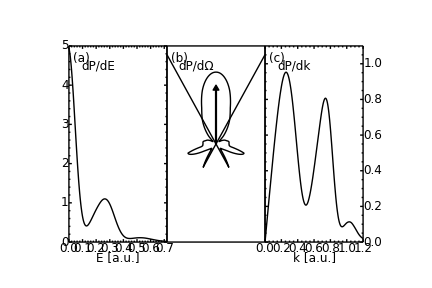

```mathematica
With[{kMAX=1.2,zoom=0.125,shiftY=0,kYMAX=1.1,eYMAX=5},Figure[{
Multipanel[
{{0,1},{0,1}},
{1,3},
BufferB->3
],
(*dPdE*)
FigurePanel[{1,1},
PlotRange->{{0,1/2 kMAX^2},{0,eYMAX}},
LabB->"E [a.u.]"
],
ScaledLabel[{0.3,0.9},"dP/dE"],
RawGraphics[dPdE[ionA,tSTEPa,1]],
(*dPdΩ*)
FigurePanel[{1,2},
PlotRange->zoom{{-1,1},{-2-shiftY,2-shiftY}},
ShowTicks->{False,False,False,False}
],
rawGraphicsdPdΩ[ionA,tSTEPa,1],
SchemeArrow[{{0,0},{0,0.6*zoom(2-shiftY)}},ArrowType->ShapeArrow,Width->1],
ScaledLabel[{0.3,0.9},"dP/dΩ"],
(*dPdk*)
FigurePanel[{1,3},
PlotRange->{{0,kMAX},{0,kYMAX}},
LabB->"k [a.u.]",
ShowTickLabels->{True,False,False,True}
],
RawGraphics[dPdk[ionA,tSTEPa,1]],
ScaledLabel[{0.3,0.9},"dP/dk"]
},
PlotRange->{{-0.1,1.1},{-0.1,1.1}},ImageSize->72*2*{3,2}
]]
```

### Energy Fig

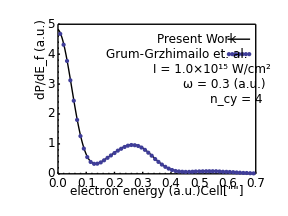

/Users/nevence/Documents/utk/thesis/compdPdE.pdf

```mathematica
grumDAT=Import[exportPath<>"compdPdE.dat"];
grumOPT=PlotStyle->{PointSize[Small]};
ionA=Import[dataDIR<>"152H1b/ion.dat"];
ionB=Import[dataDIR<>"152H3e-5/ion.dat"];
tSTEPa=Length[ionA[[1]]];
compdPdEFIG=Figure[{
FigurePanel[{{0,1},{0,1}},
FrameTicks->Automatic,
TickNudge->{-3,{-3,0},0,0},
PlotRange->{{0,0.7},{0,5}},
LabB->"electron energy (a.u.)Cell[""]",BufferB->3.5,
LabL->"dP/dE_f (a.u.)",BufferL->3.5,OffsetL->{-0.7,0}
],
ScaledLabel[{0.7,0.9},"Present Work"],
ScaledLabel[{0.6,0.8},"Grum-Grzhimailo et. al."],
ScaledLabel[{0.78,0.7},"I = 1.0×10^15 W/cm^2"],
ScaledLabel[{0.84,0.6},"ω = 0.3 (a.u.)"],
ScaledLabel[{0.9,0.5},"n_cy = 4"],
SchemeLine[{{0.60,4.5},{0.68,4.5}}],
RawGraphics[ListPlot[Table[{n,4.0},{n,0.605,0.68,0.012}],grumOPT]],
RawGraphics[dPdE[ionA,tSTEPa,1]],
RawGraphics[ListPlot[grumDAT,grumOPT,PlotRange->All]]
},PlotRange->{{-0.16,1.03},{-0.15,1.03}},ImageSize->72*{4,3}
]
If[export,Export[exportPath<>"compdPdE."<>suffix,compdPdEFIG]]
Clear[x0,x1,x2,x3,dyA,yA0,yA1,yA2,yA3,yA4,dyB,yB0,yB1,yB2,yB3,yB4,dA,dB]
```

### Compare 152H3 & 152H2 & 152H1

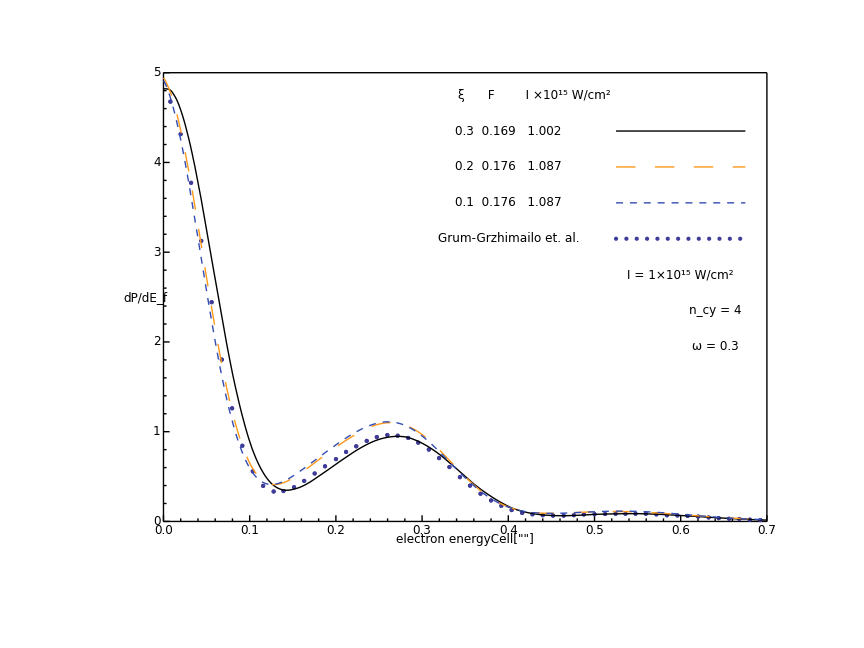

```mathematica
grumDAT=Import[exportPath<>"compdPdE.dat"];
grumOPT=PlotStyle->{PointSize[Medium]};
ionA=Import[dataDIR<>"152H3e-5/ion.dat"];
ionB=Import[dataDIR<>"152H2/ion.dat"];
ionC=Import[dataDIR<>"152H1/ion.dat"];
tSTEPa=Length[ionA[[1]]];
tSTEPb=Length[ionB[[1]]];
tSTEPc=Length[ionC[[1]]];
dy=-0.4;
y0=4.75;
y1=y0+dy;
y2=y0+2dy;
y3=y0+3dy;
y4=y0+4dy;
y5=y0+5dy;
y6=y0+6dy;
y7=y0+7dy;
x0=0.4;
x1=0.525;
x2=0.675;
compdPdEFIG=Figure[{
FigurePanel[{{0,1},{0,1}},
FrameTicks->Automatic,
TickNudge->{-3,{-3,0},0,0},
PlotRange->{{0,0.7},{0,5}},
LabB->"electron energyCell[""]",BufferB->3.5,
LabL->"dP/dE_f",BufferL->3.5,
OrientationL->Horizontal
],
RawGraphics[ListPlot[grumDAT,grumOPT,PlotRange->All]],
RawGraphics[Graphics[{
Sequence@@styleList[[1]],Line[{{x1,y1},{x2,y1}}],
Sequence@@styleList[[3]],Line[{{x1,y2},{x2,y2}}],
Sequence@@styleList[[2]],Line[{{x1,y3},{x2,y3}}]
}]],
RawGraphics[ListPlot[Table[{n,y4},{n,0.525,0.68,0.012}],grumOPT]],
ManualLabel[{0.43,y0},"ξ      F        I ×10^15 W/cm^2"],
ManualLabel[{x0,y1},"0.3  0.169   1.002"],
ManualLabel[{x0,y2},"0.2  0.176   1.087"],
ManualLabel[{x0,y3},"0.1  0.176   1.087"],
ManualLabel[{x0,y4},"Grum-Grzhimailo et. al."],
ManualLabel[{0.60,y5},"I = 1×10^15 W/cm^2"],
ManualLabel[{0.64,y6},"n_cy = 4"],
ManualLabel[{0.64,y7},"ω = 0.3"],
RawGraphics[ListPlot[grumDAT,grumOPT,PlotRange->All]],


RawGraphics[dPdE[ionA,tSTEPa,1]],
RawGraphics[dPdE[ionB,tSTEPb,3]],
RawGraphics[dPdE[ionC,tSTEPc,2]]
},PlotRange->{{-0.14,1.03},{-0.15,1.03}},ImageSize->72*3{4,3}
]
```

### Power Spectrum Figure

```mathematica
laser[nCycle_,ω_,t_]:=
If[ω t> 0 && (ω t)/(2nCycle)<π,Sin[(ω t)/(2nCycle)]^2 Sin[ω t],0];
F[plotDat_List,ω_]:=With[{t=#[[1]]&/@ plotDat,f=#[[2]]&/@ plotDat},
 1/(√(2π))Sum[f[[n]] ⅇ^(-I ω t[[n]])(t[[n+1]]-t[[n]]),{n,1,Length[f]-1}]
];
abFT[plotDat_List,dω_,ωMAX_]:=Table[{ω,Abs[F[plotDat,ω]]^2},{ω,0,ωMAX,dω}];
```

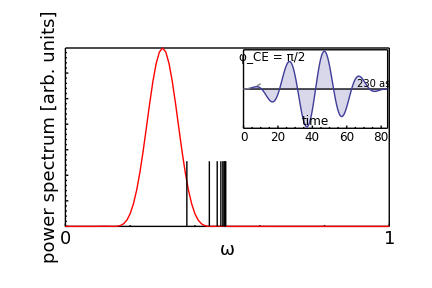

```mathematica
laserFIG=Module[{nCycles=4,ω=0.3,ωMAX=1,dω=0.01,lowerFWHM=0.2,upperFWHM=0.4,eps1=0.3,max1,lData,ftlData,ftlPlot,T,maxYω},
T=2π nCycles/ω;
lData=Table[{t,laser[nCycles,ω,t]},{t,0,T,0.05}];
ftlData=abFT[lData,dω,ωMAX];
maxYω=Apply[Max,Map[#[[2]]&,ftlData]];
ftlPlot=ListLinePlot[ftlData,
FrameTicks->{Automatic,None},
FrameLabel->{"ω [atomic units]","Fourier transform"},
PlotStyle->{Thick,Red},
PlotRange->All
];
Figure[
{
(* main panel *)
FigurePanel[
{{0,1},{0,1}},
PlotRange->{{0,ωMAX},{0,maxYω}},
ShowTickLabels->{True,False,False,False},
ShowFrameLabels->{True,True,False,False},
FrameTicks->{LinTicks[0,3,1.,5],Automatic},
FontSize->18,
LabL->"power spectrum [arb. units]",BufferL->2,
LabB->"ω",BufferB->3.5,
TickNudge->{-4,0,0,0}
],
SetOptions[SchemeLine,Dashing->Automatic],
(*SchemeLine[{{lowerFWHM,0},{lowerFWHM,0.45}}],
SchemeLine[{{upperFWHM,0},{upperFWHM,0.45}}],
ManualLabel[{ω,maxYω/8},"ω = "<>ToString[ω],FontSize->18],
*)
(*ScaledLabel[{0.75,0.4},"I = 1×10^15 W/cm^2",FontSize->18],
ScaledLabel[{0.75,0.3},"E = 9.0 × 10^8 V/cm",FontSize->18],*)
(*SchemeArrow[{ω,0},{ω,maxYω/10}],*)
RawGraphics[ftlPlot],
RawGraphics[Graphics[With[{en=0.5},
Table[Line[{{en(1-1/n^2),0},{en(1-1/n^2),25.5}}],{n,2,10}]
]]],

(* inset panel *)
ScaledFigurePanel[
{{0.55,0.995},{0.55,0.99}},
PlotRange->{{0,T},{-1,1}},
FrameTicks->{LinTicks[0,T],None},
TickFontSize->12,
TickNudge->{-3,0,0,0}
],
SchemeLine[{{0,0},{T,0}},Dashing->None],
ScaledLabel[{0.9,0.57},"230 as",FontSize->10],
ScaledLabel[{0.5,0.09},"time"],
ScaledLabel[{0.2,0.9},"φ_CE = π/2"],
RawGraphics[Plot[laser[nCycles,ω,t],{t,0,T},Filling->Axis]],
RawGraphics[Plot[Sin[(ω t)/(2 nCycles)]^2,{t,0,10},PlotStyle->{Gray,Dashed}]]
},
PlotRange->{{-0.08,1.01},{-0.2,1.01}},ImageSize->72*{6,4}
]
]
```

## Pulse Differences

```mathematica
A[t_]:=(c √in)/ω Cos[(π t)/τ]^2 Cos[ω t]
D[-1/c A[t],t]/.τ->2π n/ω
```

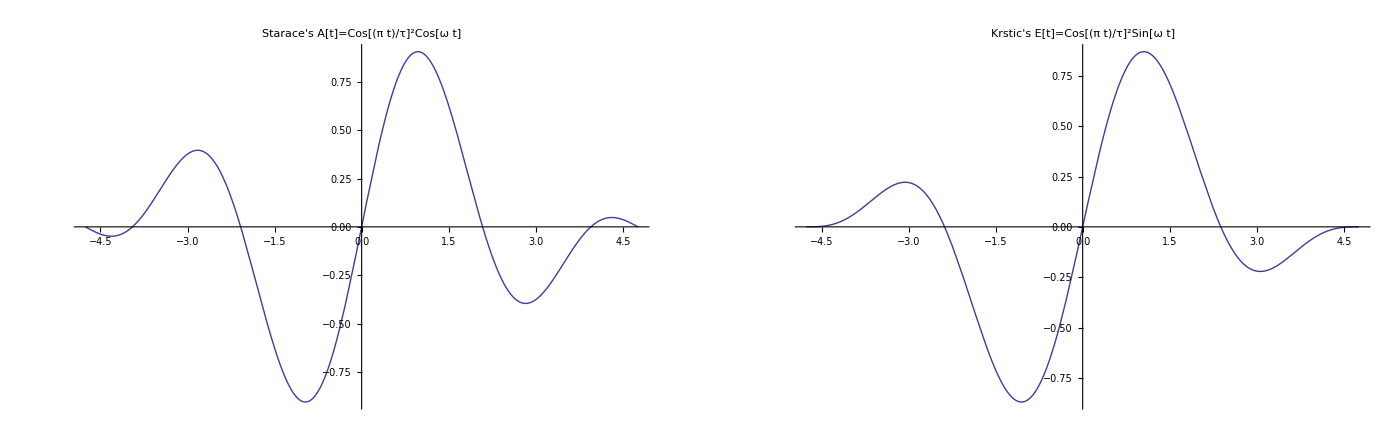

```mathematica
Module[{in=1,ω=1.32,n=2,T},
T=π n/ω;
f[t_]:=√in Cos[(t ω)/(2 n)]^2 Sin[t ω]+(√in Cos[t ω] Cos[(t ω)/(2 n)] Sin[(t ω)/(2 n)])/n;
GraphicsGrid[{{
Plot[f[t],{t,-T,T},PlotLabel->"Starace's A[t]=Cos[(π t)/τ]^2Cos[ω t]",ImageSize->300],
Plot[Cos[(t ω)/(2 n)]^2 Sin[t ω],{t,-T,T},PlotLabel->"Krstic's E[t]=Cos[(π t)/τ]^2Sin[ω t]"]
}}]
]
```

## Energy Distribution

Be sure to initialize the integration code

21

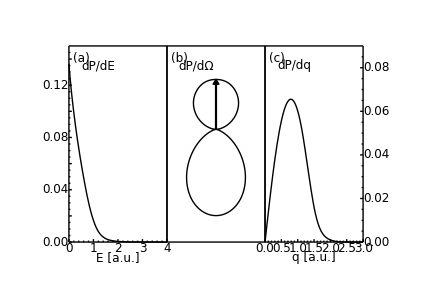

```mathematica
ionA=Import[dataDIR<>"iH2/ion.dat"];
tSTEPa=Length[First[ionA]]
hIonFIG=With[{zoom=0.012,shiftY=0.3},Figure[{
Multipanel[
{{0,1},{0,1}},
{1,3},
BufferB->3
],
(*dPdE*)
FigurePanel[{1,1},
PlotRange->{{0,4},{0,0.15}},
FrameTicks->{Automatic,LinTicks[0,0.15,TickLabelStep->2]},
LabB->"E [a.u.]"
],
ScaledLabel[{0.3,0.9},"dP/dE"],
RawGraphics[dPdE[ionA,tSTEPa,1]],
(*dPdΩ*)
FigurePanel[{1,2},
PlotRange->zoom{{-1,1},{-2-shiftY,2-shiftY}},
ShowTicks->{False,False,False,False}
],
rawGraphicsdPdΩ[ionA,tSTEPa,1],
SchemeArrow[{{0,0},{0,0.6*zoom(2-shiftY)}},ArrowType->ShapeArrow,Width->1],
ScaledLabel[{0.3,0.9},"dP/dΩ"],
(*dPdk*)
FigurePanel[{1,3},
PlotRange->{{0,3},{0,0.09}},
LabB->"q [a.u.]",
FrameTicks->{Automatic,None,None,Automatic},
ShowTickLabels->{True,False,False,True},
ShowFrameLabels->{True,False,False,True}
],
RawGraphics[dPdk[ionA,tSTEPa,1]],
ScaledLabel[{0.3,0.9},"dP/dq"]
},
PlotRange->{{-0.1,1.1},{-0.1,1.1}},ImageSize->72*2*{3,2}
]]
```

## P(E)

```mathematica
dPdEAxis[ionA_List]:=Module[{
negEnA=Cases[ionA,{0.,kz_,middle___,kLast_}:>{(27.2)kz^2, Abs[kz^2]kLast}/;kz<0],
posEnA=Cases[ionA,{0.,kz_,middle___,kLast_}:>{(27.2)kz^2,kz^2 kLast}/;kz>0],
maxY,maxX
},
maxX=Max[#[[1]]&/@negEnA];
maxY=Max[Join[#[[2]]&/@negEnA,#[[2]]&/@posEnA]];
Figure[{
FigurePanel[{{0,1},{0,1}},
PlotRange->{{0,70},{0,1.02maxY}},
FontSize->14,
FrameTicks->Automatic,
LabB->"E [eV]",BufferB->3
],
RawGraphics[ListLinePlot[{posEnA,negEnA},PlotStyle->{styleList[[1]],styleList[[2]]},PlotRange->All]],
},PlotRange->{{-0.1,1.02},{-0.15,1.02}},ImageSize->72*2{4,1.5}
]]
dPdEAxis[ionA]
```

## dP/dk_x dk_z

```mathematica
kxkzHFIG=dPdkdΩ[ionA,tSTEPa,fMAX[{ionA}]]
```

Results

```mathematica
hDIR=dataDIR<>"H05e-7/";
heDIR=dataDIR<>"He06e-7/";
liDIR=dataDIR<>"2Li03e-6/";
```

## Power Spectrum w/ Energy Levels

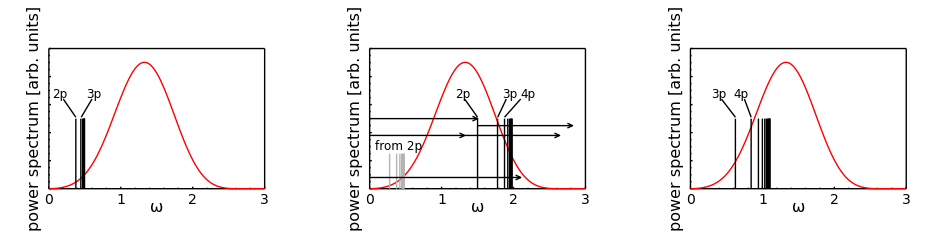

/Users/nevence/Documents/utk/first/psH.pdf

/Users/nevence/Documents/utk/first/psHe.pdf

/Users/nevence/Documents/utk/first/psLi.pdf

```mathematica
F[plotDat_List,ω_]:=With[{t=#[[1]]&/@ plotDat,f=#[[2]]&/@ plotDat},
 1/(√(2π))Sum[f[[n]] ⅇ^(-I ω t[[n]])(t[[n+1]]-t[[n]]),{n,1,Length[f]-1}]
];
abFT[plotDat_List,ωMAX_,dω_]:=Table[{ω,Abs[F[plotDat,ω]]^2},{ω,0,ωMAX,dω}]
laser[nCycle_,ω_,t_]:=
If[ω t> 0 && (ω t)/(2nCycle)<π,Sin[(ω t)/(2nCycle)]^2 Sin[ω t],0];
lDATA=With[{ω=1.32,nCycles=2},Table[{t,laser[nCycles,ω,t]},{t,0,(2π)/ω*(nCycles+1),0.1}]];
psPLOT=ListLinePlot[abFT[lDATA,3,0.02],
FrameTicks->{{0.5,1,1.5,2,2.5},None,None,None},
PlotStyle->{Red,Thickness[Large]}];


psHFIG=With[{en=0.5},Figure[{
FigurePanel[{{0,1},{0,1}},
PlotRange->{{0,3},{0,1}},
LabB->"ω",BufferB->3,
LabL->"power spectrum [arb. units]",BufferL->2,
ShowTickLabels->{True,False,False,False},
ShowFrameLabels->{True,True,False,False},
FrameTicks->{LinTicks[0,3,1.,5],Automatic},
TickNudge->{-5,0,0,0},
FontSize->16,
TickFontSize->14
],
RawGraphics[psPLOT],
ManualLabel[{0.15,0.67},"2p"],
SchemeLine[{{0.375,0.51},{0.2,0.64}}],
ManualLabel[{0.62,0.67},"3p"],
SchemeLine[{{0.45,0.51},{0.6,0.64}}],
RawGraphics[Graphics[
Table[Line[{{en(1-1/n^2),0},{en(1-1/n^2),0.5}}],{n,2,10}]
]]
},
PlotRange->{{-0.1,1.03},{-0.2,1.01}},ImageSize->72{4,3}]];
psHeFIG=With[{en=2.0,ω=1.32},Figure[{
FigurePanel[{{0,1},{0,1}},
PlotRange->{{0,3},{0,1}},
LabB->"ω",BufferB->3,
LabL->"power spectrum [arb. units]",BufferL->2,
ShowTickLabels->{True,False,False,False},
ShowFrameLabels->{True,True,False,False},
FrameTicks->{LinTicks[0,3,1.,5],Automatic},
TickNudge->{-5,0,0,0},
FontSize->16,
TickFontSize->14
],
RawGraphics[psPLOT],
ManualLabel[{1.3,0.67},"2p"],
SchemeLine[{{1.5,0.51},{1.32,0.64}}],
ManualLabel[{1.95,0.67},"3p"],
SchemeLine[{{1.78,0.51},{1.9,0.64}}],
ManualLabel[{2.2,0.67},"4p"],
SchemeLine[{{1.875,0.51},{2.1,0.64}}],
RawGraphics[Graphics[
Table[Line[{{en(1-1/n^2),0},{en(1-1/n^2),0.5}}],{n,2,10}]
]],
RawGraphics[Graphics[Join[{GrayLevel[0.7]},
Table[Line[{{en(1/2^2-1/n^2),0},{en(1/2^2-1/n^2),0.25}}],{n,3,10}]
]]],
ManualLabel[{0.4,0.3},"from 2p"],
SchemeArrow[{{0,0.5},{1.5,0.5}}],
SchemeArrow[{{1.5,0.45},{1.5+ω,0.45}}],
SchemeArrow[{{0,0.38},{ω,0.38}}],
SchemeArrow[{{ω,0.38},{2ω,0.38}}],
SchemeArrow[{{0,0.08},{2.1,0.08}}]
},
PlotRange->{{-0.1,1.03},{-0.2,1.01}},ImageSize->72{4,3}]];
psLiFIG=With[{en=4.5},Figure[{
FigurePanel[{{0,1},{0,1}},
PlotRange->{{0,3},{0,1}},
LabB->"ω",BufferB->3,
LabL->"power spectrum [arb. units]",BufferL->2,
ShowTickLabels->{True,False,False,False},
ShowFrameLabels->{True,True,False,False},
FrameTicks->{LinTicks[0,3,1.,5],Automatic},
TickNudge->{-5,0,0,0},
FontSize->16,
TickFontSize->14
],
RawGraphics[psPLOT],
ManualLabel[{0.4,0.67},"3p"],
SchemeLine[{{0.625,0.51},{0.43,0.64}}],
ManualLabel[{0.7,0.67},"4p"],
SchemeLine[{{0.844,0.51},{0.75,0.64}}],
RawGraphics[Graphics[
Table[Line[{{en(1/2^2-1/n^2),0},{en(1/2^2-1/n^2),0.5}}],{n,3,15}]
]]
},
PlotRange->{{-0.1,1.03},{-0.2,1.01}},ImageSize->72{4,3}]];
(*Clear[laser,lDATA]*)
GraphicsRow[{psHFIG,psHeFIG,psLiFIG}]
If[export,Export[exportPath<>"psH."<>suffix,psHFIG]]
If[export,Export[exportPath<>"psHe."<>suffix,psHeFIG]]
If[export,Export[exportPath<>"psLi."<>suffix,psLiFIG]]
```

## dP/dE, dP/dk, & dP/dΩ

### Linear Integration routines

```mathematica
dPdk[dat_List,fNUM_,hue_]:=Module[{
dk,dθ,dϕ=π,tol=0.00001,kMAX,sum,
points,nk,nθ,θnext,fnext,
k,θ,f,radialCS={}},
(* The task is to integrate the cross section over the angular variables taking the left right symmetries into accout.

The points on the z-axis must be handled carefully, for it needs to represent a cone, but Sin[θ] give it zero width. See journal E pg 18 for a description of the special case Jacobian.
*)
angle[x_,z_]:=If[x≥0,
If[z≠0,If[z>0,ArcTan[x/z],ArcTan[x/z]+π],π/2],
If[z≠0,If[z<0,ArcTan[x/z]+π,ArcTan[x/z]+2π],3π/2]];
xz2rθ[{x_,z_,f___}]:={√(x^2+z^2),angle[x,z],f};
(* Steps 1 & 2
Reflecting the points which don't lie on the z axis
Turning them into polar cordinates and
Sorting them in increasing r *)
points=Sort[xz2rθ/@Join[dat,Cases[dat,{x_,z_,f___}:>{-x,z,f}/;x≠0]]];
nθ=Last[First[Tally[points,Abs[#1[[1]]- #2[[1]]]<tol&]]];
(* Steps 3 & 4
Partitioning the list and then sorting each according to r *)
points2=Sort[#,#1[[2]]<#2[[2]]&]&/@Partition[points,nθ];
nk=Length[points2];
dk = points2[[2,1,1]]-points2[[1,1,1]];
dθ = points2[[1,2,2]]-points2[[1,1,2]];
(*Print["dk = ",dk,"   dθ = ",dθ,"   dϕ = ",dϕ,"   nθ = ",nθ,"   nk = ",nk];*)
(* Step 5
Integrating θ *)
For[m=1,m≤nk,m++,
sum=0;
For[n=1,n≤nθ,n++,
k=points2[[m,n,1]];
θ=points2[[m,n,2]];
θnext=If[n≠nθ,points2[[m,n+1,2]],2π];
fnext=If[n≠nθ,points2[[m,n+1,fNUM]],points2[[m,1,fNUM]]];
If[k>kMAX,kMAX=k];
(*Print[k,"  ",N[θ],"   k dθ = ",k dθ,"    π k Abs[Sin[(θ+θnext)/2]] ",π k Abs[Sin[(θ+θnext)/2]]];*)
f=points2[[m,n,fNUM]];
(*sum+=f * dk * k*dθ * k*dϕ*Abs[Sin[(θ+θnext)/2]];*)
sum+=(f+fnext)/2*k^2 Abs[Sin[(θ+θnext)/2]]dθ dϕ ;
If[n==nθ,AppendTo[radialCS,{k,sum}];
];
];
];
f=Interpolation[Prepend[radialCS,{0,0}]];
Off[Interpolation::inhr];
(* Step 6
Plotting k *)
(*Print["Total Cross Section = ",Total[#[[2]]*dk&/@radialCS]];*)
Plot[f[x],{x,0,radialCS[[-1,1]]},

(*Evaluate@Sequence[csOPTS[hue]],*)
PlotStyle->styleList[[hue]],
FrameLabel->{"momentum","dP/dk"},
FrameTicks->{None,Automatic},
RotateLabel->False
]
]



dPdE[dat_List,fNUM_,hue_]:=Module[{
dk,dθ,dϕ=π,tol=0.00001,kMAX,sum,
points,nk,nθ,θnext,fnext,
k,θ,f,radialCS={}},
(* The task is to integrate the cross section over the angular variables taking the left right symmetries into accout.

The points on the z-axis must be handled carefully, for it needs to represent a cone, but Sin[θ] give it zero width. See journal E pg 18 for a description of the special case Jacobian.
*)
angle[x_,z_]:=If[x≥0,
If[z≠0,If[z>0,ArcTan[x/z],ArcTan[x/z]+π],π/2],
If[z≠0,If[z<0,ArcTan[x/z]+π,ArcTan[x/z]+2π],3π/2]];
xz2rθ[{x_,z_,f___}]:={√(x^2+z^2),angle[x,z],f};
(* Steps 1 & 2
Reflecting the points which don't lie on the z axis
Turning them into polar cordinates and
Sorting them in increasing r *)
points=Sort[xz2rθ/@Join[dat,Cases[dat,{x_,z_,f___}:>{-x,z,f}/;x≠0]]];
nθ=Last[First[Tally[points,Abs[#1[[1]]- #2[[1]]]<tol&]]];
(* Steps 3 & 4
Partitioning the list and then sorting each according to r *)
points2=Sort[#,#1[[2]]<#2[[2]]&]&/@Partition[points,nθ];
nk=Length[points2];
dk = points2[[2,1,1]]-points2[[1,1,1]];
dθ = points2[[1,2,2]]-points2[[1,1,2]];
(*Print["dk = ",dk,"   dθ = ",dθ,"   dϕ = ",dϕ,"   nθ = ",nθ,"   nk = ",nk];*)
(* Step 5
Integrating θ *)
For[m=1,m≤nk,m++,
sum=0;
For[n=1,n≤nθ,n++,
k=points2[[m,n,1]];
θ=points2[[m,n,2]];
θnext=If[n≠nθ,points2[[m,n+1,2]],2π];
fnext=If[n≠nθ,points2[[m,n+1,fNUM]],points2[[m,1,fNUM]]];
If[k>kMAX,kMAX=k];
(*Print[k,"  ",N[θ],"   k dθ = ",k dθ,"    π k Abs[Sin[(θ+θnext)/2]] ",π k Abs[Sin[(θ+θnext)/2]]];*)
f=points2[[m,n,fNUM]];
(*sum+=f * dk * k*dθ * k*dϕ*Abs[Sin[(θ+θnext)/2]];*)
sum+=(f+fnext)/2*k Abs[Sin[(θ+θnext)/2]]dθ dϕ ;
If[n==nθ,AppendTo[radialCS,{k^2/2,sum}];
];
];
];
f=Interpolation[Prepend[radialCS,{0,radialCS[[1,2]]}]];
Off[Interpolation::inhr];
(* Step 6
Plotting k *)
(*Print["Total Cross Section = ",Total[#[[2]]*dk&/@radialCS]];*)
Plot[f[x],{x,0.0,radialCS[[-1,1]]},
PlotRange->All,
PlotStyle->styleList[[hue]]
]
]


rawGraphicsdPdΩ[dat_List,fNUM_,hue_]:=Module[{
dk,dθ,dϕ=2π,tol=0.00001,kMAX,sum,sin,pup,pdown,xMAX,yMAX,angle,xz2rθ,points,points2,i,nk,nθ,m,n,tSum=0,ylowerMAX,yupperMAX,
k,θ,θnext,f,angularCS={},debug=False},
(*The points on the z-axis must be handled carefully, for it needs to represent a cone, but Sin[θ] give it zero width. See journal E pg 18 for a description of the special case Jacobian.
*)
angle[x_,z_]:=If[x≥0,
If[z≠0,If[z>0,ArcTan[x/z],ArcTan[x/z]+π],π/2],
If[z≠0,If[z<0,-ArcTan[x/z]+π,-ArcTan[x/z]],π/2]];
xz2rθ[{x_,z_,f___}]:={√(x^2+z^2),angle[x,z],f};
(* Steps 1 & 2
Turning them into polar cordinates and
Sorting them in increasing θ *)
points=Sort[xz2rθ/@dat,#1[[2]]<#2[[2]]&];
For[i=1,i≤Length[points]-2,i++,
If[Abs[points[[i,2]]-points[[i+1,2]]]>tol,
nk=i;
Break[];
];
];

dk = Abs[points[[2,1]]-points[[1,1]]];
(* Steps 3 & 4
Partitioning the list and then sorting each according to r *)
points2=Sort/@Partition[points,nk];

nθ=Length[points2];
dθ = Abs[points2[[2,1,2]]-points2[[1,1,2]]];
sin[θ_]:=If[((Abs[θ]>tol)&&(π-Abs[θ])>tol),Sin[θ],1/2 Sin[dθ/4]];
(*Print["dk = ",dk,"   dθ = ",dθ,"   dϕ = ",dϕ,"   nθ = ",nθ,"   nk = ",nk];*)
For[m=1,m≤nθ,m++,
sum=0;
θ=points2[[m,1,2]];
(* Step 5
Integrate dk *)
For[n=1,n<nk,n++,
k=points2[[m,n,1]];
f=points2[[m,n,fNUM]];
(*θ is in the middle *)
sum+=f*k^2 dk;
tSum+=f*k^2 Sin[θ]dk dθ dϕ;
];
AppendTo[angularCS,{θ,sum}];
If[debug,Print[angularCS[[-1]]]];
];

f=Interpolation[angularCS];
Off[Interpolation::inhr];
sum=0;
For[i=1,i≤Length[angularCS],i++,
sum+= sin[angularCS[[i,1]]]dθ dϕ *angularCS[[i,2]];
];
If[debug,Print["Total Ionization Probability = ",sum]];
pup=PolarPlot[f[θ-π/2],{θ,π/2,3π/2},
PlotStyle->styleList[[hue]],
Axes->None
];
Off[InterpolatingFunction::"dmval"];
pdown=PolarPlot[f[π/2-θ],{θ,-π/2,π/2},
PlotStyle->styleList[[hue]],
FrameTicks->None,
Axes->None
];
xMAX=Max[#[[2]]*Sin[#[[1]]]&/@angularCS];
yupperMAX=Max[#[[2]]*Cos[#[[1]]]&/@angularCS];
ylowerMAX=Max[-#[[2]]*Cos[#[[1]]]&/@angularCS];
If[debug,Print["xMAX = ",xMAX]];
If[debug,Print["yupperMAX = ",yupperMAX]];
If[debug,Print["ylowerMAX = ",ylowerMAX]];
Sequence@@{RawGraphics[pdown],RawGraphics[pup]}
]
```

### Logarithmic Integration routines

```mathematica
dPdk[dat_List,fNUM_,hue_]:=Module[{
dk,dθ,dϕ=π,tol=0.00001,kMAX,sum,
points,nk,nθ,θnext,fnext,
k,θ,f,radialCS={}},
(* The task is to integrate the cross section over the angular variables taking the left right symmetries into accout.

The points on the z-axis must be handled carefully, for it needs to represent a cone, but Sin[θ] give it zero width. See journal E pg 18 for a description of the special case Jacobian.
*)
angle[x_,z_]:=If[x≥0,
If[z≠0,If[z>0,ArcTan[x/z],ArcTan[x/z]+π],π/2],
If[z≠0,If[z<0,ArcTan[x/z]+π,ArcTan[x/z]+2π],3π/2]];
xz2rθ[{x_,z_,f___}]:={√(x^2+z^2),angle[x,z],f};
(* Steps 1 & 2
Reflecting the points which don't lie on the z axis
Turning them into polar cordinates and
Sorting them in increasing r *)
points=Sort[xz2rθ/@Join[dat,Cases[dat,{x_,z_,f___}:>{-x,z,f}/;x≠0]]];
nθ=Last[First[Tally[points,Abs[#1[[1]]- #2[[1]]]<tol&]]];
(* Steps 3 & 4
Partitioning the list and then sorting each according to r *)
points2=Sort[#,#1[[2]]<#2[[2]]&]&/@Partition[points,nθ];
nk=Length[points2];
dk = points2[[2,1,1]]-points2[[1,1,1]];
dθ = points2[[1,2,2]]-points2[[1,1,2]];
(*Print["dk = ",dk,"   dθ = ",dθ,"   dϕ = ",dϕ,"   nθ = ",nθ,"   nk = ",nk];*)
(* Step 5
Integrating θ *)
For[m=1,m≤nk,m++,
sum=0;
For[n=1,n≤nθ,n++,
k=points2[[m,n,1]];
θ=points2[[m,n,2]];
θnext=If[n≠nθ,points2[[m,n+1,2]],2π];
fnext=If[n≠nθ,points2[[m,n+1,fNUM]],points2[[m,1,fNUM]]];
If[k>kMAX,kMAX=k];
(*Print[k,"  ",N[θ],"   k dθ = ",k dθ,"    π k Abs[Sin[(θ+θnext)/2]] ",π k Abs[Sin[(θ+θnext)/2]]];*)
f=points2[[m,n,fNUM]];
(*sum+=f * dk * k*dθ * k*dϕ*Abs[Sin[(θ+θnext)/2]];*)
sum+=(f+fnext)/2*k^2 Abs[Sin[(θ+θnext)/2]]dθ dϕ ;
If[n==nθ,AppendTo[radialCS,{k,sum}];
];
];
];
f=Interpolation[Prepend[radialCS,{0,0}]];
Off[Interpolation::inhr];
(* Step 6
Plotting k *)
(*Print["Total Cross Section = ",Total[#[[2]]*dk&/@radialCS]];*)
LogPlot[f[x],{x,0,radialCS[[-1,1]]},

(*Evaluate@Sequence[csOPTS[hue]],*)
PlotStyle->styleList[[hue]],
FrameLabel->{"momentum","dP/dk"},
FrameTicks->{None,Automatic},
RotateLabel->False
]
]


rawGraphicsdPdΩ[dat_List,fNUM_,hue_]:=Module[{
dk,dθ,dϕ=2π,tol=0.00001,kMAX,sum,sin,pup,pdown,xMAX,yMAX,angle,xz2rθ,points,points2,i,nk,nθ,m,n,tSum=0,ylowerMAX,yupperMAX,
k,θ,θnext,f,angularCS={}},
(*The points on the z-axis must be handled carefully, for it needs to represent a cone, but Sin[θ] give it zero width. See journal E pg 18 for a description of the special case Jacobian.
*)
angle[x_,z_]:=If[x≥0,
If[z≠0,If[z>0,ArcTan[x/z],ArcTan[x/z]+π],π/2],
If[z≠0,If[z<0,-ArcTan[x/z]+π,-ArcTan[x/z]],π/2]];
xz2rθ[{x_,z_,f___}]:={√(x^2+z^2),angle[x,z],f};
(* Steps 1 & 2
Turning them into polar cordinates and
Sorting them in increasing θ *)
points=Sort[xz2rθ/@dat,#1[[2]]<#2[[2]]&];
For[i=1,i≤Length[points]-2,i++,
If[Abs[points[[i,2]]-points[[i+1,2]]]>tol,
nk=i;
Break[];
];
];

dk = Abs[points[[2,1]]-points[[1,1]]];
(* Steps 3 & 4
Partitioning the list and then sorting each according to r *)
points2=Sort/@Partition[points,nk];

nθ=Length[points2];
dθ = Abs[points2[[2,1,2]]-points2[[1,1,2]]];
sin[θ_]:=If[((Abs[θ]>tol)&&(π-Abs[θ])>tol),Sin[θ],1/2 Sin[dθ/4]];
(*Print["dk = ",dk,"   dθ = ",dθ,"   dϕ = ",dϕ,"   nθ = ",nθ,"   nk = ",nk];*)
For[m=1,m≤nθ,m++,
sum=0;
θ=points2[[m,1,2]];
(* Step 5
Integrate dk *)
For[n=1,n<nk,n++,
k=points2[[m,n,1]];
f=points2[[m,n,fNUM]];
(*θ is in the middle *)
sum+=f*k^2 dk;
tSum+=f*k^2 Sin[θ]dk dθ dϕ;
];
AppendTo[angularCS,{θ,sum}];
];

f=Interpolation[angularCS];
Off[Interpolation::inhr];
sum=0;
For[i=1,i≤Length[angularCS],i++,
sum+= sin[angularCS[[i,1]]]dθ dϕ *angularCS[[i,2]];
];
Print["Total Ionization Probability = ",sum];
pup=PolarPlot[f[θ-π/2],{θ,π/2,3π/2},
PlotStyle->styleList[[hue]],
Axes->None
];
Off[InterpolatingFunction::"dmval"];
pdown=PolarPlot[f[π/2-θ],{θ,-π/2,π/2},
PlotStyle->styleList[[hue]],
FrameTicks->None,
Axes->None
];
xMAX=Max[#[[2]]*Sin[#[[1]]]&/@angularCS];
yupperMAX=Max[#[[2]]*Cos[#[[1]]]&/@angularCS];
ylowerMAX=Max[-#[[2]]*Cos[#[[1]]]&/@angularCS];
Print["xMAX = ",xMAX];
Print["yupperMAX = ",yupperMAX];
Print["ylowerMAX = ",ylowerMAX];
Sequence@@{RawGraphics[pdown],RawGraphics[pup]}
]


rawGraphicsdPdE[dat_List,fNUM_,hue_,atom_,yLo_,yHi_,lines_List]:=Module[{
dk,dθ,dϕ=π,tol=0.00001,kMAX,sum,
points,nk,nθ,θnext,fnext,
k,θ,f,radialCS={}},
(* The task is to integrate the cross section over the angular variables taking the left right symmetries into accout.

The points on the z-axis must be handled carefully, for it needs to represent a cone, but Sin[θ] give it zero width. See journal E pg 18 for a description of the special case Jacobian.
*)
angle[x_,z_]:=If[x≥0,
If[z≠0,If[z>0,ArcTan[x/z],ArcTan[x/z]+π],π/2],
If[z≠0,If[z<0,ArcTan[x/z]+π,ArcTan[x/z]+2π],3π/2]];
xz2rθ[{x_,z_,f___}]:={√(x^2+z^2),angle[x,z],f};
(* Steps 1 & 2
Reflecting the points which don't lie on the z axis
Turning them into polar cordinates and
Sorting them in increasing r *)
points=Sort[xz2rθ/@Join[dat,Cases[dat,{x_,z_,f___}:>{-x,z,f}/;x≠0]]];
nθ=Last[First[Tally[points,Abs[#1[[1]]- #2[[1]]]<tol&]]];
(* Steps 3 & 4
Partitioning the list and then sorting each according to r *)
points2=Sort[#,#1[[2]]<#2[[2]]&]&/@Partition[points,nθ];
nk=Length[points2];
dk = points2[[2,1,1]]-points2[[1,1,1]];
dθ = points2[[1,2,2]]-points2[[1,1,2]];
(*Print["dk = ",dk,"   dθ = ",dθ,"   dϕ = ",dϕ,"   nθ = ",nθ,"   nk = ",nk];*)
(* Step 5
Integrating θ *)
For[m=1,m≤nk,m++,
sum=0;
For[n=1,n≤nθ,n++,
k=points2[[m,n,1]];
θ=points2[[m,n,2]];
θnext=If[n≠nθ,points2[[m,n+1,2]],2π];
fnext=If[n≠nθ,points2[[m,n+1,fNUM]],points2[[m,1,fNUM]]];
If[k>kMAX,kMAX=k];
(*Print[k,"  ",N[θ],"   k dθ = ",k dθ,"    π k Abs[Sin[(θ+θnext)/2]] ",π k Abs[Sin[(θ+θnext)/2]]];*)
f=points2[[m,n,fNUM]];
(*sum+=f * dk * k*dθ * k*dϕ*Abs[Sin[(θ+θnext)/2]];*)
sum+=(f+fnext)/2*k Abs[Sin[(θ+θnext)/2]]dθ dϕ ;
If[n==nθ,AppendTo[radialCS,{k^2/2,sum}];
];
];
];
f=Interpolation[Prepend[radialCS,{0,radialCS[[1,2]]}]];
Off[Interpolation::inhr];
(* Step 6
Plotting k *)
(*Print["Total Cross Section = ",Total[#[[2]]*dk&/@radialCS]];*)
Sequence@@{
FigurePanel[{1,1},
FrameTicks->{LinTicks[0,5,1,5],LogTicks[yLo,yHi-1,TickLabelStep->2]},
PanelAdjustments->{{0,0},{0.5,0}},
PanelLetter->"(b)",
PlotRange->{{0,radialCS[[-1,1]]},{yLo,yHi}}
],
RawGraphics[Plot[Log[10,f[x]],{x,0.1,radialCS[[-1,1]]},
PlotStyle->styleList[[hue]]
]],
ScaledLabel[{0.3,0.867},"dP/dE_f"],
ScaledLabel[{0.8,0.9},atom],
SetOptions[SchemeLine,Dashing->Automatic],
Sequence@@Table[SchemeLine[lines[[i]]],{i,1,Length[lines]}],
(*Derivative*)
FigurePanel[{2,1},
FrameTicks->{LinTicks[0,5,1,5],None},
PanelAdjustments->{{0,0},{0,-0.5}},
PanelLetter->"(e)",
LabB->"E_f",BufferB->3,
PlotRange->{{0,radialCS[[-1,1]]},{-4,1}}(*,
LabL[{0.3,0.3},"∂/(∂E)(dP/dE)"],BufferL->3,
LabB->"electron energy [a.u.]", BufferB->3
*)
],
RawGraphics[Plot[Evaluate[D[Log[10,f[x]],x]],{x,0.1,radialCS[[-1,1]]},
PlotStyle->styleList[[hue]]
]]
}
]
```

### Angular coefficients

#### Basics

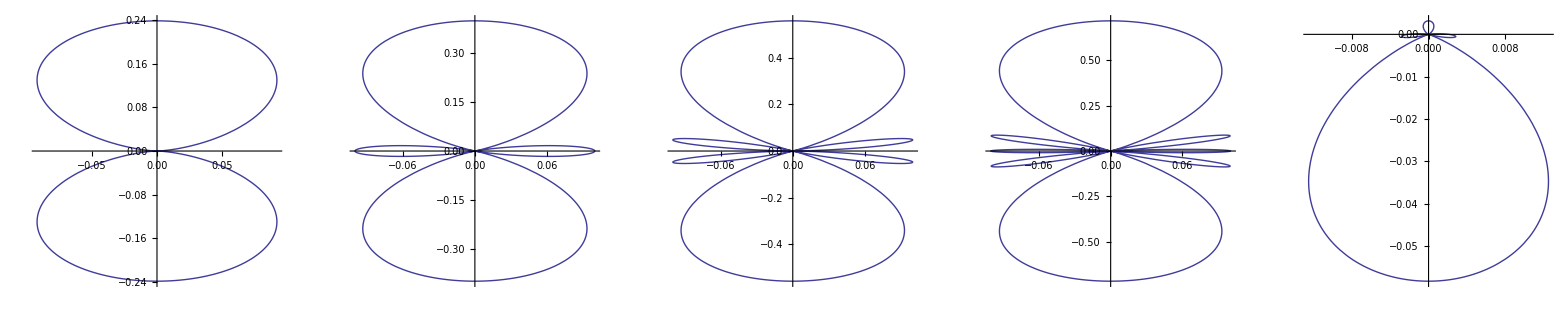

```mathematica
Y00[θ_]:=SphericalHarmonicY[0,0,θ+π/2,0];
Y10[θ_]:=SphericalHarmonicY[1,0,θ+π/2,0];
Y20[θ_]:=SphericalHarmonicY[2,0,θ+π/2,0];
Y30[θ_]:=SphericalHarmonicY[3,0,θ+π/2,0];
Y40[θ_]:=SphericalHarmonicY[4,0,θ+π/2,0];
s2=14;
p2=520 ;
d2=356;
f2=0.4;
n1=√(s2+p2+d2+f2);
s1=√s2/n1;
p1=√p2/n1;
d1=√d2/n1;
f1=√f2/n1;
GraphicsGrid[{{
PolarPlot[Y10[θ]^2,{θ,0,2π}],
PolarPlot[Y20[θ]^2,{θ,0,2π}],
PolarPlot[Y30[θ]^2,{θ,0,2π}],
PolarPlot[Y40[θ]^2,{θ,0,2π}],
PolarPlot[Abs[s1*Y20[θ]+p1*Y10[θ]d1*Y20[θ]+f1*Y20[θ]]^2,{θ,0,2π}]}}]
Animate[PolarPlot[
s1*Y00[θ]+
s1*d1*Y00[θ]*Y10[θ]+
s1*d1*Y00[θ]*Y20[θ]+
p1^2*Y10[θ]^2+
d1^2*Y20[θ]^2 +
2p1*d1*Cos[ϕ]Y10[θ]Y20[θ],{θ,0,2π}]
,{ϕ,0,π/2,π/100}];
```

#### Differential and Calculated

```mathematica
ionB=Import[dataDIR<>"He05/ion.dat"];
tSTEPb=Length[First[ionB]];
heIonFIG=With[{zoom=0.00025,shiftX=-0.2,shiftY=0.0},Figure[{
Multipanel[
{{0,1},{0,1}},
{1,3},
BufferB->3,
TickNudge->{-4,{-3,0},0,{3,0}},
TickFontSize->15,
FontSize->16
],
(*dPdE*)
FigurePanel[{1,1},
PlotRange->{{0,4.5},{-12,-5.8}},
FrameTicks->{Automatic,LogTicks[-12,-6,TickLabelStep->2]},
LabB->"E [a.u.]"
],
ScaledLabel[{0.3,0.9},"dP/dE_q"],
RawGraphics[dPdE[ionB,tSTEPb,1]],

(*dPdΩ*)
FigurePanel[{1,2},
PlotRange->zoom{{-1-shiftX,1-shiftX},{-2-shiftY,2-shiftY}},
ShowTicks->{False,False,False,False}
],
rawGraphicsdPdΩ[ionB,tSTEPb,1],
SchemeArrow[{{0,0},{0,0.6*zoom(2-shiftY)}},ArrowType->ShapeArrow,Width->1],
ScaledLabel[{0.3,0.9},"dP/dΩ"],
ScaledFigurePanel[{{0.55,0.95},{0.6,0.975}},
PlotRange->{{-0.2,0.2},{-0.6,0.15}}],
RawGraphics[PolarPlot[p1^2*Y10[θ]^2+d1^2*Y20[θ]^2 +2p1*d1*Cos[1.2π/4]Y10[θ]Y20[θ],{θ,0,2π}]],

(*dPdk*)
FigurePanel[{1,3},
PlotRange->{{0,3},{-12,-6}},
LabB->"q [a.u.]",
FrameTicks->{LinTicks[0,3,1.0,4],None,None,LogTicks[-12,-6,TickLabelStep->2]},
ShowTickLabels->{True,False,False,True},
ShowFrameLabels->{True,False,False,True}
],
RawGraphics[dPdk[ionB,tSTEPb,1]],
ScaledLabel[{0.3,0.9},"dP/dq"]
},
PlotRange->{{-0.1,1.1},{-0.14,1.1}},ImageSize->72*2*{3,2}
]]

If[export,Export[exportPath<>"heIon."<>suffix,heIonFIG]]
```

#### Calculated Phase

```mathematica
ionB=Import[dataDIR<>"He05/ion.dat"];
tSTEPb=Length[First[ionB]];
heIonPhaseFIG=With[{zoom=0.25,shiftX=0,shiftY=0.6},Figure[{
Multipanel[
{{0,1},{0,1}},
{1,3},
BufferB->3,
TickNudge->{-4,{-3,0},0,{3,0}},
TickFontSize->15,
FontSize->16
],
(*dPdE*)
FigurePanel[{1,1},
PlotRange->zoom{{-1-shiftX,1-shiftX},{-2-shiftY,2-shiftY}},
ShowTicks->{False,False,False,False}
],
ScaledLabel[{0.2,0.85},"ϕ = 0"],
RawGraphics[PolarPlot[p1^2*Y10[θ]^2+d1^2*Y20[θ]^2 +2p1*d1*Cos[0]Y10[θ]Y20[θ],{θ,0,2π}]],
(*dPdΩ*)
FigurePanel[{1,2},
PlotRange->zoom{{-1-shiftX,1-shiftX},{-2-shiftY,2-shiftY}},
ShowTicks->{False,False,False,False}
],
SchemeArrow[{{0,0},{0,0.6*zoom(2-shiftY)}},ArrowType->ShapeArrow,Width->1],
ScaledLabel[{0.2,0.85},"ϕ = 0.9"],
RawGraphics[PolarPlot[p1^2*Y10[θ]^2+d1^2*Y20[θ]^2 +2p1*d1*Cos[1.2π/4]Y10[θ]Y20[θ],{θ,0,2π}]],

(*dPdk*)
FigurePanel[{1,3},
PlotRange->zoom{{-1-shiftX,1-shiftX},{-2-shiftY,2-shiftY}},
ShowTicks->{False,False,False,False}
],
RawGraphics[PolarPlot[p1^2*Y10[θ]^2+d1^2*Y20[θ]^2 +2p1*d1*Cos[π/2]Y10[θ]Y20[θ],{θ,0,2π}]],
ScaledLabel[{0.2,0.85},"ϕ = π/2"]
},
PlotRange->{{-0.1,1.1},{-0.14,1.1}},ImageSize->72*2*{3,2}
]]
If[export,Export[exportPath<>"heIonPhase."<>suffix,heIonPhaseFIG]]
```

### dP/dE Inflection Points

#### routine

```mathematica
inflectdPdE[dat_List,fNUM_,hue_]:=Module[{
dk,dθ,dϕ=π,tol=0.00001,kMAX,sum,
points,nk,nθ,θnext,fnext,
k,θ,f,radialCS={}},
(* The task is to integrate the cross section over the angular variables taking the left right symmetries into accout.

The points on the z-axis must be handled carefully, for it needs to represent a cone, but Sin[θ] give it zero width. See journal E pg 18 for a description of the special case Jacobian.
*)
angle[x_,z_]:=If[x≥0,
If[z≠0,If[z>0,ArcTan[x/z],ArcTan[x/z]+π],π/2],
If[z≠0,If[z<0,ArcTan[x/z]+π,ArcTan[x/z]+2π],3π/2]];
xz2rθ[{x_,z_,f___}]:={√(x^2+z^2),angle[x,z],f};
(* Steps 1 & 2
Reflecting the points which don't lie on the z axis
Turning them into polar cordinates and
Sorting them in increasing r *)
points=Sort[xz2rθ/@Join[dat,Cases[dat,{x_,z_,f___}:>{-x,z,f}/;x≠0]]];
nθ=Last[First[Tally[points,Abs[#1[[1]]- #2[[1]]]<tol&]]];
(* Steps 3 & 4
Partitioning the list and then sorting each according to r *)
points2=Sort[#,#1[[2]]<#2[[2]]&]&/@Partition[points,nθ];
nk=Length[points2];
dk = points2[[2,1,1]]-points2[[1,1,1]];
dθ = points2[[1,2,2]]-points2[[1,1,2]];
(*Print["dk = ",dk,"   dθ = ",dθ,"   dϕ = ",dϕ,"   nθ = ",nθ,"   nk = ",nk];*)
(* Step 5
Integrating θ *)
For[m=1,m≤nk,m++,
sum=0;
For[n=1,n≤nθ,n++,
k=points2[[m,n,1]];
θ=points2[[m,n,2]];
θnext=If[n≠nθ,points2[[m,n+1,2]],2π];
fnext=If[n≠nθ,points2[[m,n+1,fNUM]],points2[[m,1,fNUM]]];
If[k>kMAX,kMAX=k];
(*Print[k,"  ",N[θ],"   k dθ = ",k dθ,"    π k Abs[Sin[(θ+θnext)/2]] ",π k Abs[Sin[(θ+θnext)/2]]];*)
f=points2[[m,n,fNUM]];
(*sum+=f * dk * k*dθ * k*dϕ*Abs[Sin[(θ+θnext)/2]];*)
sum+=(f+fnext)/2*k Abs[Sin[(θ+θnext)/2]]dθ dϕ ;
If[n==nθ,AppendTo[radialCS,{k^2/2,sum}];
];
];
];
f=Interpolation[Prepend[radialCS,{0,radialCS[[1,2]]}]];
Off[Interpolation::inhr];
(* Step 6
Plotting k *)
(*Print["Total Cross Section = ",Total[#[[2]]*dk&/@radialCS]];*)
Figure[{
Multipanel[
{{0,1},{0,1}},
{2,1}],
FigurePanel[{1,1},
FrameTicks->{Automatic,LogTicks[-8,-1,TickLabelStep->2]},
PlotRange->{{0,radialCS[[-1,1]]},{-8,-1}}],
RawGraphics[Plot[Log[10,f[x]],{x,0.1,radialCS[[-1,1]]},
PlotStyle->styleList[[hue]]
]],
ScaledLabel[{0.9,0.7},"dP/dE"],
FigurePanel[{2,1},
PlotRange->{{0,radialCS[[-1,1]]},{-4,3}}],
SchemeLine[{{0,0},{radialCS[[-1,1]],0}}],
RawGraphics[Plot[Evaluate[D[Log[10,f[x]],x]],{x,0.1,radialCS[[-1,1]]},
PlotStyle->styleList[[hue]]
]],
ScaledLabel[{0.9,0.7},"∂^2/∂^2"]
},PlotRange->{{-0.1,1.1},{-0.1,1.1}},ImageSize->72*2{4,3}
]
]
```

#### graphs

```mathematica
ionA=Import[dataDIR<>"H05e-7/ion.dat"];
tSTEPa=Length[First[ionA]];
inflectdPdE[ionA,tSTEPa,1]
```

```mathematica
ionB=Import[dataDIR<>"He06e-7/ion.dat"];
tSTEPb=Length[First[ionB]];
inflectdPdE[ionB,tSTEPb,1]
```

```mathematica
ionC=Import[dataDIR<>"2Li03b/ion.dat"];
tSTEPc=Length[First[ionC]];
inflectdPdE[ionC,tSTEPc,1]
```

### Linear Figures

#### H

```mathematica
ionA=Import[dataDIR<>"H1/ion.dat"];
tSTEPa=Length[First[ionA]];
hIonFIG=With[{zoom=0.0025,shiftY=0},Figure[{
Multipanel[
{{0,1},{0,1}},
{1,3},
BufferB->3
],
(*dPdE*)
FigurePanel[{1,1},
PlotRange->{{0,4},{0,0.035}},
FrameTicks->{Automatic,LinTicks[0,0.035,TickLabelStep->2]},
LabB->"E [a.u.]"
],
ScaledLabel[{0.3,0.9},"dP/dE"],
RawGraphics[dPdE[ionA,tSTEPa,1]],
(*dPdΩ*)
FigurePanel[{1,2},
PlotRange->zoom{{-1,1},{-2-shiftY,2-shiftY}},
ShowTicks->{False,False,False,False}
],
rawGraphicsdPdΩ[ionA,tSTEPa,1],
SchemeArrow[{{0,0},{0,0.6*zoom(2-shiftY)}},ArrowType->ShapeArrow,Width->1],
ScaledLabel[{0.3,0.9},"dP/dΩ"],
(*dPdk*)
FigurePanel[{1,3},
PlotRange->{{0,3},{0,0.02}},
LabB->"q [a.u.]",
FrameTicks->{Automatic,None,None,LinTicks[0,0.015,0.005,2]},
ShowTickLabels->{True,False,False,True},
ShowFrameLabels->{True,False,False,True}
],
RawGraphics[dPdk[ionA,tSTEPa,1]],
ScaledLabel[{0.3,0.9},"dP/dq"]
},
PlotRange->{{-0.1,1.1},{-0.1,1.1}},ImageSize->72*2*{3,2}
]]

If[export,Export[exportPath<>"hIon."<>suffix,hIonFIG]]
```

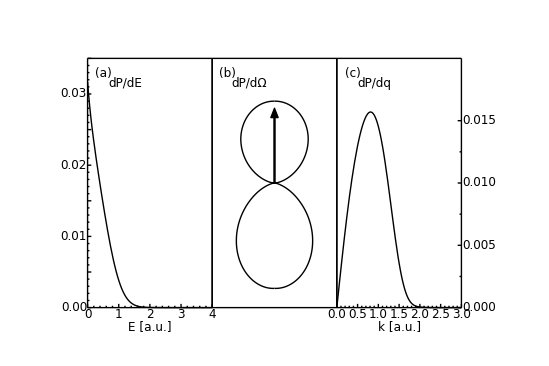

#### He

```mathematica
ionB=Import[dataDIR<>"He05/ion.dat"];
tSTEPb=Length[First[ionB]];
heIonFIG=With[{zoom=0.00025,shiftX=-0.2,shiftY=0.0},Figure[{
Multipanel[
{{0,1},{0,1}},
{1,3},
BufferB->3
],
(*dPdE*)
FigurePanel[{1,1},
PlotRange->{{0,2},{0,0.004}},
FrameTicks->{Automatic,LinTicks[0,0.004]},
LabB->"E [a.u.]"
],
ScaledLabel[{0.3,0.9},"dP/dE"],
RawGraphics[dPdE[ionB,tSTEPb,1]],

(*dPdΩ*)
FigurePanel[{1,2},
PlotRange->zoom{{-1-shiftX,1-shiftX},{-2-shiftY,2-shiftY}},
ShowTicks->{False,False,False,False}
],
rawGraphicsdPdΩ[ionB,tSTEPb,1],
SchemeArrow[{{0,0},{0,0.6*zoom(2-shiftY)}},ArrowType->ShapeArrow,Width->1],
ScaledLabel[{0.3,0.9},"dP/dΩ"],
ScaledFigurePanel[{{0.55,0.95},{0.6,0.975}},
PlotRange->{{-0.2,0.2},{-0.6,0.05}}],
RawGraphics[PolarPlot[0*s1*Y00[θ]+p1*Y10[θ]+d1^2*Y20[θ]^2+0*f1^2*Y30[θ]^2,{θ,0,2π}]],

(*dPdk*)
FigurePanel[{1,3},
PlotRange->{{0,2},{0,0.0015}},
LabB->"q [a.u.]",
FrameTicks->{Automatic,None,None,LinTicks[0,0.001]},
ShowTickLabels->{True,False,False,True},
ShowFrameLabels->{True,False,False,True}
],
RawGraphics[dPdk[ionB,tSTEPb,1]],
ScaledLabel[{0.3,0.9},"dP/dq"]
},
PlotRange->{{-0.15,1.1},{-0.1,1.1}},ImageSize->72*2*{3,2}
]]

If[export,Export[exportPath<>"heIon."<>suffix,heIonFIG]]
```

#### Li

```mathematica
ionC=Import[dataDIR<>"2Li1/ion.dat"];
tSTEPc=Length[First[ionC]];
liIonFIG=With[{zoom=0.002,shiftY=0.4},Figure[{
Multipanel[
{{0,1},{0,1}},
{1,3},
BufferB->3
],
(*dPdE*)
FigurePanel[{1,1},
PlotRange->{{0,2},{0,0.03}},
FrameTicks->{Automatic,LinTicks[0,0.03,0.01,2]},
LabB->"E [a.u.]"
],
ScaledLabel[{0.3,0.9},"dP/dE"],
RawGraphics[dPdE[ionC,tSTEPc,1]],
(*dPdΩ*)
FigurePanel[{1,2},
PlotRange->zoom{{-1,1},{-2-shiftY,2-shiftY}},
ShowTicks->{False,False,False,False}
],
rawGraphicsdPdΩ[ionC,tSTEPc,1],
SchemeArrow[{{0,0},{0,0.6*zoom(2-shiftY)}},ArrowType->ShapeArrow,Width->1],
ScaledLabel[{0.3,0.9},"dP/dΩ"],
(*dPdk*)
FigurePanel[{1,3},
PlotRange->{{0,2},{0,0.015}},
LabB->"q [a.u.]",
FrameTicks->{Automatic,None,None,LinTicks[0,0.013,0.005,2]},
ShowTickLabels->{True,False,False,True},
ShowFrameLabels->{True,False,False,True}
],
RawGraphics[dPdk[ionC,tSTEPc,1]],
ScaledLabel[{0.3,0.9},"dP/dq"]
},
PlotRange->{{-0.1,1.1},{-0.1,1.1}},ImageSize->72*2*{3,2}
]]

If[export,Export[exportPath<>"liIon."<>suffix,liIonFIG]]
```

RawGraphics::lsargs: Missing or unexpected arguments in level scheme object RawGraphics[dPdE[{{0., 0.05, 3.55944×10^-9, 9.01908×10^-7, 0.0000198198, 0.000141536, 0.000505338, 0.00106554, 0.0013983, 0.00126528, 0.00185434, 0.00603523, « 20 », 0.103483, 0.10348, 0.10351, 0.10355, 0.103585, 0.103632, 0.103711, 0.103797, 0.103853, 0.103888, 0.103929, 0.10396}, « 49 », « 610 »}, 44, 1]].

/Users/nevence/Documents/utk/first/liIon.pdf

### Logarithmic Figures

#### H

Total Ionization Probability = 0.0159555

xMAX = 0.00155345

yupperMAX = 0.00333466

ylowerMAX = 0.00430131

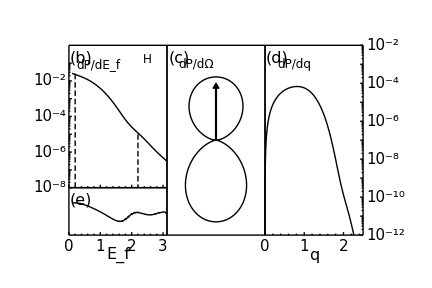

/Users/nevence/Documents/utk/first/hIon.pdf

```mathematica
ionDAT=Import[dataDIR<>"H05e-7/ion.dat"];
tSTEP=Length[First[ionDAT]];
hIonFIG=With[{zoom=0.0025,shiftY=0},Figure[{
Multipanel[
{{0,1},{0,1}},
{2,3},
BufferB->3,
TickNudge->{-4,{-3,0},0,{3,0}},
TickFontSize->15,
FontSize->16
],
(*dPdE*)
rawGraphicsdPdE[ionDAT,tSTEP,1,"H",
-8,0,(*yRange*)
{
{{0.2,-1.6},{0.2,-8}},
{{2.2,-5.0},{2.2,-8}}
}],
(*dPdΩ*)
FigurePanel[{1,2},
PanelAdjustments->{{0,0},{1,0}},
PanelLetter->"(c)",
PlotRange->zoom{{-1,1},{-2-shiftY,2-shiftY}},
ShowTicks->{False,False,False,False}
],
rawGraphicsdPdΩ[ionDAT,tSTEP,1],
SchemeArrow[{{0,0},{0,0.6*zoom(2-shiftY)}},ArrowType->ShapeArrow,Width->1],
ScaledLabel[{0.3,0.9},"dP/dΩ"],
(*dPdk*)
FigurePanel[{1,3},
PanelAdjustments->{{0,0},{1,0}},
PanelLetter->"(d)",
PlotRange->{{0,2.5},{-12,-2}},
LabB->"q",
FrameTicks->{LinTicks[0,3,1.,5],None,None,LogTicks[-14,-2,TickLabelStep->2]},
ShowTickLabels->{True,False,False,True},
ShowFrameLabels->{True,False,False,True}
],
RawGraphics[dPdk[ionDAT,tSTEP,1]],
ScaledLabel[{0.3,0.9},"dP/dq"]
},
PlotRange->{{-0.1,1.1},{-0.14,1.1}},ImageSize->72*2*{3,2}
]]
If[export,Export[exportPath<>"hIon."<>suffix,hIonFIG]]
```

#### He

```mathematica
ionDAT=Import[dataDIR<>"He05/ion.dat"];
tSTEP=Length[First[ionDAT]];
heIonFIG=With[{zoom=0.00025,shiftY=0.5},Figure[{
Multipanel[
{{0,1},{0,1}},
{2,3},
BufferB->3,
TickNudge->{-4,{-3,0},0,{3,0}},
TickFontSize->15,
FontSize->16
],
(*dPdE*)
rawGraphicsdPdE[ionDAT,tSTEP,1,"He^+",
-8,0,(*yRange*)
{
{{0.6,-3.55},{0.6,-8}},
{{2.68,-7.4},{2.68,-8}}
}],
(*dPdΩ*)
FigurePanel[{1,2},
PanelAdjustments->{{0,0},{1,0}},
PlotRange->zoom{{-1,1},{-2-shiftY,2-shiftY}},
PanelLetter->"(c)",
ShowTicks->{False,False,False,False}
],
rawGraphicsdPdΩ[ionDAT,tSTEP,1],
SchemeArrow[{{0,0},{0,0.6*zoom(2-shiftY)}},ArrowType->ShapeArrow,Width->1],
ScaledLabel[{0.3,0.9},"dP/dΩ"],
(*dPdk*)
FigurePanel[{1,3},
PanelAdjustments->{{0,0},{1,0}},
PlotRange->{{0,2.5},{-12,-2}},
PanelLetter->"(d)",
LabB->"q",
FrameTicks->{LinTicks[0,3,1.,5],None,None,LogTicks[-14,-2,TickLabelStep->2]},
ShowTickLabels->{True,False,False,True},
ShowFrameLabels->{True,False,False,True}
],
RawGraphics[dPdk[ionDAT,tSTEP,1]],
ScaledLabel[{0.3,0.9},"dP/dq"]
},
PlotRange->{{-0.1,1.1},{-0.14,1.1}},ImageSize->72*2*{3,2}
]]
If[export,Export[exportPath<>"heIon."<>suffix,heIonFIG]]
```

#### Li

Total Ionization Probability = 0.0105285

xMAX = 0.00125294

yupperMAX = 0.00140601

ylowerMAX = 0.00392755

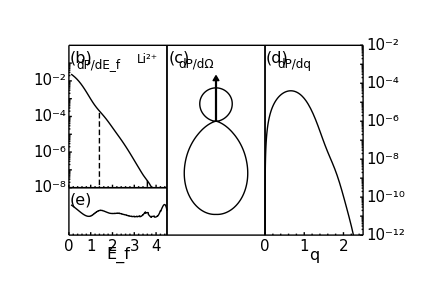

/Users/nevence/Documents/utk/first/liIon.pdf

```mathematica
ionDAT=Import[dataDIR<>"2Li1/ion.dat"];
tSTEP=Length[First[ionDAT]];
liIonFIG=With[{zoom=0.002,shiftY=0.4},Figure[{
Multipanel[
{{0,1},{0,1}},
{2,3},
BufferB->3,
TickNudge->{-4,{-3,0},0,{3,0}},
TickFontSize->15,
FontSize->16
],
(*dPdE*)
rawGraphicsdPdE[ionDAT,tSTEP,1,"Li^(2+)",
-8,0,(*yRange*)
{
{{1.4,-3.8},{1.4,-8}},
{{3.6,-7.6},{3.6,-8}}
}],
(*dPdΩ*)
FigurePanel[{1,2},
PanelAdjustments->{{0,0},{1,0}},
PlotRange->zoom{{-1,1},{-2-shiftY,2-shiftY}},
PanelLetter->"(c)",
ShowTicks->{False,False,False,False}
],
rawGraphicsdPdΩ[ionDAT,tSTEP,1],
SchemeArrow[{{0,0},{0,0.6*zoom(2-shiftY)}},ArrowType->ShapeArrow,Width->1],
ScaledLabel[{0.3,0.9},"dP/dΩ"],
(*dPdk*)
FigurePanel[{1,3},
PanelAdjustments->{{0,0},{1,0}},
PlotRange->{{0,2.5},{-12,-2}},
PanelLetter->"(d)",
LabB->"q",
FrameTicks->{LinTicks[0,3,1.,5],None,None,LogTicks[-14,-2,TickLabelStep->2]},
ShowTickLabels->{True,False,False,True},
ShowFrameLabels->{True,False,False,True}
],
RawGraphics[dPdk[ionDAT,tSTEP,1]],
ScaledLabel[{0.3,0.9},"dP/dq"]
},
PlotRange->{{-0.1,1.1},{-0.14,1.1}},ImageSize->72*2*{3,2}
]]
If[export,Export[exportPath<>"liIon."<>suffix,liIonFIG]]
```

## dP/dk_x dk_z

```mathematica
(*Finds the max of a list of 2D lists*)
fMAX[dat_]:=With[{fNUM=Length[First[dat]]},
maxList={};
For[i=1,i≤Length[dat],i++,
For[j=3,j≤Length[dat[[i]]],j++,
kx=dat[[i,j,1]];
kz=dat[[i,j,2]];
thisMax=Max[(kx^2+kz^2)#&/@dat[[i,j,3;;]] ];
AppendTo[maxList,thisMax];
];
];
Max[maxList]
]
(*3D plot of the electron's ionization*)
dPdkdΩ[dat_,fNUM_,fMAX_,opts___]:=Show[{ListPlot3D[{#[[1]],#[[2]],((#[[1]])^2+(#[[2]])^2)*#[[fNUM]]}&/@dat,ViewPoint->{10,0,1},PlotRange->{0,fMAX},opts],
Graphics3D[{Thick,Arrowheads[{-0.08,0.08}],Arrow[{{2.5,-2,fMAX},{2.5,2,fMAX}}]
}]}];
ionA=Import[hDIR<>"ion.dat"];
ionB=Import[heDIR<>"ion.dat"];
ionC=Import[liDIR<>"ion.dat"];
ionD=Import[dataDIR<>"2Li1/ion.dat"];
tSTEPa=Length[First[ionA]];
tSTEPb=Length[First[ionB]];
tSTEPc=Length[First[ionC]];
tSTEPd=Length[First[ionD]];
ionDAT={ionA,ionB,ionC,ionD};
fMAXn=fMAX[ionDAT];

kxkzHFIG=dPdkdΩ[ionA,tSTEPa,fMAX[{ionA}]]
kxkzHeFIG=dPdkdΩ[ionB,tSTEPb,fMAX[{ionB}]]
kxkzLiFIG=dPdkdΩ[ionC,tSTEPc,fMAX[{ionC}]]
kxkzLiFIG=dPdkdΩ[ionD,tSTEPd,fMAX[{ionD}]]
suffixTMP="jpg";
imgSIZE=2400;
exportTHIS=False;
If[exportTHIS,Export[exportPath<>"kxkzH."<>suffixTMP,kxkzHFIG,ImageSize->imgSIZE]]
If[exportTHIS,Export[exportPath<>"kxkzHe."<>suffixTMP,kxkzHeFIG,ImageSize->imgSIZE]]
If[exportTHIS,Export[exportPath<>"kxkzLi."<>suffixTMP,kxkzLiFIG,ImageSize->imgSIZE]]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

## Excitation

### Total Ionization

```mathematica
ionA=Import[hDIR];
ionB=Import[heDIR];
ionC=Import[liDIR];
tSTEPa=Length[First[ionA]];
tSTEPb=Length[First[ionB]];
tSTEPc=Length[First[ionC]];
```

#### Time consuming integration

```mathematica
If[False,
ionizationP[dat_List,fNUM_]:=Module[{
dk,dθ,dϕ=π,tol=0.00001,kMAX,sum=0,m,n,points2,angle,xz2rθ,
points,nk,nθ,θnext,fnext,
k,θ,f,radialCS={}},
(*The points on the z-axis must be handled carefully, for it needs to represent a cone, but Sin[θ] give it zero width. See journal E pg 18 for a description of the special case Jacobian.
*)
angle[x_,z_]:=If[x≥0,
If[z≠0,If[z>0,ArcTan[x/z],ArcTan[x/z]+π],π/2],
If[z≠0,If[z<0,ArcTan[x/z]+π,ArcTan[x/z]+2π],3π/2]];
xz2rθ[{x_,z_,f___}]:={√(x^2+z^2),angle[x,z],f};
(* Steps 1 & 2
Reflecting the points which don't lie on the z axis
Turning them into polar cordinates and
Sorting them in increasing r *)
points=Sort[xz2rθ/@Join[dat,Cases[dat,{x_,z_,f___}:>{-x,z,f}/;x≠0]]];
nθ=Last[First[Tally[points,Abs[#1[[1]]- #2[[1]]]<tol&]]];
(* Steps 3 & 4
Partitioning the list and then sorting each according to r *)
points2=Sort[#,#1[[2]]<#2[[2]]&]&/@Partition[points,nθ];
nk=Length[points2];
dk = points2[[2,1,1]]-points2[[1,1,1]];
dθ = points2[[1,2,2]]-points2[[1,1,2]];
(*Print["dk = ",dk,"   dθ = ",dθ,"   dϕ = ",dϕ,"   nθ = ",nθ,"   nk = ",nk];*)
(*Step 5: Integration
*)
For[m=1,m≤nk,m++,
For[n=1,n≤nθ,n++,
k=points2[[m,n,1]];
θ=points2[[m,n,2]];
θnext=If[n≠nθ,points2[[m,n+1,2]],2π];
f=points2[[m,n,fNUM]];
fnext=If[n≠nθ,points2[[m,n+1,fNUM]],points2[[m,1,fNUM]]];
(*If[k>kMAX,kMAX=k];*)
sum+=(f+fnext)/2*k^2 Abs[Sin[(θ+θnext)/2]]dk dθ dϕ ;
];
];
sum
];
ionDataA=Table[ionizationP[ionA,i],{i,1,tSTEPa}][[3;;]];
ionDataB=Table[ionizationP[ionB,i],{i,1,tSTEPb}][[3;;]];
ionDataC=Table[ionizationP[ionC,i],{i,1,tSTEPc}][[3;;]];
]
```

#### Save the above integration

```mathematica
ionDataA={1.2576867636909207*^-8,2.1338714563210668*^-8,2.6656970183572933*^-8,4.0904630986102326*^-8,8.935427161235156*^-8,2.667102119668504*^-7,7.856078454225691*^-7,2.066037665799092*^-6,4.830812904000063*^-6,0.000010163706754227722,0.000019525102286284386,0.000034659203721266325,0.000057395551898735895,0.00008931721808390964,0.00013135201368233464,0.00018332969342192698,0.00024356324452148566,0.0003086448376893832,0.00037345779969085157,0.00043156898876039015,0.0004760265674912409,0.0005005129366567973,0.0005008615191427458,0.00047646109946890877,0.0004319598926059384,0.0003781083745697603,0.000332161811550324,0.0003175224877797301,0.0003621068063755829,0.0004962493184798421,0.0007496661425038571,0.001148447735914029,0.0017115978375806295,0.0024480641800628212,0.0033543273124761936,0.004412628219151758,0.005590341895800932,0.006840646034475207,0.008104817840411003,0.009316343257941003,0.010406421744504587,0.011310974786593774,0.011977997419021407,0.012374243056286018,0.012491040988490977,0.012345435310687084,0.011980671959616853,0.011461450042500775,0.010867284303055636,0.010283833762153232,0.009794163444425835,0.009468929558709958,0.009361022781042469,0.00950088105540641,0.009895319866307675,0.010528408636805694,0.011364719172488756,0.012353890258594276,0.013436071246681084,0.014547276556399032,0.015625159457696318,0.01661349458917579,0.017467154814560668,0.018153136083190767,0.01865333359919989,0.018964087177090545,0.01909569927912772,0.019068762503069648,0.01891178416598875,0.018657249444173782,0.018338480005336975,0.017988683539656065,0.017633798774022397,0.017296402034768607,0.01699276993555634,0.01673220021993576,0.016517798201264085,0.016351302396603436,0.01622734712559645,0.01614042092794139,0.01608319752369265,0.016049584289767525,0.016031804627981743,0.016023631688437835,0.016019556604608024,0.01601734202667365,0.01601546110023566,0.01601391288908806,0.016012619812015426,0.01601128119291659,0.016009888670963854,0.01600827805735473};
ionDataB={7.177631845452362*^-12,4.290169274222457*^-11,5.381144338909518*^-10,4.9583119957825616*^-9,2.798753707526234*^-8,1.113741396681534*^-7,3.448928722372639*^-7,8.83740909314112*^-7,1.949331339322635*^-6,3.801306747890391*^-6,6.675702938296385*^-6,0.00001069690518100837,0.000015785288681223947,0.000021593806597484172,0.00002750924453107549,0.00003274690983125882,0.00003654613425012144,0.000038447266626077004,0.00003860026632335801,0.000038031074414935384,0.00003877889627951923,0.0000438306781106655,0.00005680871305601741,0.00008142510194112896,0.00012077227044770704,0.0001765880550360207,0.0002486413598322015,0.0003343947530298692,0.000429050716179299,0.000525990106163562,0.0006175777345395478,0.0006961561550634848,0.0007551824410619706,0.0007902718903777689,0.0008000934152861441,0.0007869254174213726,0.0007567620856005116,0.0007187973167488576,0.0006842390243570996,0.0006645378684679843,0.0006692608536254784,0.000704127293968459,0.0007696611678360552,0.0008609417459629691,0.0009685679462182205,0.0010806122158746893,0.0011850462302141877,0.0012719139878024904,0.0013347323229294281,0.0013708895245123315,0.0013811761592613782,0.0013688940512099027,0.001338946637797906,0.001297128313503596,0.001249627119172714,0.0012025517754731103,0.001161335141250711,0.0011300010565854343,0.0011104894901621796,0.0011022527191262277,0.0011024036517570269,0.0011063950084424681,0.0011091066445140696,0.0011060787737379833,0.001094471120781907,0.0010735563353029423,0.0010446477743205514,0.001010593071323215,0.0009749635358828664,0.0009412246341769366,0.000912088399908692,0.0008891301562624847,0.0008727334922152499,0.0008622637033567631,0.0008564489565662221,0.0008537850767023169,0.0008529050925623413,0.000852801256035026,0.0008529064277592939,0.0008530148757817871,0.0008531105127738356,0.0008532096101281087,0.0008533119222209125,0.0008534150355146032,0.0008535243456623458};
(*cut = 0.03 thresh = 10^-6*)
ionDataC={5.881726021395988*^-35,1.8214230993254255*^-10,3.1257612876069195*^-10,4.602964855927027*^-10,7.929604814337248*^-10,2.0619613123544327*^-9,6.635260516886645*^-9,2.031645077275723*^-8,5.5217702751773395*^-8,1.3353477188988239*^-7,2.920734928766733*^-7,5.8658624838701*^-7,1.0955013632005936*^-6,1.921606761861701*^-6,3.190924372723208*^-6,5.047778752413773*^-6,7.645592824850377*^-6,0.000011133141664191527,0.000015637036161145092,0.000021241684093062554,0.00002796850631453108,0.00003575747081724977,0.0000444533168411062,0.00005379982072206546,0.00006344464290962464,0.00007295689973596975,0.00008185953998585353,0.0000896755797199166,0.00009598656958985128,0.0001005008601247555,0.00010312686652319112,0.00010404400872589447,0.00010376903795300868,0.0001032022728654725,0.0001036548535388507,0.0001068448506915716,0.00011486013609176185,0.0001300861892900685,0.0001550978755317375,0.00019252015794621314,0.000244864683551888,0.0003143528934351351,0.0004027374898583653,0.0005111342056776011,0.0006398800628038218,0.0007884287067138752,0.0009552923659082993,0.0011380384179243384,0.00133334532909758,0.0015371131349631497,0.0017446331723863047,0.0019507946683877176,0.002150337775943155,0.0023381190624724812,0.00250943488833505,0.002660298095597785,0.002787717250420749,0.0028899436842372383,0.0029666846019349904,0.0030192255406073453,0.0030505069610424675,0.003065081811345272,0.0030689270095704386,0.003069214478332284,0.003073990420596055,0.0030917336860024494,0.003130803615875094,0.0031989768121408807,0.003302964416415028,0.0034479054427641823,0.003636955296500665,0.0038711491462676702,0.004149180397277962,0.004467640691254295,0.004820966011753687,0.005201997443243109,0.005602236050482865,0.006012389418096919,0.006422931517062654,0.006824768517206388,0.007209298382148193,0.0075688626091396745,0.007897118975250894,0.008189286081786628,0.008442353160171029,0.008654926244868527,0.008827402438277674,0.008961441513159958,0.009060282276739686,0.009128571645760942,0.009171704826795267,0.009195195928795924,0.009205070938565376,0.009207357544667498,0.009207761593125335,0.009211137187401911,0.009221456114257738,0.009241771409148222,0.009273900940836225,0.009318341545342891,0.009374683360887258,0.009441592168594496,0.009517138592215053,0.009598957211905106,0.00968410516363459,0.009769404433737597,0.00985209623874966,0.009929864664891737,0.01000070350748957,0.010063202004585152,0.010116713198867784,0.010161255607322048,0.0101968522987368,0.010224192479434957,0.010244339904888895,0.010258526132724736,0.010267947907087547,0.010273753256744152,0.01027710925874919,0.010279027664325533,0.010279760098845538,0.010279776096788705,0.01027964364277104,0.010279452868194372,0.010279275719145114,0.010279178874848197,0.010279139554747097,0.010279035570137277,0.010278996058585389,0.010278915882038282,0.01027885385983481};
```

#### Plotting

-0.0106192

10.0428

9.92048

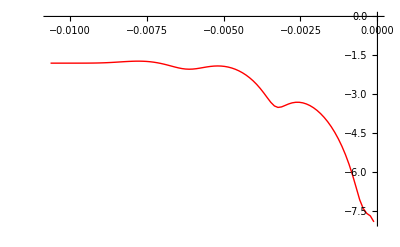

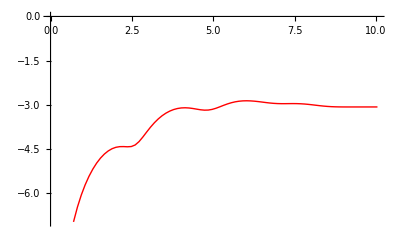

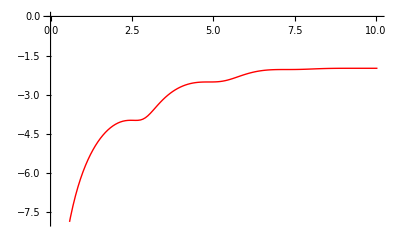

```mathematica
plotIon[ionData_,tMAX_]:=Module[{steps=Length[ionData ],dt},
dt=tMAX/steps;
ListLinePlot[Table[{i dt,Log[10,ionData[[i]]]},{i,1,Length@ionData}],PlotStyle->{Red,Thick}]
]

tMAXh=Import[hDIR<>"tMAX.dat"][[1,1]]
tMAXhe=Import[heDIR<>"tMAX.dat"][[1,1]]
tMAXli=Import[liDIR<>"tMAX.dat"][[1,1]]
ionPlotA=plotIon[ionDataA,tMAXh]
ionPlotB=plotIon[ionDataB,tMAXhe]
ionPlotC=plotIon[ionDataC,tMAXhe]
```

### Bound State Excitation

#### Tables

```mathematica
tag[c_,n_]:=ToString[c]<>" = "<>ToString[n]
tabulateBoundP[dat_List,t_]:=Module[{n,nMAX,l,prob,output},
nMAX=Max[Cases[dat,{n_,l_,prob__}:>n]];
output=Table[0,{i,1,nMAX+1},{j,0,nMAX-1}];
For[i=1,i≤Length[dat],i++,
(*Print["n = ",dat[[i,1]],"  l = ",dat[[i,2]]];*)
n=dat[[i,1]];
l=dat[[i,2]];
prob=dat[[i,t]];
output[[n,l+1]]=prob;
];
For[l=0,l<nMAX,l++,
output[[nMAX+1,l+1]]=Sum[output[[n,l+1]],{n,2,nMAX}];
];
TableForm[output[[2;;]],TableHeadings->{Append[Table[tag["n",i],{i,2,nMAX}],"Total"],Table[tag[ℓ,i],{i,0,nMAX-1}]}]
]



totalExcitationP[dat_List,t_]:=Total[#[[t]]&/@dat]
boundA=Import[dataDIR<>"H05/ex.dat"];
boundB=Import[dataDIR<>"He05/ex.dat"];
boundC=Import[dataDIR<>"2Li1/ex.dat"];
tSTEPa=Length[First@boundA];
tSTEPb=Length[First@boundB];
tSTEPc=Length[First@boundC];
tabulateBoundP[boundA,tSTEPa]
tabulateBoundP[boundB,tSTEPb]
tabulateBoundP[boundC,tSTEPc]
totalExcitationP[boundA,tSTEPa]
totalExcitationP[boundB,tSTEPb]
totalExcitationP[boundC,tSTEPc]
```

#### Prereq

```mathematica
fMAX[dat_]:=With[{fNUM=Length[First[dat]]},
maxList={};
For[i=1,i≤Length[dat],i++,
thisMax=Max[dat[[i,4;;]] ];
AppendTo[maxList,thisMax];
];
Max[maxList]
]
plotBound[boundData_,tMAX_,nList_List,opts___]:=Module[{steps,dt,dat1,dat2},
steps=Length[boundData[[1]]]-4;
dt=N[tMAX/steps];
Print[Table[boundData[[i,;;3]],{i,nList}]];
dat1=Table[{(i-4) dt,Log[10,boundData[[n,i]] ]},{n,nList},{i,4,Length@boundData[[1]]}];
dat2=Cases[#,{x_,y_}/;x≤10]&/@dat1;
ListLinePlot[dat2,opts]
]

plotBoundPulse[boundData_,tMAX_,nList_List,opts___]:=Module[{steps=Length[boundData[[1,4;;]] ],tPulse=10,dt,nPulse},
dt=tMAX/steps;
nPulse=tPulse/dt;
ListPlot[Table[{(i-3) dt,boundData[[n,i]]},{n,nList},{i,4,Min[nPulse+3,Length@boundData[[1]]]}],opts]
]
plotIon[ionData_,tMAX_]:=Module[{steps=Length[ionData ],dt},
dt=tMAX/steps;
ListPlot[Table[{i dt,Log[10,ionData[[i]]]},{i,1,Length@ionData}],PlotStyle->{Red,Thick},Joined->True]
]
```

#### H

{{9,0,0},{2,1,0},{3,1,0},{4,1,0}}

{{1,0,0},{2,0,0},{3,0,0}}

{{9,1,0},{3,2,0},{4,2,0},{5,2,0}}

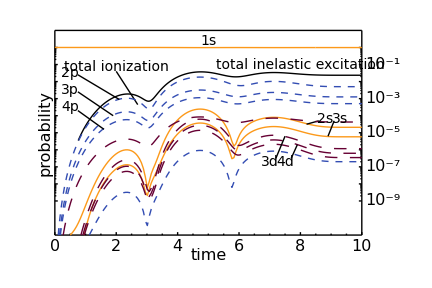

```mathematica
minusOne[lst_List]:={#[[1]],Log[10,1-(#[[2]])^2]}&/@lst;
groundStA=Union[Import[hDIR<>"overlap.dat"]];
totalExA=minusOne@groundStA;
boundA=Import[dataDIR<>"H05e-7/ex.dat"];
tSTEPa=Length[First@boundA];
tMAXh=Import[hDIR<>"tMAX.dat"][[1,1]];
tMAXh=10;
ns=Table[n,{n,1,3}];
np=Table[n,{n,9,12}];
nd=Table[n,{n,17,20}];
nf=Table[n,{n,24,27}];
ng=Table[n,{n,31,33}];
hExFIG=Figure[{
SetOptions[ManualLabel,FontSize->14],
SetOptions[ScaledLabel,FontSize->14],
FigurePanel[
{{0,1},{0,1}},
FontSize->16,
PlotRange->{{0,10},{-11,1.0}},
FrameTicks->{LinTicks[0,10],LogTicks[-9,0,TickLabelStep->2],None,LogTicks[-9,0,TickLabelStep->2]},
ShowTickLabels->{True,False,False,True},
LabB->"time",BufferB->3,
LabL->"probability",BufferL->1.5,
TickNudge->{-4,0,0,{4,0}}
],
ScaledLabel[{0.50,0.95},"1s"],
RawGraphics[ListLinePlot[{#[[1]],Log[10,#[[2]]]}&/@groundStA,PlotStyle->styleList[[3]]]],
RawGraphics[ListLinePlot[totalExA,PlotStyle->{Black,Thickness[Large]}]],
ScaledLabel[{0.8,0.83},"total inelastic excitation"],
RawGraphics[ionPlotA],
ScaledLabel[{0.2,0.82},"total ionization"],
SchemeLine[{{2,-1.4},{2.7,-3.35}}],
RawGraphics[plotBound[boundA,tMAXh,np,PlotStyle->{styleList[[2]]}]],
ManualLabel[{0.5,-1.5},"2p"],
ManualLabel[{0.5,-2.5},"3p"],
ManualLabel[{0.5,-3.5},"4p"],
SchemeLine[{{0.75,-1.6},{2.1,-3.05}}],
SchemeLine[{{0.75,-2.6},{1.9,-4.0}}],
SchemeLine[{{0.75,-3.7},{1.6,-4.8}}],
RawGraphics[plotBound[boundA,tMAXh,ns,PlotStyle->{styleList[[3]]}]],
ManualLabel[{8.8,-4.2},"2s"],
ManualLabel[{9.3,-4.2},"3s"],
SchemeLine[{{8.6,-4.3},{8.2,-4.5}}],
SchemeLine[{{9.1,-4.3},{8.9,-5.2}}],
RawGraphics[plotBound[boundA,tMAXh,nd,PlotStyle->{styleList[[4]]}]],
ManualLabel[{7.0,-6.7},"3d"],
SchemeLine[{{7.2,-6.5},{7.5,-5.2}}],
ManualLabel[{7.5,-6.7},"4d"],
SchemeLine[{{7.7,-6.5},{7.9,-5.7}}]
(*,
RawGraphics[plotBound[boundA,tMAXh,nf,PlotStyle->{styleList[[5]]}]],
ManualLabel[{7.1,-7.5},"4f"],
SchemeLine[{{7.2,-7.7},{7.5,-7.9}}]*)
},
PlotRange->{{-0.05,1.1},{-0.13,1.02}},ImageSize->72{6,4}
]
If[False,Export[exportPath<>"hEx."<>suffix,hExFIG]]
```

#### He+

```mathematica
minusOne[lst_List]:={#[[1]],Log[10,1-(#[[2]])^2]}&/@lst;
groundStB=Union[Import[heDIR<>"overlap.dat"]];
totalExB=minusOne@groundStB;
tMAXhe=Import[heDIR<>"tMAX.dat"][[1,1]];
boundB=Import[heDIR<>"ex2.dat"];
tSTEPb=Length[First@boundB];
ns=Table[n,{n,1,4}];
np=Table[n,{n,9,12}];
nd=Table[n,{n,17,20}];
nf=Table[n,{n,24,27}];
ng=Table[n,{n,34,37}];

heExFIG=Figure[{
SetOptions[ManualLabel,FontSize->14],
SetOptions[ScaledLabel,FontSize->14],
FigurePanel[
{{0,1},{0,1}},
FontSize->16,
PlotRange->{{0,10},{-11,1.0}},
FrameTicks->{LinTicks[0,10],LogTicks[-11,0,TickLabelStep->2],None,LogTicks[-9,0,TickLabelStep->2]},
ShowTickLabels->{True,False,False,True},
LabB->"time",BufferB->3,
LabL->"probability",BufferL->1.5,
TickNudge->{-4,0,0,{3,0}}
],
ScaledLabel[{0.50,0.96},"1s"],
RawGraphics[ListLinePlot[{#[[1]],Log[10,#[[2]]]}&/@groundStB,PlotStyle->{styleList[[3]]}]],RawGraphics[ListLinePlot[totalExB,PlotStyle->{Black,Thickness[Large]}]],
ScaledLabel[{0.8,0.82},"total inelastic excitation"],
RawGraphics[ionPlotB],
ScaledLabel[{0.2,0.82},"total ionization"],
SchemeLine[{{2,-1.4},{2.1,-4.4}}],
RawGraphics[plotBound[boundB,tMAXhe,np,PlotStyle->{styleList[[2]]}]],
ManualLabel[{0.4,-2},"2p"],
ManualLabel[{0.4,-3},"3p"],
ManualLabel[{0.4,-4},"4p"],
SchemeLine[{{0.65,-2.3},{3.5,-2.75}}],
SchemeLine[{{0.65,-3.3},{3.2,-3.9}}],
SchemeLine[{{0.65,-4.3},{1.9,-5.2}}],
RawGraphics[plotBound[boundB,tMAXhe,ns,PlotStyle->{styleList[[3]]}]],
ManualLabel[{2.4,-6.8},"2s"],
RawGraphics[plotBound[boundB,tMAXhe,nd,PlotStyle->{styleList[[4]]}]],
ManualLabel[{1.6,-6.8},"3d"],
SchemeLine[{{1.75,-7.0},{2.3,-7.9}}],
RawGraphics[plotBound[boundB,tMAXhe,nf,PlotStyle->{styleList[[5]]}]],
ManualLabel[{8.5,-6.5},"4f"],
SchemeLine[{{8.4,-6.6},{8.0,-7.0}}],
ManualLabel[{9.0,-6.5},"5f"],
SchemeLine[{{8.9,-6.6},{8.2,-7.3}}]
},
PlotRange->{{-0.05,1.1},{-0.13,1.02}},ImageSize->72{6,4}
]

If[export,Export[exportPath<>"heEx."<>suffix,heExFIG]]
```

#### Li++

{{2,1,0},{3,1,0}}

{{1,0,0},{3,0,0}}

{{3,2,0}}

{{4,3,0}}

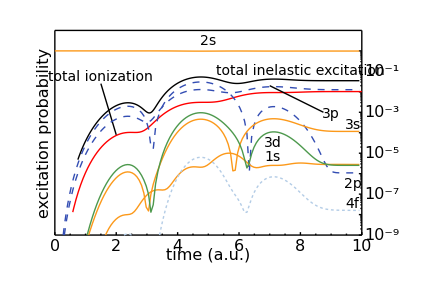

/Users/nevence/Documents/utk/first/liEx.pdf

```mathematica
minusOne[lst_List]:={#[[1]],Log[10,1-(#[[2]])^2]}&/@lst;
groundStC=Union[Import[liDIR<>"overlap.dat"]];
totalExC=minusOne@groundStC;
tMAXli=Import[liDIR<>"tMAX.dat"][[1,1]];
boundC=Import[liDIR<>"ex.dat"];
tSTEPc=Length[First@boundC];
ns={1,3};
np=Table[n,{n,10,11}];
nd=Table[n,{n,18,18}];
nf=Table[n,{n,25,25}];
ng=Table[n,{n,34,36}];

liExFIG=Figure[{
SetOptions[ManualLabel,FontSize->14],
SetOptions[ScaledLabel,FontSize->14],
FigurePanel[
{{0,1},{0,1}},
FontSize->16,
PlotRange->{{0,10},{-9,1.0}},
FrameTicks->{LinTicks[0,10],None,None,LogTicks[-9,0,TickLabelStep->2]},
ShowTickLabels->{True,False,False,True},
LabB->"time (a.u.)",BufferB->3,
LabL->"excitation probability",BufferL->1.5,
TickNudge->{-4,0,0,{3,0}}
],
ManualLabel[{5,0.5},"2s"],
RawGraphics[ListLinePlot[{#[[1]],Log[10,#[[2]]]}&/@groundStC,PlotStyle->{styleList[[3]]}]],
RawGraphics[ListLinePlot[totalExC,PlotStyle->{Black,Thickness[Large]}]],
ManualLabel[{8,-1},"total inelastic excitation"],
RawGraphics[ionPlotC],
ManualLabel[{1.5,-1.3},"total ionization"],
SchemeLine[{{1.5,-1.6},{2,-4.1}}],
RawGraphics[plotBound[boundC,tMAXli,np,PlotStyle->{styleList[[2]]}]],
ManualLabel[{9.7,-6.5},"2p"],
ManualLabel[{9.0,-3.1},"3p"],
SchemeLine[{{8.75,-3.0},{7.0,-1.7}}],
RawGraphics[plotBound[boundC,tMAXli,ns,PlotStyle->{styleList[[3]]}]],
ManualLabel[{9.7,-3.6},"3s"],
ManualLabel[{7.1,-5.2},"1s"],

RawGraphics[plotBound[boundC,tMAXli,nd,PlotStyle->{styleList[[5]]}]],
ManualLabel[{7.1,-4.5},"3d"],
RawGraphics[plotBound[boundC,tMAXli,nf,PlotStyle->{styleList[[6]]}]],
ManualLabel[{9.7,-7.5},"4f"]
},
PlotRange->{{-0.05,1.1},{-0.13,1.02}},ImageSize->72{6,4}
]
If[export,Export[exportPath<>"liEx."<>suffix,liExFIG]]
```

## Energy and Excitation

```mathematica
enA=Union[Import[hDIR<>"energy.dat"]];
enB=Union[Import[heDIR<>"energy.dat"]];
minusOne[lst_List]:={#[[1]],1-(#[[2]])^2}&/@lst;
totalExA=minusOne@Union[Import[hDIR<>"overlap.dat"]];
totalExB=minusOne@Union[Import[heDIR<>"overlap.dat"]];

laser[nCycle_,ω_,t_]:=
If[ω t> 0 && (ω t)/(2nCycle)<π,Sin[(ω t)/(2nCycle)]^2 Sin[ω t],0]
laserY=-0.5;
laserAmp=0.006;
laserPl=Plot[laserAmp*laser[2,1.32,t]+laserY,{t,0,10},
Filling->Axis,
AxesOrigin->{0,laserY}];

enexFig=Figure[
{
SetOptions[ScaledLabel,FontSize->14],
Multipanel[
{{0,1},{0,1}},
{3,1},
XPlotRanges->{0,10},
YPlotRanges->{{-0.5,-0.45},{-2,-1.95},{0,0.04}},
XFrameLabels->"time",
YFrameLabels->{"energy H","energy He^+","1 - |⟨ψ_0|ψ(t)⟩|^2"},
BufferB->3,
BufferL->6,
XFrameTicks->LinTicks[0,10,2.,2],
YFrameTicks->{
LinTicks[-0.5,-0.455,0.02,2],
LinTicks[-2.0,-1.955,0.02,2],
LinTicks[0.0,0.039,0.01,2]},
FontSize->16,
TickFontSize->14,
TickNudge->{-3,{-4,0},0,0}
],
(*Energy H vs time *)
FigurePanel[{1,1}],
RawGraphics[ListLinePlot[enA,PlotStyle->styleList[[1]]]],
ScaledLabel[{0.2,0.85},"H"],
(*Energy He vs time *)
FigurePanel[{2,1}],
RawGraphics[ListLinePlot[enB,PlotStyle->styleList[[2]]]],
ScaledLabel[{0.2,0.85},"He^+"],
(*Total Excitation vs time *)
FigurePanel[{3,1}],
RawGraphics[ListLinePlot[{totalExA,totalExB},PlotStyle->styleList]],
ScaledLabel[{0.25,0.65},"H"],
SchemeLine[{{2.5,0.024},{3.75,0.01}}],
ScaledLabel[{0.7,0.15},"He^+"],
SchemeLine[{{5.8,0.016},{6.5,0.008}}]
},
PlotRange->{{-0.16,1.02},{-0.08,1.02}},ImageSize->72*2*{3,3}
]
If[export,Export[exportPath<>"enex."<>suffix,enexFig]]
Clear[x0,x1,x2,x3,dy,y0,y1,y2,y3,y4]
```

## Accel

```mathematica
laser[nCycle_,ω_,t_]:=
If[ω t> 0 && (ω t)/(2nCycle)<π,Sin[(ω t)/(2nCycle)]^2 Sin[ω t],0];
F[plotDat_List,ω_]:=With[{t=#[[1]]&/@ plotDat,f=#[[2]]&/@ plotDat},
 1/(√(2π))Sum[f[[n]] ⅇ^(-I ω t[[n]])(t[[n+1]]-t[[n]]),{n,1,Length[f]-1}]
];
abFT[plotDat_List,dω_,ωMAX_]:=Table[{ω,Abs[F[plotDat,ω]]^2},{ω,0,ωMAX,dω}];
subtractLaser[dat_,nCycle_,ℰ_,ω_]:={#[[1]],ℰ*laser[nCycle,ω,#[[1]]]-#[[2]]}&/@dat
filter[dat_,n_,c_]:=Module[{tMAX=dat[[-1,1]],dat1,dat2,dat3},
dat1={(2/tMAX#[[1]]-1),#[[2]]}&/@dat;
dat2={#[[1]],(1+(#[[1]]/c)^(2n))^-1#[[2]]}&/@dat1;
dat3={tMAX/2(#[[1]]+1),#[[2]]}&/@dat2;
(*
GraphicsGrid[{
{ListPlot[dat]},
{ListPlot[dat1]},
{ListPlot[dat2]},
{ListPlot[dat3]}
}]
*)
dat3
]
```

### Linear

```mathematica
accelA=Import[hDIR<>"accel.dat"];
accelB=Import[dataDIR<>"He06LONG/accel.dat"];
accelC=Union[Import[liDIR<>"accel.dat"]];
aDAT=filter[subtractLaser[accelA,2,0.176,1.32],6,0.8];
bDAT=filter[subtractLaser[accelB,2,0.176,1.32],6,0.8];
cDAT=filter[subtractLaser[accelC,2,0.176,1.32],6,0.8];
aFTDAT=abFT[aDAT,0.02,3];
bFTDAT=abFT[bDAT,0.01,3];
cFTDAT=abFT[cDAT,0.02,3];
```

```mathematica
hAccelFIG=Figure[{
FigurePanel[
{{0,1},{0,1}},
FontSize->15,
PlotRange->{{0,3},{0,0.006}},
FrameTicks->{Automatic,None},
LabB->"ω [atomic units]",BufferB->3,
LabL->"Power Spectrum [arb. units]",BufferL->3,
TickNudge->{-2,0,0,0}
],
RawGraphics[ListLinePlot[aFTDAT,PlotRange->All]],
ScaledFigurePanel[
{{0.65,0.98},{0.6,0.98}},
PlotRange->{{0,10},{-0.1,0.1}},
FrameTicks->{LinTicks[0,10],None},
LabB->"time [atomic units]",BufferB->3,
LabL->"ℰ(t) - ⟨ψ(t)|dV/dz|ψ(t)⟩",BufferL->3,
TickNudge->{-2,0,0,0}
],
RawGraphics[ListLinePlot[aDAT,PlotStyle->{Black,Thickness[Large]}]],
SchemeLine[{{0,0},{10,0}}]
},
PlotRange->{{-0.1,1.03},{-0.15,1.02}},ImageSize->72{6,4}
]

heAccelFIG=Figure[{
FigurePanel[
{{0,1},{0,1}},
FontSize->15,
PlotRange->{{0,3},{0,5}},
FrameTicks->{Automatic,None},
LabB->"ω [atomic units]",BufferB->3,
LabL->"Power Spectrum [arb. units]",BufferL->3,
TickNudge->{-2,0,0,0}
],
RawGraphics[ListLinePlot[bFTDAT,PlotRange->All]],
ScaledFigurePanel[
{{0.65,0.98},{0.6,0.98}},
PlotRange->{{0,50},{-0.3,0.3}},
FrameTicks->{LinTicks[0,50],None},
LabB->"time [atomic units]",BufferB->3,
LabL->"ℰ(t) - ⟨ψ(t)|dV/dz|ψ(t)⟩",BufferL->3,
TickNudge->{-2,0,0,0}
],
RawGraphics[ListLinePlot[bDAT,PlotStyle->{Black,Thickness[Large]}]],
SchemeLine[{{0,0},{50,0}}]
},
PlotRange->{{-0.1,1.03},{-0.15,1.02}},ImageSize->72{6,4}
]

liAccelFIG=Figure[{
FigurePanel[
{{0,1},{0,1}},
FontSize->15,
PlotRange->{{0,3},{0,0.05}},
FrameTicks->{Automatic,None},
LabB->"ω [atomic units]",BufferB->3,
LabL->"Power Spectrum [arb. units]",BufferL->3,
TickNudge->{-2,0,0,0}
],
RawGraphics[ListLinePlot[cFTDAT,PlotRange->All]],
ScaledFigurePanel[
{{0.65,0.98},{0.6,0.98}},
PlotRange->{{0,10},{-0.3,0.3}},
FrameTicks->{LinTicks[0,10],None},
LabB->"time [atomic units]",BufferB->3,
LabL->"ℰ(t) - ⟨ψ(t)|dV/dz|ψ(t)⟩",BufferL->3,
TickNudge->{-2,0,0,0}
],
RawGraphics[ListLinePlot[cDAT,PlotStyle->{Black,Thickness[Large]}]],
SchemeLine[{{0,0},{10,0}}]
},
PlotRange->{{-0.1,1.03},{-0.15,1.02}},ImageSize->72{6,4}
]
If[export,Export[exportPath<>"hAccel."<>suffix,hAccelFIG]]
If[export,Export[exportPath<>"heAccel."<>suffix,heAccelFIG]]
If[export,Export[exportPath<>"liAccel."<>suffix,liAccelFIG]]
```

### Logarithmic

```mathematica
aFTDAT=abFT[accelA,0.02,5];
bFTDAT=abFT[accelB,0.01,5];
cFTDAT=abFT[accelC,0.02,5];
```

```mathematica
hAccelFIG=Figure[{
FigurePanel[
{{0,1},{0,1}},
FontSize->15,
PlotRange->{{0,5},{-13,-3}},
FrameTicks->{Automatic,LogTicks[-13,-3,TickLabelStep->2]},
LabB->"ω [atomic units]",BufferB->2.5,
LabL->"Log[| ℱ[⟨dV/dz⟩]|^2 ]",BufferL->6
],
RawGraphics[ListLogPlot[aFTDAT,PlotRange->All,Joined->True]],
ScaledLabel[{0.8,0.92},"⟨ψ(t)|dV/dz|ψ(t)⟩"],
ScaledFigurePanel[
{{0.6,0.98},{0.45,0.85}},
PlotRange->{{0,10},{-0.3,0.3}},
FrameTicks->{LinTicks[0,10],Automatic},
ShowTickLabels->{True,False,False,True},
ShowFrameLabels->{True,True,False,True},
LabB->"time [atomic units]",BufferB->2.5,
LabL->"arb. units"
],
RawGraphics[ListLinePlot[accelA,PlotStyle->{Black,Thickness[Large]}]],
SchemeLine[{{0,0},{10,0}}]
},
PlotRange->{{-0.2,1.02},{-0.12,1.05}},ImageSize->72{6,4}
]

heAccelFIG=Figure[{
FigurePanel[
{{0,1},{0,1}},
FontSize->15,
PlotRange->{{0,5},{-9,2}},
FrameTicks->{Automatic,LogTicks[-9,2,TickLabelStep->2]},
LabB->"ω [atomic units]",BufferB->2.5,
LabL->"Log[| ℱ[⟨dV/dz⟩]|^2 ]",BufferL->6
],
RawGraphics[ListLogPlot[bFTDAT,PlotRange->All,Joined->True]],
ScaledLabel[{0.8,0.92},"⟨ψ(t)|dV/dz|ψ(t)⟩"],
ScaledFigurePanel[
{{0.6,0.98},{0.45,0.85}},
PlotRange->{{0,40},{-0.3,0.3}},
FrameTicks->{LinTicks[0,40],Automatic},
ShowTickLabels->{True,False,False,True},
ShowFrameLabels->{True,True,False,True},
LabB->"time [atomic units]",BufferB->2.5,
LabL->"arb. units"
],
RawGraphics[ListLinePlot[accelB,PlotStyle->{Black,Thickness[Large]}]],
SchemeLine[{{0,0},{40,0}}]
},
PlotRange->{{-0.2,1.02},{-0.12,1.05}},ImageSize->72{6,4}
]

liAccelFIG=Figure[{
FigurePanel[
{{0,1},{0,1}},
FontSize->15,
PlotRange->{{0,5},{-13,-3}},
FrameTicks->{Automatic,LogTicks[-13,-3,TickLabelStep->2]},
LabB->"ω [atomic units]",BufferB->2.5,
LabL->"Log[| ℱ[⟨dV/dz⟩]|^2 ]",BufferL->6
],
RawGraphics[ListLogPlot[cFTDAT,PlotRange->All,Joined->True]],
ScaledLabel[{0.8,0.92},"⟨ψ(t)|dV/dz|ψ(t)⟩"],
ScaledFigurePanel[
{{0.6,0.98},{0.45,0.85}},
PlotRange->{{0,10},{-0.3,0.3}},
FrameTicks->{LinTicks[0,10],Automatic},
ShowTickLabels->{True,False,False,True},
ShowFrameLabels->{True,True,False,True},
LabB->"time [atomic units]",BufferB->2.5,
LabL->"arb. units"
],
RawGraphics[ListLinePlot[accelC,PlotStyle->{Black,Thickness[Large]}]],
SchemeLine[{{0,0},{10,0}}]
},
PlotRange->{{-0.2,1.02},{-0.12,1.05}},ImageSize->72{6,4}
]
If[export,Export[exportPath<>"hAccel."<>suffix,hAccelFIG]]
If[export,Export[exportPath<>"heAccel."<>suffix,heAccelFIG]]
If[export,Export[exportPath<>"liAccel."<>suffix,liAccelFIG]]
```

### error testing

The time window determines the spacing of the wiggles

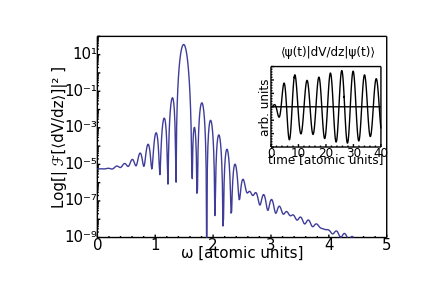

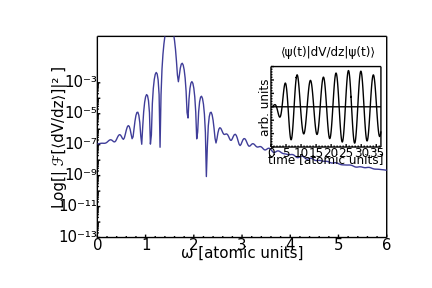

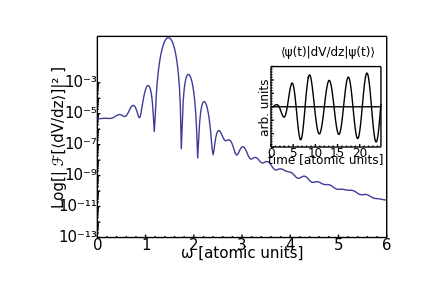
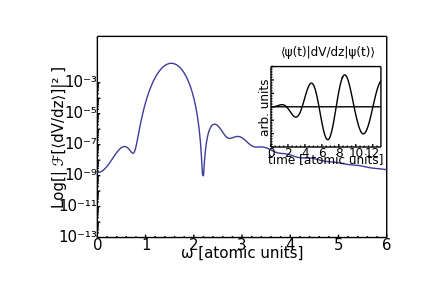

```mathematica
accelB=Import[dataDIR<>"He06LONG/accel.dat"];
Length[accelB]
nMAX=3100;
bFTDAT=abFT[accelB[[;;nMAX]],0.02,6];
tMAX=accelB[[nMAX,1]]
```

```mathematica
Figure[{
FigurePanel[
{{0,1},{0,1}},
FontSize->15,
PlotRange->{{0,6},{-13,0}},
FrameTicks->{Automatic,LogTicks[-13,-3,TickLabelStep->2]},
LabB->"ω [atomic units]",BufferB->2.5,
LabL->"Log[| ℱ[⟨dV/dz⟩]|^2 ]",BufferL->6
],
RawGraphics[ListLogPlot[bFTDAT,PlotRange->All,Joined->True]],
ScaledLabel[{0.8,0.92},"⟨ψ(t)|dV/dz|ψ(t)⟩"],
ScaledFigurePanel[
{{0.6,0.98},{0.45,0.85}},
PlotRange->{{0,tMAX},{-0.3,0.3}},
FrameTicks->{LinTicks[0,tMAX],Automatic},
ShowTickLabels->{True,False,False,True},
ShowFrameLabels->{True,True,False,True},
LabB->"time [atomic units]",BufferB->2.5,
LabL->"arb. units"
],
RawGraphics[ListLinePlot[accelB,PlotStyle->{Black,Thickness[Large]}]],
SchemeLine[{{0,0},{tMAX,0}}]
},
PlotRange->{{-0.2,1.02},{-0.12,1.05}},ImageSize->72{6,4}
]
```

## Angular ionization

```mathematica
sumL[dat_List]:=Module[{n,l,prob,tMAX,lMAX,cL},
tMAX=Length[dat[[1]]];
lMAX=Max[Cases[dat,{n_,l_,prob__}:>l]];
cL=Table[0,{i,1,lMAX+1}];
For[i=1,i≤Length[dat],i++,
(*Print["n = ",dat[[i,1]],"  l = ",dat[[i,2]]];*)
n=dat[[i,1]];
l=dat[[i,2]];
prob=dat[[i,tMAX]];
cL[[l+1]]+=prob;
];
cL
]

angularInfo[str_]:=Module[{Nl,
(*cL represents the probability |cL|^2*)
cLtot=#[[2]]&/@Import[str<>"/Rl.dat"],(*Total angular probabilit*)
cLbnd=sumL[Import[str<>"/ex.dat"]],(*Array of bound probabilities*)
groundP=(Import[str<>"/overlap.dat"][[-1,2]])^2},
Nl=Min[Length[cLtot],Length[cLbnd]]; (*Number of angular momentum components to print*)
cLtot=cLtot[[;;Nl]];
cLbnd=cLbnd[[;;Nl]];
Print["|c_ℓ^bound|^2 before ground state:",cLbnd];
cLbnd[[1]]+=groundP;
Print["|c_ℓ^bound|^2 after ground state: ",cLbnd];
Print["|c_ℓ^total|^2:                    ",cLtot];
Print["|c_ℓ^total|^2 - |c_ℓ^bound|^2:         ",cLtot-cLbnd[[;;Length[cLtot]]]];
]
```

### H

```mathematica
angularInfo[dataDIR<>"H05e-7/"]
```

|c_ℓ^bound|^2 before ground state:{0.0000318047,0.00739709,2.64751×10^-6,1.40947×10^-10,9.8648×10^-13,1.92841×10^-12}

|c_ℓ^bound|^2 after ground state: {0.976475,0.00739709,2.64751×10^-6,1.40947×10^-10,9.8648×10^-13,1.92841×10^-12}

|c_ℓ^total|^2:                    {0.976409,0.0232227,0.00017741,1.11699×10^-6,5.63395×10^-9,7.17225×10^-10}

|c_ℓ^total|^2 - |c_ℓ^bound|^2:         {-0.0000658073,0.0158256,0.000174763,1.11685×10^-6,5.63296×10^-9,7.15296×10^-10}

### He

```mathematica
angularInfo[dataDIR<>"He06e-7/"]
```

|c_ℓ^bound|^2 before ground state:{0.000130838,0.024352,0.000155472,8.05663×10^-8,7.34851×10^-11,2.77026×10^-11}

|c_ℓ^bound|^2 after ground state: {0.974647,0.024352,0.000155472,8.05663×10^-8,7.34851×10^-11,2.77026×10^-11}

|c_ℓ^total|^2:                    {0.97073,0.0092447,5.49149×10^-6,3.55418×10^-10,3.33552×10^-13,1.90973×10^-13}

|c_ℓ^total|^2 - |c_ℓ^bound|^2:         {-0.00391714,-0.0151073,-0.000149981,-8.02108×10^-8,-7.31516×10^-11,-2.75116×10^-11}

Houston, we have a problem.

### Li

```mathematica
(*nGrid = 1000*)
angularInfo[dataDIR<>"2Li03e-6/"]
```

|c_ℓ^bound|^2 before ground state:{0.000197218,0.0243904,0.0000411062,4.50918×10^-8,5.12193×10^-9,1.24868×10^-8}

|c_ℓ^bound|^2 after ground state: {0.965263,0.0243904,0.0000411062,4.50918×10^-8,5.12193×10^-9,1.24868×10^-8}

|c_ℓ^total|^2:                    {0.965323,0.0333028,0.000460438,2.24137×10^-6,1.03097×10^-8,3.85023×10^-9}

|c_ℓ^total|^2 - |c_ℓ^bound|^2:         {0.000059872,0.00891246,0.000419332,2.19628×10^-6,5.18774×10^-9,-8.63653×10^-9}

```mathematica
(*nGrid = 2000*)
angularInfo[dataDIR<>"2Li03e-6/"]
```

|c_ℓ^bound|^2 before ground state:{0.000197218,0.0243904,0.0000411062,4.50918×10^-8,5.12193×10^-9,1.24868×10^-8}

|c_ℓ^bound|^2 after ground state: {0.965263,0.0243904,0.0000411062,4.50918×10^-8,5.12193×10^-9,1.24868×10^-8}

|c_ℓ^total|^2:                    {0.965324,0.0333029,0.000460435,2.24154×10^-6,1.037×10^-8,3.84735×10^-9}

|c_ℓ^total|^2 - |c_ℓ^bound|^2:         {0.0000610613,0.00891258,0.000419329,2.19645×10^-6,5.24803×10^-9,-8.63942×10^-9}

```mathematica
(*nGrid = 4000*)
angularInfo[dataDIR<>"2Li03e-6/"]
```

|c_ℓ^bound|^2 before ground state:{0.000197218,0.0243904,0.0000411062,4.50918×10^-8,5.12193×10^-9,1.24868×10^-8}

|c_ℓ^bound|^2 after ground state: {0.965263,0.0243904,0.0000411062,4.50918×10^-8,5.12193×10^-9,1.24868×10^-8}

|c_ℓ^total|^2:                    {0.965324,0.033303,0.000460435,2.24159×10^-6,1.0386×10^-8,3.84675×10^-9}

|c_ℓ^total|^2 - |c_ℓ^bound|^2:         {0.0000613578,0.00891262,0.000419329,2.19649×10^-6,5.2641×10^-9,-8.64001×10^-9}

```mathematica
(*nGrid = 8000*)
angularInfo[dataDIR<>"2Li03e-6/"]
```

|c_ℓ^bound|^2 before ground state:{0.000197218,0.0243904,0.0000411062,4.50918×10^-8,5.12193×10^-9,1.24868×10^-8}

|c_ℓ^bound|^2 after ground state: {0.965263,0.0243904,0.0000411062,4.50918×10^-8,5.12193×10^-9,1.24868×10^-8}

|c_ℓ^total|^2:                    {0.965324,0.033303,0.000460435,2.2416×10^-6,1.03901×10^-8,3.84661×10^-9}

|c_ℓ^total|^2 - |c_ℓ^bound|^2:         {0.0000614321,0.00891262,0.000419328,2.19651×10^-6,5.26819×10^-9,-8.64015×10^-9}

Illustrations

```mathematica
hDIR=dataDIR<>"H05e-7/";
heDIR=dataDIR<>"He06e-7/";
liDIR=dataDIR<>"2Li03e-6/";
```

## Ionization

### Prereq

```mathematica
sowMirrorData[kx_,kz_,f_]:=Module[{},
If[kx≠0,Sow[{-kx,kz,Log[10,(kx^2+kz^2)*f]}]];
Sow[{kx,kz,Log[10,(kx^2+kz^2)*f]}];
]

(*2D plot of the electron's ionization*)
dPdkdΩ[dat_,fNUM_,opts___]:=ListContourPlot[Reap[
sowMirrorData[#[[1]],#[[2]],#[[fNUM]]]&/@dat][[2,1]]
]


rawGraphicsdPdΩ[dat_List,fNUM_,hue_]:=Module[{
dk,dθ,dϕ=2π,tol=0.00001,kMAX,sum,sin,pup,pdown,xMAX,yMAX,angle,xz2rθ,points,points2,i,nk,nθ,m,n,tSum=0,ylowerMAX,yupperMAX,
k,θ,θnext,f,angularCS={}},
(*The points on the z-axis must be handled carefully, for it needs to represent a cone, but Sin[θ] give it zero width. See journal E pg 18 for a description of the special case Jacobian.
*)
angle[x_,z_]:=If[x≥0,
If[z≠0,If[z>0,ArcTan[x/z],ArcTan[x/z]+π],π/2],
If[z≠0,If[z<0,-ArcTan[x/z]+π,-ArcTan[x/z]],π/2]];
xz2rθ[{x_,z_,f___}]:={√(x^2+z^2),angle[x,z],f};
(* Steps 1 & 2
Turning them into polar cordinates and
Sorting them in increasing θ *)
points=Sort[xz2rθ/@dat,#1[[2]]<#2[[2]]&];
For[i=1,i≤Length[points]-2,i++,
If[Abs[points[[i,2]]-points[[i+1,2]]]>tol,
nk=i;
Break[];
];
];

dk = Abs[points[[2,1]]-points[[1,1]]];
(* Steps 3 & 4
Partitioning the list and then sorting each according to r *)
points2=Sort/@Partition[points,nk];

nθ=Length[points2];
dθ = Abs[points2[[2,1,2]]-points2[[1,1,2]]];
sin[θ_]:=If[((Abs[θ]>tol)&&(π-Abs[θ])>tol),Sin[θ],1/2 Sin[dθ/4]];
(*Print["dk = ",dk,"   dθ = ",dθ,"   dϕ = ",dϕ,"   nθ = ",nθ,"   nk = ",nk];*)
For[m=1,m≤nθ,m++,
sum=0;
θ=points2[[m,1,2]];
(* Step 5
Integrate dk *)
For[n=1,n<nk,n++,
k=points2[[m,n,1]];
f=points2[[m,n,fNUM]];
(*θ is in the middle *)
sum+=f*k^2 dk;
tSum+=f*k^2 Sin[θ]dk dθ dϕ;
];
AppendTo[angularCS,{θ,sum}];
];

f=Interpolation[angularCS];
Off[Interpolation::inhr];
sum=0;
For[i=1,i≤Length[angularCS],i++,
sum+= sin[angularCS[[i,1]]]dθ dϕ *angularCS[[i,2]];
];
Print["Total Ionization Probability = ",sum];
pup=PolarPlot[f[θ-π/2],{θ,π/2,3π/2},
PlotStyle->styleList[[hue]],
Axes->None
];
Off[InterpolatingFunction::"dmval"];
pdown=PolarPlot[f[π/2-θ],{θ,-π/2,π/2},
PlotStyle->styleList[[hue]],
FrameTicks->None,
Axes->None
];
xMAX=Max[#[[2]]*Sin[#[[1]]]&/@angularCS];
yupperMAX=Max[#[[2]]*Cos[#[[1]]]&/@angularCS];
ylowerMAX=Max[-#[[2]]*Cos[#[[1]]]&/@angularCS];
Print["xMAX = ",xMAX];
Print["yupperMAX = ",yupperMAX];
Print["ylowerMAX = ",ylowerMAX];
Sequence@@{RawGraphics[pdown],RawGraphics[pup]}
]

F[plotDat_List,ω_]:=With[{t=#[[1]]&/@ plotDat,f=#[[2]]&/@ plotDat},
 1/(√(2π))Sum[f[[n]] ⅇ^(-I ω t[[n]])(t[[n+1]]-t[[n]]),{n,1,Length[f]-1}]
];
abFT[plotDat_List,ωMAX_,dω_]:=Table[{ω,Abs[F[plotDat,ω]]^2},{ω,0,ωMAX,dω}]
laser[nCycle_,ω_,t_]:=
If[ω t> 0 && (ω t)/(2nCycle)<π,Sin[(ω t)/(2nCycle)]^2 Sin[ω t],0];
lDATA=With[{ω=1.32,nCycles=2},Table[{t,laser[nCycles,ω,t]},{t,0,(2π)/ω*(nCycles+1),0.1}]];
psPLOT=ListLinePlot[abFT[lDATA,3,0.02],
FrameTicks->{{0.5,1,1.5,2,2.5},None,None,None},
PlotStyle->{Red,Thickness[Large]}];

ionA=Import[hDIR<>"ion.dat"];
ionB=Import[heDIR<>"ion.dat"];
ionC=Import[liDIR<>"ion.dat"];
ionD=Import[dataDIR<>"2Li1/ion.dat"];
tSTEPa=Length[First[ionA]];
tSTEPb=Length[First[ionB]];
tSTEPc=Length[First[ionC]];
tSTEPd=Length[First[ionD]];
sowMirrorData[kx_,kz_,f_]:=Module[{},
If[kx≠0,Sow[{-kx,kz,Log[10,(kx^2+kz^2)*f]}]];
Sow[{kx,kz,Log[10,(kx^2+kz^2)*f]}];
]

(*2D plot of the electron's ionization*)
dPdkdΩ[dat_,fNUM_,opts___]:=ListContourPlot[Reap[
sowMirrorData[#[[1]],#[[2]],#[[fNUM]]]&/@dat][[2,1]]
]
```

### 2D kSpectrum Figures

#### H

Total Ionization Probability = 0.0159555

xMAX = 0.00155345

yupperMAX = 0.00333466

ylowerMAX = 0.00430131

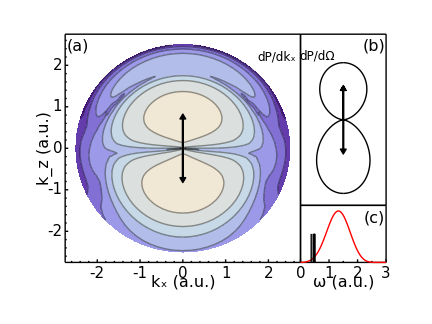

/Users/nevence/Documents/utk/first/hIon.pdf

```mathematica
ionDAT=Import[dataDIR<>"H05e-7/ion.dat"];
tSTEP=Length[First[ionDAT]];
kMAX=1.1*Max[#[[1]]&/@ionDAT];
hIonFIG=With[{zoom=0.0025,shiftY=0.0},Figure[{
Multipanel[
{{0,1},{0,1}},
{2,3},
BufferB->3,
TickNudge->{-4,{-3,0},0,{3,0}},
TickFontSize->15,
FontSize->16
],
(*dP/dkxdkz*)
FigurePanel[{1,1},
FrameTicks->Automatic,
ShowTickLabels->Automatic,
ShowFrameLabels->Automatic,
PanelAdjustments->{{0,1.2},{1,0}},
PanelLetter->"(a)",
PlotRange->{{-kMAX,kMAX},{-kMAX,kMAX}},
LabL->"k_z (a.u.)",BufferL->3,
LabB->"k_x (a.u.)",BufferB->3
],
ScaledLabel[{0.9,0.9},"dP/dk_x"],
RawGraphics[dPdkdΩ[ionDAT,tSTEP]],
SchemeArrow[{{0,0},{0,0.3*kMAX}},ArrowType->ShapeArrow,Width->1],
SchemeArrow[{{0,0},{0,-0.3*kMAX}},ArrowType->ShapeArrow,Width->1],
(*dPdΩ*)
FigurePanel[{1,3},
PanelAdjustments->{{-0.2,0},{0.5,0}},
PanelLetter->"(b)",
PanelLetterCorner->{1,1},
PlotRange->zoom{{-1,1},{-2-shiftY,2-shiftY}},
FrameTicks->None
(*,FrameTicks->{LinTicks[0,0.001,0.001,2],Automatic},
ShowTicks->{True,True,False,False},
ShowTickLabels->{True,True,False,False}
*)
],
rawGraphicsdPdΩ[ionDAT,tSTEP,1],
SchemeArrow[{{0,0},{0,0.4*zoom(2-shiftY)}},ArrowType->ShapeArrow,Width->1],
SchemeArrow[{{0,0},{0,-0.4*zoom(2-shiftY)}},ArrowType->ShapeArrow,Width->1],
ScaledLabel[{0.2,0.874},"dP/dΩ"],
(*Power Spectrum*)
FigurePanel[{2,3},
FrameTicks->{LinTicks[0,3,1.0,2],None},
PanelAdjustments->{{-0.2,0},{0,-0.5}},
PanelLetter->"(c)",
PanelLetterCorner->{1,1},
PlotRange->{{0,3},{0,1}},
LabB->"ω (a.u.)",BufferB->3
],
RawGraphics[psPLOT],
RawGraphics[With[{en=0.5},Graphics[
Table[Line[{{en(1-1/n^2),0},{en(1-1/n^2),0.5}}],{n,2,10}]
]]]
},
PlotRange->{{-0.08,1.02},{-0.14,1.02}},ImageSize->72*1.5*{4,3}
]]
If[export,Export[exportPath<>"hIon."<>suffix,hIonFIG]]
```

#### H (alt)

Total Ionization Probability = 0.0159555

xMAX = 0.00155345

yupperMAX = 0.00333466

ylowerMAX = 0.00430131

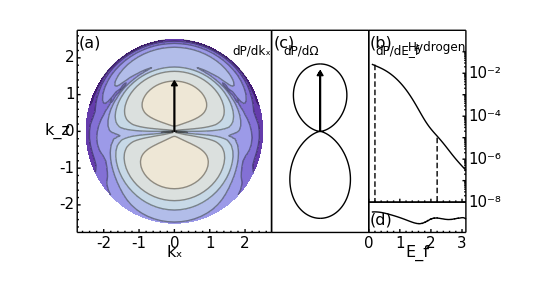

/Users/nevence/Documents/utk/first/hIon.pdf

```mathematica
ionDAT=Import[dataDIR<>"H05e-7/ion.dat"];
tSTEP=Length[First[ionDAT]];
kMAX=1.1*Max[#[[1]]&/@ionDAT];
hIonFIG=With[{zoom=0.0025,shiftY=0},Figure[{
Multipanel[
{{0,1},{0,1}},
{2,4},
BufferB->3,
TickNudge->{-4,{-3,0},0,{3,0}},
TickFontSize->15,
FontSize->16
],
(*dP/dkxdkz*)
FigurePanel[{1,1},
FrameTicks->Automatic,
ShowTickLabels->Automatic,
ShowFrameLabels->Automatic,
PanelAdjustments->{{0,1},{1,0}},
PanelLetter->"(a)",
PlotRange->{{-kMAX,kMAX},{-kMAX,kMAX}},
LabL->"k_z",BufferL->3,OrientationL->Horizontal,
LabB->"k_x",BufferB->3
],
ScaledLabel[{0.9,0.9},"dP/dk_x"],
RawGraphics[dPdkdΩ[ionDAT,tSTEP]],
SchemeArrow[{{0,0},{0,0.5*kMAX}},ArrowType->ShapeArrow,Width->1],
(*dPdΩ*)
FigurePanel[{1,3},
PanelAdjustments->{{0,0},{1,0}},
PanelLetter->"(c)",
PlotRange->zoom{{-1,1},{-2-shiftY,2-shiftY}},
FrameTicks->None
(*,FrameTicks->{LinTicks[0,0.001,0.001,2],Automatic},
ShowTicks->{True,True,False,False},
ShowTickLabels->{True,True,False,False}
*)
],
rawGraphicsdPdΩ[ionDAT,tSTEP,1],
SchemeArrow[{{0,0},{0,0.6*zoom(2-shiftY)}},ArrowType->ShapeArrow,Width->1],
ScaledLabel[{0.3,0.9},"dP/dΩ"],
(*dPdE*)
rawGraphicsdPdE[ionDAT,tSTEP,1,"Hydrogen",
-8,0,(*yRange*)
{
{{0.2,-1.6},{0.2,-8}},
{{2.2,-5.0},{2.2,-8}}
}]
},
PlotRange->{{-0.07,1.08},{-0.14,1.02}},ImageSize->72*2*{3.8,2}
]]
If[export,Export[exportPath<>"hIon."<>suffix,hIonFIG]]
```

#### He

Total Ionization Probability = 0.000834176

xMAX = 0.000132172

yupperMAX = 0.0000834925

ylowerMAX = 0.000482553

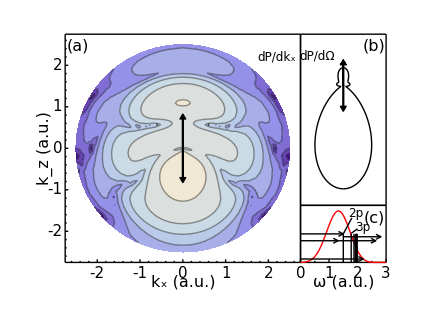

/Users/nevence/Documents/utk/first/heIon.pdf

```mathematica
ionDAT=Import[dataDIR<>"He05/ion.dat"];
tSTEP=Length[First[ionDAT]];
kMAX=1.1*Max[#[[1]]&/@ionDAT];
heIonFIG=With[{zoom=0.0002,shiftY=0.8},Figure[{
Multipanel[
{{0,1},{0,1}},
{2,3},
BufferB->3,
TickNudge->{-4,{-3,0},0,{3,0}},
TickFontSize->15,
FontSize->16
],
(*dP/dkxdkz*)
FigurePanel[{1,1},
FrameTicks->Automatic,
ShowTickLabels->Automatic,
ShowFrameLabels->Automatic,
PanelAdjustments->{{0,1.2},{1,0}},
PanelLetter->"(a)",
PlotRange->{{-kMAX,kMAX},{-kMAX,kMAX}},
LabL->"k_z (a.u.)",BufferL->3,
LabB->"k_x (a.u.)",BufferB->3
],
ScaledLabel[{0.9,0.9},"dP/dk_x"],
RawGraphics[dPdkdΩ[ionDAT,tSTEP]],
SchemeArrow[{{0,0},{0,0.3*kMAX}},ArrowType->ShapeArrow,Width->1],
SchemeArrow[{{0,0},{0,-0.3*kMAX}},ArrowType->ShapeArrow,Width->1],
(*dPdΩ*)
FigurePanel[{1,3},
PanelAdjustments->{{-0.2,0},{0.5,0}},
PanelLetter->"(b)",
PanelLetterCorner->{1,1},
PlotRange->zoom{{-1,1},{-2-shiftY,2-shiftY}},
FrameTicks->None
],
rawGraphicsdPdΩ[ionDAT,tSTEP,1],
SchemeArrow[{{0,0},{0,0.5*zoom(2-shiftY)}},ArrowType->ShapeArrow,Width->1],
SchemeArrow[{{0,0},{0,-0.5*zoom(2-shiftY)}},ArrowType->ShapeArrow,Width->1],
ScaledLabel[{0.2,0.874},"dP/dΩ"],
(*power spectrum*)
FigurePanel[{2,3},
FrameTicks->{LinTicks[0,3,1.0,2],None},
PanelAdjustments->{{-0.2,0},{0,-0.5}},
PanelLetter->"(c)",
PanelLetterCorner->{1,1},
PlotRange->{{0,3},{0,1}},
LabB->"ω (a.u.)",BufferB->3
],
RawGraphics[psPLOT],
ManualLabel[{1.95,0.85},"2p"],
SchemeLine[{{1.8,0.78},{1.5,0.5}}],
ManualLabel[{2.2,0.62},"3p"],
SchemeLine[{{1.78,0.51},{2.0,0.59}}],
RawGraphics[With[{en=2.0},Graphics[
Table[Line[{{en(1-1/n^2),0},{en(1-1/n^2),0.5}}],{n,2,10}]
]]],
With[{ω=1.32},Sequence@@{
SchemeArrow[{{0,0.5},{1.5,0.5}}],
SchemeArrow[{{1.5,0.45},{1.5+ω,0.45}}],
SchemeArrow[{{0,0.38},{ω,0.38}}],
SchemeArrow[{{ω,0.38},{2ω,0.38}}],
SchemeArrow[{{0,0.06},{2.2,0.06}}]
}]
},
PlotRange->{{-0.08,1.02},{-0.14,1.02}},ImageSize->72*1.5*{4,3}
]]
If[export,Export[exportPath<>"heIon."<>suffix,heIonFIG]]
```

#### Li

Total Ionization Probability = 0.0102613

xMAX = 0.00127583

yupperMAX = 0.00139081

ylowerMAX = 0.00386468

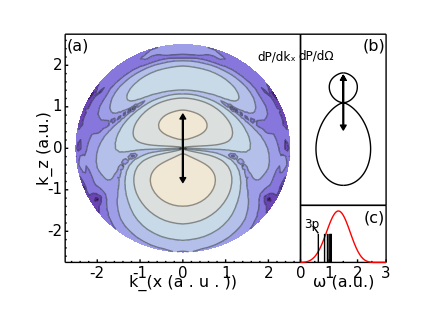

/Users/nevence/Documents/utk/first/liIon.pdf

```mathematica
ionDAT=Import[dataDIR<>"2Li03e-6/ion.dat"];
tSTEP=Length[First[ionDAT]];
kMAX=1.1*Max[#[[1]]&/@ionDAT];
liIonFIG=With[{zoom=0.002,shiftY=0.4},Figure[{
Multipanel[
{{0,1},{0,1}},
{2,3},
BufferB->3,
TickNudge->{-4,{-3,0},0,{3,0}},
TickFontSize->15,
FontSize->16
],
(*dP/dkxdkz*)
FigurePanel[{1,1},
FrameTicks->Automatic,
ShowTickLabels->Automatic,
ShowFrameLabels->Automatic,
PanelAdjustments->{{0,1.2},{1,0}},
PanelLetter->"(a)",
PlotRange->{{-kMAX,kMAX},{-kMAX,kMAX}},
LabL->"k_z (a.u.)",BufferL->3,
LabB->"k_(x (a . u . ))",BufferB->3
],
ScaledLabel[{0.9,0.9},"dP/dk_x"],
RawGraphics[dPdkdΩ[ionDAT,tSTEP]],
SchemeArrow[{{0,0},{0,0.3*kMAX}},ArrowType->ShapeArrow,Width->1],
SchemeArrow[{{0,0},{0,-0.3*kMAX}},ArrowType->ShapeArrow,Width->1],
(*dPdΩ*)
FigurePanel[{1,3},
PanelAdjustments->{{-0.2,0},{0.5,0}},
PanelLetter->"(b)",
PanelLetterCorner->{1,1},
PlotRange->zoom{{-1,1},{-2-shiftY,2-shiftY}},
FrameTicks->None
(*,FrameTicks->{LinTicks[0,0.001,0.001,2],Automatic},
ShowTicks->{True,True,False,False},
ShowTickLabels->{True,True,False,False}
*)
],
rawGraphicsdPdΩ[ionDAT,tSTEP,1],
SchemeArrow[{{0,0},{0,0.4*zoom(2-shiftY)}},ArrowType->ShapeArrow,Width->1],
SchemeArrow[{{0,0},{0,-0.4*zoom(2-shiftY)}},ArrowType->ShapeArrow,Width->1],
ScaledLabel[{0.18,0.8725},"dP/dΩ"],
(*Power Spectrum*)
FigurePanel[{2,3},
FrameTicks->{LinTicks[0,3,1.0,2],None},
PanelAdjustments->{{-0.2,0},{0,-0.5}},
PanelLetter->"(c)",
PanelLetterCorner->{1,1},
PlotRange->{{0,3},{0,1}},
LabB->"ω (a.u.)",BufferB->3
],
RawGraphics[psPLOT],
ManualLabel[{0.4,0.67},"3p"],
SchemeLine[{{0.625,0.51},{0.43,0.64}}],
RawGraphics[With[{en=4.5},Graphics[
Table[Line[{{en(1/4-1/n^2),0},{en(1/4-1/n^2),0.5}}],{n,3,10}]
]]]
},
PlotRange->{{-0.08,1.02},{-0.14,1.02}},ImageSize->72*1.5*{4,3}
]]
If[export,Export[exportPath<>"liIon."<>suffix,liIonFIG]]
```

## H_2^+ 3D vs 4D

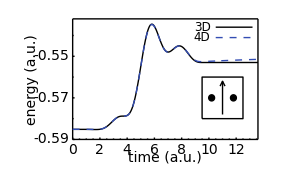

/Users/nevence/Documents/utk/first/h2en.pdf

```mathematica
enA=Import["/Users/nevence/Documents/utk/data/4H/3D/energy.dat"];
en4=Import["/Users/nevence/Documents/utk/data/4H/4D/energy.dat"];
enDISCREP=en4[[1,2]]-enA[[1,2]];
en3={#[[1]],#[[2]]+enDISCREP}&/@enA;
dyA=-0.005;
yA0=-0.531;
yA1=yA0+dyA;
yA2=yA0+2dyA;
x0=9.5;
x1=10.5;
x2=13.2;
xMAX=13.6;
yMIN=-0.59;
yMAX=-0.532;
xFrame=4;
yFrame=2.5;
rScl=0.005{yFrame/Abs[yMAX-yMIN],xFrame/xMAX}; (*Scales the x and y Radius to make a circle*)
xCent=11;
yCent=-0.57;
H2enFIG=Figure[{
FigurePanel[{{0,1},{0,1}},
PlotRange->{{0,xMAX},{yMIN,yMAX}},
LabL->"energy (a.u.)",BufferL->7,
LabB->"time (a.u.)",BufferB->3.1,
FrameTicks->{Automatic,LinTicks[yMIN,yMAX,0.02,2]},
ShowTickLabels->{True,True,False,False},
FontSize->14,
ShowFrameLabels->{True,True,False,False},
TickNudge->{-4,{-4,0},0,0}
],
RawGraphics[ListLinePlot[{en3,en4},PlotStyle->styleList]],
RawGraphics[Graphics[{
Sequence@@styleList[[1]],Line[{{x1,yA1},{x2,yA1}}],
Sequence@@styleList[[2]],Line[{{x1,yA2},{x2,yA2}}]}]],
ManualLabel[{x0,yA1},"3D"],
ManualLabel[{x0,yA2},"4D"],
SchemeBox[{xCent-1.5,yCent-0.01},{xCent+1.5,yCent+0.01},FillColor->White],
SchemeCircle[{xCent+0.8,yCent},rScl],
SchemeCircle[{xCent-0.8,yCent},rScl],
SchemeArrow[{{xCent,yCent-0.008},{xCent,yCent+0.008}}]
},PlotRange->{{-0.25,1.02},{-0.2,1.02}},ImageSize->72*{xFrame,yFrame}
]
If[export,Export[exportPath<>"h2en."<>suffix,H2enFIG]]
```

## H_2^+ para

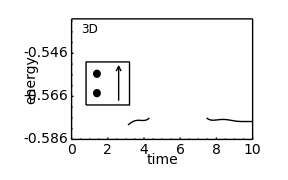

/Users/nevence/Documents/utk/thesis/hperp2en.png

```mathematica
enA=Import["/Users/nevence/Documents/utk/data/Hpara2/energy.dat"];
en4=Import["/Users/nevence/Documents/utk/data/4H/4D/energy.dat"];
enDISCREP=en4[[1,2]]-enA[[1,2]];
en3={#[[1]],#[[2]]+enDISCREP}&/@enA;
dyA=-0.005;
yA0=-0.53;
yA1=yA0+dyA;
yA2=yA0+2dyA;
x0=1.0;
x1=2.0;
x2=4.0;
xMAX=10;
yMIN=-0.586;
yMAX=-0.53;
xFrame=4;
yFrame=2.5;
rScl=0.004{yFrame/Abs[yMAX-yMIN],xFrame/xMAX}; (*Scales the x and y Radius to make a circle*)
xCent=2;
yCent=-0.56;
Hperp2enFIG=Figure[{
FigurePanel[{{0,1},{0,1}},
PlotRange->{{0,xMAX},{yMIN,yMAX}},
LabL->"energy",BufferL->7,
LabB->"time",BufferB->3.5,
FontSize->14,
FrameTicks->{Automatic,LinTicks[yMIN,yMAX,0.02,4]},
ShowTickLabels->{True,True,False,False},
ShowFrameLabels->{True,True,False,False},
TickNudge->{-4,{-4,0},0,0}
],
RawGraphics[ListLinePlot[en3,PlotStyle->styleList]],
ManualLabel[{x0,yA1},"3D"],
SchemeBox[{xCent-1.2,yCent-0.01},{xCent+1.2,yCent+0.01},FillColor->White],
SchemeCircle[{xCent-0.6,yCent+0.0045},rScl],
SchemeCircle[{xCent-0.6,yCent-0.0045},rScl],
SchemeArrow[{{xCent+0.6,yCent-0.008},{xCent+0.6,yCent+0.008}}]
},PlotRange->{{-0.25,1.05},{-0.2,1.02}},ImageSize->72*{xFrame,yFrame}
]
If[export,Export[exportPath<>"hperp2en."<>suffix,Hperp2enFIG,ImageResolution->300]]
```